```mathematica
Quit[]
```

```mathematica
SetDirectory["~/Documents/Univ/NANOGrav2PBH/num"];
```

```mathematica
499/(473+499)//N
```

0.513374

```mathematica
z[zG_]=-1/3 Log[1-3zG];
zG[z_]=1/3(1-E^(-3z));
```

```mathematica
Simplify[z[zG[z]],{z∈Reals}]
```

z

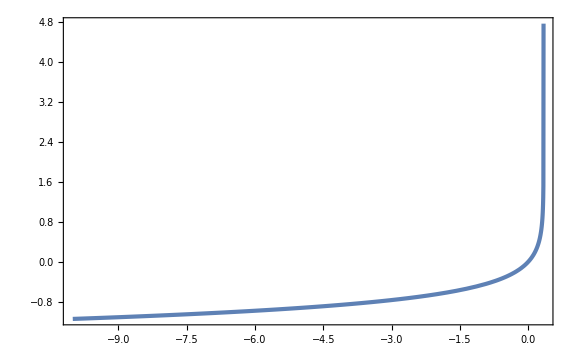

```mathematica
Plot[z[zG],{zG,-10,1/3},PlotRange->Full]
```

```mathematica
P[z_]=zG'[z] 1/Sqrt[2π s2] Exp[(-zG[z]^2)/(2s2)]//Simplify
```

(ⅇ^(-((-1+ⅇ^(-3 z))^2)/(18 s2)-3 z))/(√(2 π) √s2)

```mathematica
meanz[s2_]=Integrate[z[zG] 1/Sqrt[2π s2] Exp[-zG^2/(2s2)],{zG,-∞,1/3},Assumptions->{s2>0}]
```

1/(108 √(2 π) s2)(-12 √s2 HypergeometricPFQ[{1/2,1/2},{3/2,3/2},-1/(18 s2)]+√π (-√2 HypergeometricPFQ[{1,1},{3/2,2},-1/(18 s2)]+9 √2 s2 (EulerGamma+Log[2/(9 s2)]+Erf[1/(3 √2 √s2)] (2 EulerGamma+Log[2/(9 s2)]))-3 √s2 Hypergeometric1F1Regularized^(0,1,0)[1/2,3/2,-1/(18 s2)]))

```mathematica
meanz[10^-2]//N
```

0.0177644

```mathematica
Normal[Series[-3z-((1-E^(-3z))^2)/(18s2),{z,0,2}]]
```

-3 z-z^2/(2 s2)

```mathematica
E^(-5z[r]/2)1/r^2 D[(r^2 D[E^(z[r]/2), r]), r](r E^z[r])^2 D[(r E^z[r]), r]//Simplify
```

1/4 ⅇ^z[r] r (1+r z'[r]) (4 z'[r]+r z'[r]^2+2 r z''[r])

```mathematica
Integrate[E^(-5z[r]/2)1/r^2 D[(r^2 D[E^(z[r]/2), r]), r](r E^z[r])^2 D[(r E^z[r]), r]//Simplify,r]
```

1/4 ⅇ^z[r] r^2 z'[r] (2+r z'[r])

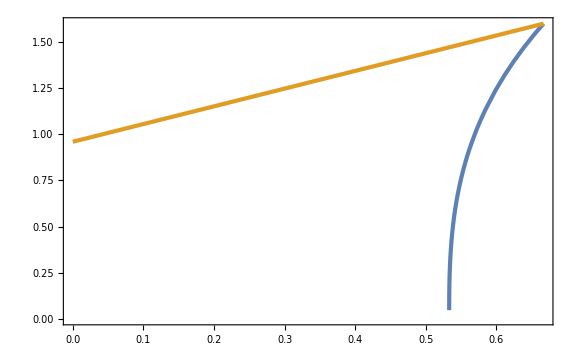

```mathematica
Plot[{KK(d-dc)^γ/.{KK->3.3,dc->0.533,γ->0.36},CC(1+d)/.{CC->(KK(dmax-dc)^γ)/(1+dmax)}/.{KK->3.3,dc->0.533,γ->0.36,dmax->2/3}},{d,0,2/3}]
```

```mathematica
(KK(dmax-dc)^γ)/(1+dmax)/.{KK->3.3,dc->0.533,γ->0.36,dmax->2/3}
```

0.959475

```mathematica
1/r^2 D[(r^2 D[Sin[k r]/(k r), r]), r]//Simplify
```

-(k Sin[k r])/r

```mathematica
CC={{sX^2,sX sY},{sX sY,sY^2}};
```

```mathematica
Det[CC]
```

0

```mathematica
Eigensystem[CC]
```

{{0,sX^2+sY^2},{{-sY/sX,1},{sX/sY,1}}}

## Gaussian

### monochromatic

```mathematica
sigman[n_,ks_,As_]=ks^n √As
psin[n_,r_,ks_]=ks^(2n-4)Sin[ks r]/(ks r)
```

√As ks^n

(ks^(-5+2 n) Sin[ks r])/r

```mathematica
gamma3=sigman[3,ks,As]^2/(sigman[2,ks,As]sigman[4,ks,As])
Rb[ks_]=√3 sigman[3,ks,As]/sigman[4,ks,As]
```

1

(√3)/ks

### log-normal

```mathematica
Quit[]
```

```mathematica
$Assumptions={sg>0,ks>0,n>0};
```

```mathematica
calPs[k_,ks_,As_,sg_]=As/(√(2π)sg)Exp[(-(Log[k]-Log[ks])^2)/(2 sg^2)];
Simplify[Integrate[calPs[k,ks,As,sg] 1/k,{k,0,∞}]]
```

As

```mathematica
sigman[n_,ks_,As_,sg_]=Simplify[√Integrate[k^(2n)calPs[k,ks,As,sg] 1/k,{k,0,∞}]]
```

√As ⅇ^(n^2 sg^2) ks^n

```mathematica
gamma1[ks_,As_,sg_]=sigman[1,ks,As,sg]^2/(sigman[0,ks,As,sg]sigman[2,ks,As,sg])
gamma2[ks_,As_,sg_]=sigman[2,ks,As,sg]^2/(sigman[0,ks,As,sg]sigman[4,ks,As,sg])
gamma3[ks_,As_,sg_]=sigman[3,ks,As,sg]^2/(sigman[2,ks,As,sg]sigman[4,ks,As,sg])
```

ⅇ^(-2 sg^2)

ⅇ^(-8 sg^2)

ⅇ^(-2 sg^2)

```mathematica
DD[ks_,As_,sg_]=1-gamma1[ks,As,sg]^2-gamma2[ks,As,sg]^2-gamma3[ks,As,sg]^2+2gamma1[ks,As,sg]gamma2[ks,As,sg]gamma3[ks,As,sg]//Simplify
```

ⅇ^(-16 sg^2) (-1+ⅇ^(4 sg^2))^3 (1+ⅇ^(4 sg^2))

```mathematica
Simplify[(2DD[ks,As,sg] sigman[0,ks,As,sg]^2)/(1-gamma3[ks,As,sg])]/.{sg->0}
```

0

```mathematica
normN=Simplify[Sum[calPs[E^logk,ks,As,sg],{logk,Log[ks]-sg,Log[ks]+sg,sg}]3sg]/.{As->1}
```

(3 (2+√ⅇ))/(√(2 ⅇ π))

```mathematica
psin[n_,r_,ks_,sg_]=Normal[Series[Simplify[1/(normN sigman[2,ks,As,sg]^2)Sum[Exp[2n logk] Sin[E^logk r]/(E^logk r)calPs[E^logk,ks,As,sg],{logk,Log[ks]-sg,Log[ks]+sg,sg}]3sg],{sg,0,2}]]
```

(ks^(-5+2 n) Sin[ks r])/r-(ks^(-5+2 n) sg^2 (ks r Cos[ks r]-4 ks n r Cos[ks r]+15 Sin[ks r]+8 √ⅇ Sin[ks r]+4 n Sin[ks r]-4 n^2 Sin[ks r]+ks^2 r^2 Sin[ks r]))/((2+√ⅇ) r)

```mathematica
Rb[ks_,sg_]=√3 sigman[3,ks,As,sg]/sigman[4,ks,As,sg]
```

(√3 ⅇ^(-7 sg^2))/ks

```mathematica
zetabar[r_,ks_,mu2_,kb_]=Normal[Series[Simplify[mu2/(1-gamma3[ks,As,sg]^2)(psin[1,r,ks,sg]-1/3 Rb[ks,sg]^2 psin[2,r,ks,sg])-mu2 kb^2 sigman[2,ks,As,sg]/(sigman[4,ks,As,sg]gamma3[ks,As,sg](1-gamma3[ks,As,sg]^2))(gamma3[ks,As,sg]^2 psin[1,r,ks,sg]-1/3 Rb[ks,sg]^2 psin[2,r,ks,sg])],{sg,0,2}]]/.{sg->0}
```

(mu2 (-4 ks (-kb^2+ks^2) r Cos[ks r]+((-12-10 √ⅇ) kb^2+(20+14 √ⅇ) ks^2) Sin[ks r]))/(4 (2+√ⅇ) ks^5 r)

```mathematica
zetaks[r_,ks_,mu2_]=zetabar[r,ks,mu2,ks]//Simplify
```

(mu2 Sin[ks r])/(ks^3 r)

```mathematica
zetax[x_,mu_]=zetaks[x/ks,ks,mu ks^2]//Simplify
```

(mu Sin[x])/x

```mathematica
CompactC[x_,mu_]=(1-(1+x D[zetax[x,mu], x])^2)/3//Simplify
```

(x^2-(x+mu x Cos[x]-mu Sin[x])^2)/(3 x^2)

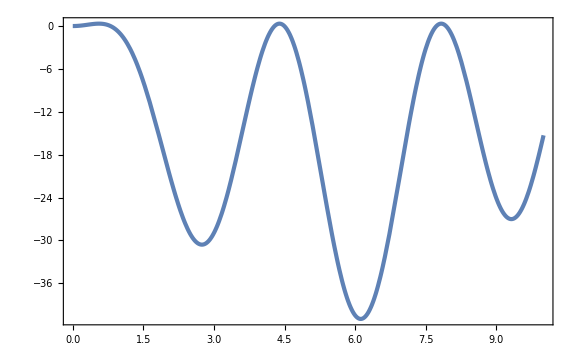

```mathematica
Plot[CompactC[x,10],{x,0,10}]
```

```mathematica
rmcond[x_]=-x^2/mu(D[zetax[x,mu], x]+x D[D[zetax[x,mu], x], x])//Simplify
```

x Cos[x]+(-1+x^2) Sin[x]

```mathematica
rmcond2[x_,mu_]=(1+x D[zetax[x,mu], x])//Simplify
```

1+mu Cos[x]-(mu Sin[x])/x

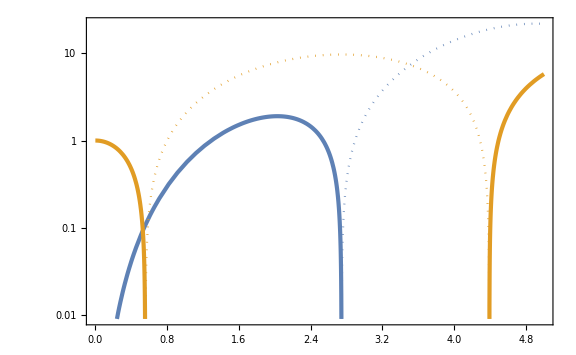

```mathematica
LogPlot[{rmcond[x],-rmcond[x],rmcond2[x,10],-rmcond2[x,10]},{x,0,5},PlotStyle->{AbsoluteThickness[3],{Color[1],Dotted},{AbsoluteThickness[3],Color[2]},{Color[2],Dotted}}]
```

```mathematica
xm=x/.FindRoot[rmcond[x]==0,{x,3}]
```

2.74371

```mathematica
Simplify[Solve[CompactC[x,mu]==Cth,mu]]/.{x->xm,Cth->0.267}
```

{{mu→0.521027},{mu→1.36026}}

```mathematica
Sin[xm]/xm
```

0.141221

```mathematica
xm/(6.4 10^-14)
```

4.28704×10^13

```mathematica
f[z_]=1/2 z(z^2-3)(Erf[1/2 √(5/2)z]+Erf[√(5/2)z])+√(2/(5π))((8/5+31/4 z^2)Exp[-5/8 z^2]+(-8/5+1/2 z^2)Exp[-5/2 z^2]);
```

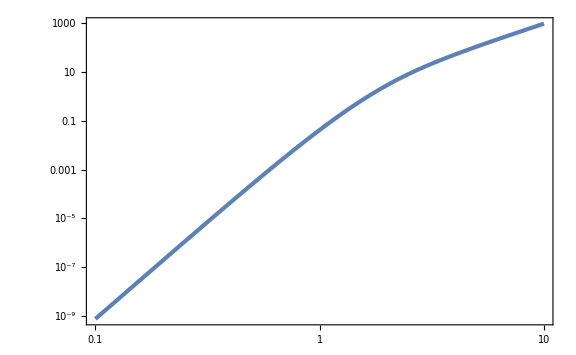

```mathematica
LogLogPlot[f[z],{z,0.1,10}]
```

```mathematica
gineV=(1.783 10^-33)^-1;
MpcinvineV=(10^6 3.086 10^16)^-1 1.973 10^-7;
KineV=(1.16 10^4)^-1;
MplineV=2.435 10^(18+9);
kminvsinvMpcineV=(10^3 6.582 10^-16)/(3.086 10^16 10^6);
```

```mathematica
((1/0.12 1/(2.4 10^4)10^20 gineV(3/(2π))^(3/2)(4.3 10^13 MpcinvineV)^3)/(π^2/30 3.38(2.725KineV)^4 0.28))^-1
```

7.10265×10^-18

```mathematica
((10^20 gineV(3/(2π))^(3/2)(4.3 10^13 MpcinvineV)^3)/(0.12 3 MplineV^2(100 kminvsinvMpcineV)^2 0.28))^-1
```

7.07168×10^-18

```mathematica
mu2[M_]=Log[M/10^20]/0.28;
```

```mathematica
PG[x_,sg2_]=1/(√(2π sg2))Exp[-x^2/(2sg2)];
```

```mathematica
mu2th=0.521;
```

```mathematica
Mmin=M/.Solve[mu2[M]==mu2th,M][[1]]
```

1.15706×10^20

```mathematica
fPBH[M_,As_]=M/10^20(f[mu2[M]/(√As)]PG[mu2[M],As])/(7.1 10^-18)UnitStep[mu2[M]-mu2th];
```

```mathematica
fPBH[1.18 10^20,2.8 10^-3]
```

1.35757×10^-6

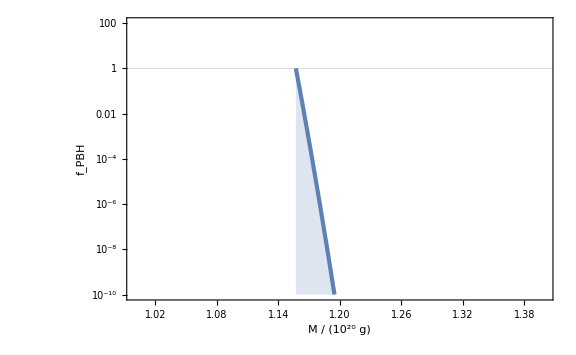

```mathematica
FigfPBH=LogPlot[fPBH[M 10^20,2.8 10^-3],{M,1,1.4},GridLines->{None,{1}},PlotRange->{{1,1.4},{10^-10,100}},Filling->Bottom,FrameLabel->{Row[{M," / (",Superscript[10,20]," g)"}],Subscript[f, PBH]}]
```

```mathematica
NIntegrate[fPBH[E^logM,2.8 10^-3],{logM,Log[Mmin],Log[1.2 10^20]}]
```

0.00155557

#### Press-Schechter

```mathematica
WTH[z_]=3(Sin[z]-z Cos[z])/z^3;
TrsT[z_]=WTH[z/√3];
```

```mathematica
sigmad2[R_,ks_,As_]=16/81 WTH[ks R]^2(ks R)^4 TrsT[ks R]^2 As//Simplify
```

(48 As (-ks R Cos[ks R]+Sin[ks R])^2 (√3 ks R Cos[(ks R)/(√3)]-3 Sin[(ks R)/(√3)])^2)/(ks^8 R^8)

```mathematica
sigmad2[ks^-1,ks,1]//N
```

0.150801

```mathematica
betaPBH[R_,ks_,As_]=1/2 Erfc[dth/(√(2sigmad2[R,ks,As]))]/.{dth->0.267 2};
```

```mathematica
MPBH[R_]=10^20(R/(6.4 10^-14))^2;
```

```mathematica
fPBHPS[R_,ks_,As_]=betaPBH[R,ks,As]/(7.2 10^-16)(MPBH[R]/10^20)^(-1/2);
```

```mathematica
{MPBH[R],fPBHPS[R,ks,As]}/.{R->ks^-1}/.{ks->4.3 10^13,As->2.8 10^-3}
```

{1.32039×10^19,1.32×10^-133}

```mathematica
fPBHPSList=Table[{MPBH[10^logR]/10^20,fPBHPS[10^logR,4.3 10^13,2.8 10^-3]},{logR,-Log10[4.3 10^13]-1,-Log10[4.3 10^13]+1,0.01}];
```

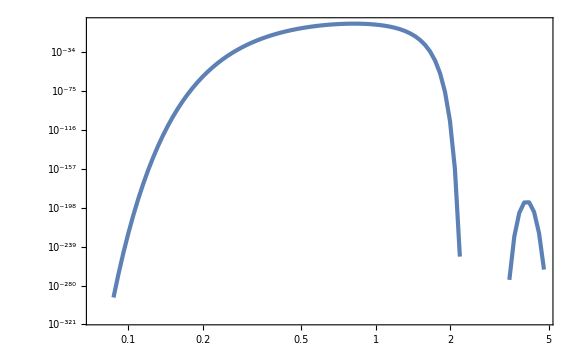

```mathematica
ListLogLogPlot[fPBHPSList]
```

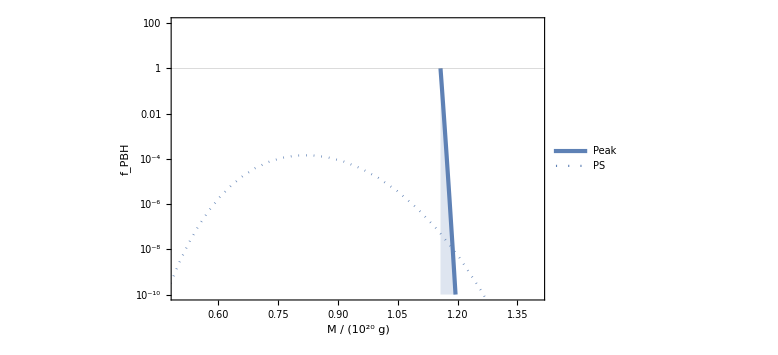

```mathematica
Show[LogPlot[{fPBH[M 10^20,2.8 10^-3],0},{M,1,1.4},GridLines->{None,{1}},PlotRange->{{0.5,1.4},{10^-10,100}},Filling->Bottom,FrameLabel->{Row[{M," / (",Superscript[10,20]," g)"}],Subscript[f, PBH]},PlotStyle->{AbsoluteThickness[3],{Color[1],Dotted}},PlotLegends->Placed[{"Peak","PS"},{0.2,0.65}]],ListLogPlot[fPBHPSList,PlotStyle->{Color[1],Dotted}]]
```

### scale-invariant

```mathematica
Quit[]
```

```mathematica
$Assumptions={sg>0,ks>0,n>0,As>0,kW>0,mu>0,kappa>0};
```

```mathematica
sigman[n_,kW_,As_]=√(As Integrate[Exp[2n logk],{logk,-∞,Log[kW]}])//Simplify
```

(kW^n √(As/n))/(√2)

```mathematica
psin[n_,r_,kW_]=1/sigman[2,kW,As]^2 As Integrate[k^(2n)Sin[k r]/(k r)1/k,{k,0,kW}]
```

(2 kW^(-4+2 n) HypergeometricPFQ[{n},{3/2,1+n},-1/4 kW^2 r^2])/n

```mathematica
psin[1,r,kW]//Simplify
psin[2,r,kW]//Simplify
```

(4-4 Cos[kW r])/(kW^4 r^2)

(-8+(8-4 kW^2 r^2) Cos[kW r]+8 kW r Sin[kW r])/(kW^4 r^4)

```mathematica
gamma3=sigman[3,kW,As]^2/(sigman[2,kW,As]sigman[4,kW,As])
Rb[kW_]=√3 sigman[3,kW,As]/sigman[4,kW,As]
```

(2 √2)/3

2/kW

```mathematica
zetabar[r_,kW_,mu2_,kb_]=mu2/(1-gamma3^2)(psin[1,r,kW]-1/3 Rb[kW]^2 psin[2,r,kW])-mu2 kb^2 sigman[2,kW,As]/(sigman[4,kW,As]gamma3(1-gamma3^2))(gamma3^2 psin[1,r,kW]-1/3 Rb[kW]^2 psin[2,r,kW])//Simplify
```

(12 mu2 (-12 kb^2+8 kW^2-4 kb^2 kW^2 r^2+3 kW^4 r^2+(kW^2 (-8+kW^2 r^2)-2 kb^2 (-6+kW^2 r^2)) Cos[kW r]+4 kW (3 kb^2-2 kW^2) r Sin[kW r]))/(kW^8 r^4)

```mathematica
zetax[x_,mu_,kappa_]=zetabar[x/kW,kW,mu kW^2,kappa kW]//Simplify
```

-(12 mu (-8+12 kappa^2-3 x^2+4 kappa^2 x^2+(8-x^2+2 kappa^2 (-6+x^2)) Cos[x]-4 (-2+3 kappa^2) x Sin[x]))/x^4

```mathematica
CompactC[x_,mu_,kappa_]=(1-(1+x D[zetax[x,mu,kappa], x])^2)/3//Simplify
```

1/3 (1-((-384 mu+576 kappa^2 mu-72 mu x^2+96 kappa^2 mu x^2+x^4+24 mu (16-5 x^2+8 kappa^2 (-3+x^2)) Cos[x]+12 mu x (32-x^2+2 kappa^2 (-24+x^2)) Sin[x])^2)/x^8)

```mathematica
xmcond[x_,kappa_]=(D[zetax[x,mu,kappa], x]+x D[D[zetax[x,mu,kappa], x], x])x^5/(12mu)//Simplify
```

4 (32+3 x^2-4 kappa^2 (12+x^2))+(-128+52 x^2-x^4+2 kappa^2 (96-40 x^2+x^4)) Cos[x]-x (128-11 x^2+6 kappa^2 (-32+3 x^2)) Sin[x]

```mathematica
FindRoot[xmcond[x,kappa]==0,{x,Min[3/kappa,5]},WorkingPrecision->30]/.{kappa->0.1}
```

FindRoot::srect: Value Min[5.,3./kappa] in search specification {x,Min[3/kappa,5]} is not a number or array of numbers.

FindRoot::precw: The precision of the argument function (4 (32+3 x^2-0.04 (12+x^2))+(-128+52 x^2-x^4+0.02 (96-40 Power[«2»]+x^4)) Cos[x]-x (128-11 x^2+0.06 (-32+3 Power[«2»])) Sin[x]==0) is less than WorkingPrecision (30.).

{x→5.3605653423668734007907946457}

```mathematica
xmList=Table[{10^logk,x/.FindRoot[xmcond[x,10^logk]==0,{x,Min[5/10^logk,5]},WorkingPrecision->30]//Quiet},{logk,-3,2,1/100}];
```

```mathematica
Last[xmList][[2]]100
First[xmList][[2]]
```

2.23610391498593770655394732721

5.37014187909902279530303052317

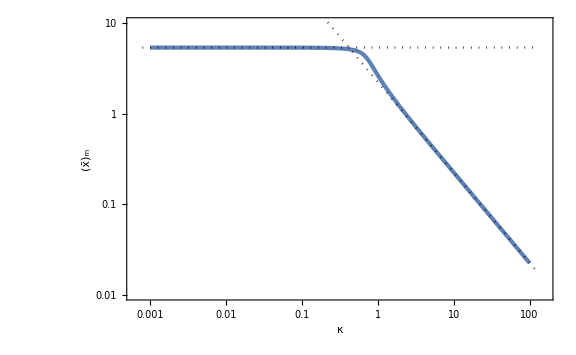

```mathematica
Figxm=Show[ListLogLogPlot[xmList,PlotRange->{{10^-3.2,10^2.2},{0.01,10}},FrameLabel->{κ,Subscript[OverBar[x], "m"]}],LogLogPlot[{2.24/k,5.37},{k,10^-3.1,10^2.1},PlotStyle->{{Black,Dotted}}]]
```

```mathematica
xmint[kappa_]=Interpolation[xmList][kappa];
```

```mathematica
Cmax[mu_,kappa_]=CompactC[xmint[kappa],mu,kappa];
```

```mathematica
muthList=Table[{10^logk,mu/.Solve[Cmax[mu,10^logk]==0.267,mu][[1]]},{logk,-3,2,1/100}];
```

```mathematica
muthint[kappa_]=Interpolation[muthList][kappa];
```

```mathematica
Solve[CompactC[5.37,mu,0]==0.267,mu]
```

{{mu→0.102313},{mu→0.26711}}

```mathematica
Normal[Series[mu/.Solve[Collect[Normal[Series[Simplify[CompactC[2.24/kappa,mu,kappa]],{kappa,∞,4}]],mu]==0.267,mu][[1]],{kappa,∞,2}]]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

-0.322681+0.2539/kappa^2+0.664695 kappa^2

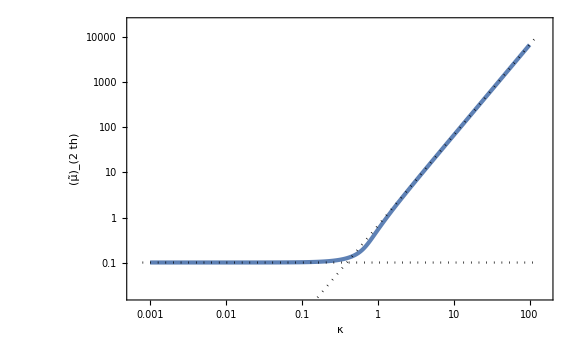

```mathematica
Figmuth=Show[ListLogLogPlot[muthList,FrameLabel->{κ,Subscript[OverTilde[μ], 2th]},PlotRange->{{10^-3.2,10^2.2},{0.02,2 10^4}}],LogLogPlot[{0.102,0.665 k^2},{k,10^-3.1,10^2.1},PlotStyle->{{Black,Dotted}}]]
```

```mathematica
gm[kappa_]=zetax[xmint[kappa],mu,kappa]/mu//Simplify;
```

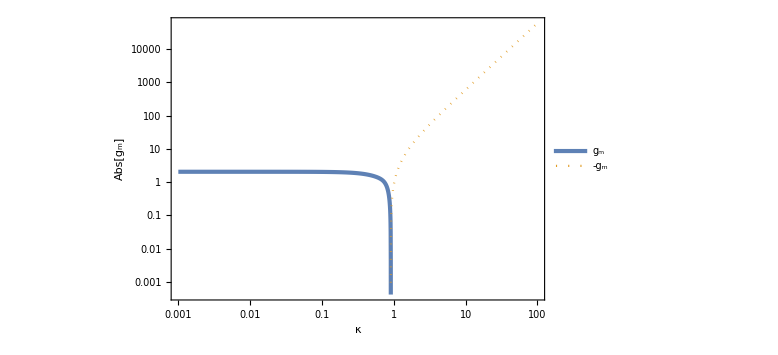

```mathematica
Figgm=LogLogPlot[{gm[kappa],-gm[kappa]},{kappa,10^-3,10^2},PlotRange->Full,PlotStyle->{AbsoluteThickness[3],Dotted},FrameLabel->{κ,Abs[Subscript[g, "m"]]},PlotLegends->Placed[{Subscript[g, "m"],-Subscript[g, "m"]},{0.2,0.8}]]
```

```mathematica
kappac=kappa/.FindRoot[gm[kappa]==0,{kappa,1}]
```

0.90878

```mathematica
MoMkW[mu_,kappa_]=xmint[kappa]^2 Exp[2mu gm[kappa]];
```

```mathematica
MContour=Table[i,{i,-5,5,1/4}];
```

```mathematica
FigMoMkW=Show[ContourPlot[Log10[MoMkW[10^logm,10^logk]],{logk,-3,0.5},{logm,-2,0.5},Contours->MContour,PlotLegends->BarLegend[Automatic,LegendLabel->Row[{Subscript["log", 10],M[Subscript[OverTilde[μ], 2],κ]/Subscript[M, Subscript[k, "W"]]}]],GridLines->{{Log10[kappac]},None},GridLinesStyle->Directive[Black,Dotted,AbsoluteThickness[2]],FrameLabel->{Row[{Subscript["log", 10]," ",κ}],Subscript["log", 10] Subscript[OverTilde[μ], 2]}],ContourPlot[MoMkW[10^logm,10^logk]==MoMkW[muthint[10^-3],10^-3],{logk,-3,0.5},{logm,-2,0.5},ContourStyle->{Black,AbsoluteThickness[2]}],Plot[Log10[muthint[10^logk]],{logk,-3,2},PlotStyle->{AbsoluteThickness[3],Color[4]}]]
```

-Graphics-

```mathematica
Mc=MoMkW[0.1,kappac]
Mth=MoMkW[muthint[10^-3],10^-3]
```

9.17143

43.762

```mathematica
muthint[10^-3]
```

0.102313

```mathematica
muM[kappa_,MM_]=1/(2gm[kappa])Log[MM/xmint[kappa]^2];
```

```mathematica
FindRoot[muM[kappa,30]==muthint[kappa],{kappa,0.7}]
```

{kappa→0.701322}

```mathematica
FindRoot[muM[kappa,0.001]==muthint[kappa],{kappa,2}]
```

{kappa→1.28126}

```mathematica
kappathList1=Table[{10^logM,kappa/.FindRoot[muM[kappa,10^logM]==muthint[kappa],{kappa,0.908}]},{logM,Log10[Mc]+1/1000,Log10[Mth],1/100}];
```

```mathematica
kappathList2=Table[{10^logM,kappa/.FindRoot[muM[kappa,10^logM]==muthint[kappa],{kappa,0.91}]},{logM,-3,Log10[Mc],1/100}];
```

```mathematica
kappathList=Join[kappathList2,kappathList1];
```

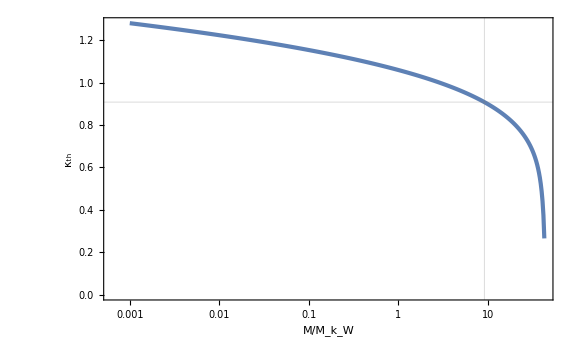

```mathematica
Figkappath=ListLogLinearPlot[kappathList,FrameLabel->{Row[{M,"/",Subscript[M, Subscript[k, "W"]]}],Subscript[κ, th]},GridLines->{{Mc},{kappac}}]
```

```mathematica
kappathint[MM_]=Interpolation[kappathList][MM];
```

```mathematica
sigmamu=(kW^4/sigman[2,kW,As]^2)^(-1/2)//Simplify
```

(√As)/2

```mathematica
kappa2mean=sigman[3,kW,As]^2/sigman[2,kW,As]^2 1/kW^2//Simplify
```

2/3

```mathematica
sigmakappa=((mu^2 kW^4 kW^4)/(sigman[4,kW,As]^2(1-gamma3^2)))^(-1/2)//Simplify
```

(√As)/(6 √2 mu)

```mathematica
CC=1/kW^3(2 3^(3/2))/(2π)^(3/2)mu kW^2 kappa kW sigman[4,kW,As]^2/(sigman[2,kW,As] sigman[3,kW,As]^3)(sigmamu sigmakappa)/(√(1-gamma3^2))kW^3//Simplify
```

(27 kappa)/(8 √2 π^(3/2))

```mathematica
zz=(mu kW^2 kappa^2 kW^2)/sigman[4,kW,As]//Simplify
```

(2 √2 kappa^2 mu)/(√As)

```mathematica
f[z_]=1/2 z(z^2-3)(Erf[1/2 √(5/2)z]+Erf[√(5/2)z])+√(2/(5π))((8/5+31/4 z^2)Exp[-5/8 z^2]+(-8/5+1/2 z^2)Exp[-5/2 z^2]);
PG[z_,m_,s2_]=1/(√(2π s2))Exp[(-(z-m)^2)/(2s2)];
```

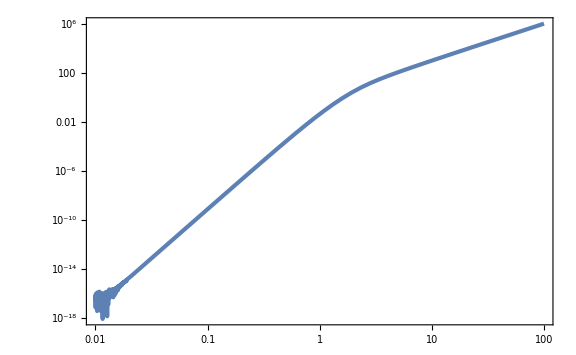

```mathematica
LogLogPlot[f[z],{z,10^-2,10^2}]
```

```mathematica
npk[mu_,kappa_,As_]=CC f[zz]PG[mu,0,sigmamu^2]PG[kappa^2,kappa2mean,sigmakappa^2]kappa//Simplify
```

(81 ⅇ^(-(6 (3-8 kappa^2+6 kappa^4) mu^2)/As) kappa^2 mu (ⅇ^(-(20 kappa^4 mu^2)/As) (-8/5+(4 kappa^4 mu^2)/As+ⅇ^((15 kappa^4 mu^2)/As) (8/5+(62 kappa^4 mu^2)/As)) √(2/(5 π))+(√2 kappa^2 mu (-3 As+8 kappa^4 mu^2) (Erf[(√5 kappa^2 mu)/(√As)]+Erf[(2 √5 kappa^2 mu)/(√As)]))/As^(3/2)))/(4 As π^(5/2))

```mathematica
nPBH[MM_,As_]:=NIntegrate[2gm[kappa]npk[muM[kappa,MM],kappa,As],{kappa,kappac,kappathint[MM]}]/;MM<Mc
nPBH[MM_,As_]:=NIntegrate[2gm[kappa]npk[muM[kappa,MM],kappa,As],{kappa,kappathint[MM],kappac}]/;Mc<MM<Mth
nPBH[MM_,As_]:=NIntegrate[2gm[kappa]npk[muM[kappa,MM],kappa,As],{kappa,0,kappac}]/;MM>Mth
```

```mathematica
nPBH[10,0.0028]
```

8.37733×10^-75

```mathematica
nPBHList1=ParallelTable[{10^logM,nPBH[10^logM,1 10^-2]},{logM,1,2,10^-2}];//AbsoluteTiming
nPBHList2=ParallelTable[{10^logM,nPBH[10^logM,2.8 10^-3]},{logM,1,2,10^-2}];//AbsoluteTiming
```

InterpolatingFunction::dmval: 
                     16/25
   Input value {10 10     } lies outside the range of data in the
     interpolating function. Extrapolation will be used.

{72.8698,Null}

InterpolatingFunction::dmval: 
                     16/25
   Input value {10 10     } lies outside the range of data in the
     interpolating function. Extrapolation will be used.

{72.2775,Null}

```mathematica
(*Export["nPBH1e-2.dat",nPBHList1];
Export["nPBH28e-4.dat",nPBHList2];*)
```

```mathematica
gineV=(1.783 10^-33)^-1;
MpcinvineV=(10^6 3.086 10^16)^-1 1.973 10^-7;
KineV=(1.16 10^4)^-1;
MplineV=2.435 10^(18+9);
kminvsinvMpcineV=(10^3 6.582 10^-16)/(3.086 10^16 10^6);
```

```mathematica
n2f=((10^20 gineV (1.56 10^13 MpcinvineV)^3)/(0.12 3 MplineV^2(100kminvsinvMpcineV)^2))^-1
```

1.74505×10^-16

```mathematica
LognPBHList1=Map[Log10,nPBHList1,{2}]//Simplify;
LognPBHList2=Map[Log10,nPBHList2,{2}]//Simplify;
```

```mathematica
nPBHint1[MM_]=10^(Interpolation[LognPBHList1][Log10[MM]]);
nPBHint2[MM_]=10^(Interpolation[LognPBHList2][Log10[MM]]);
```

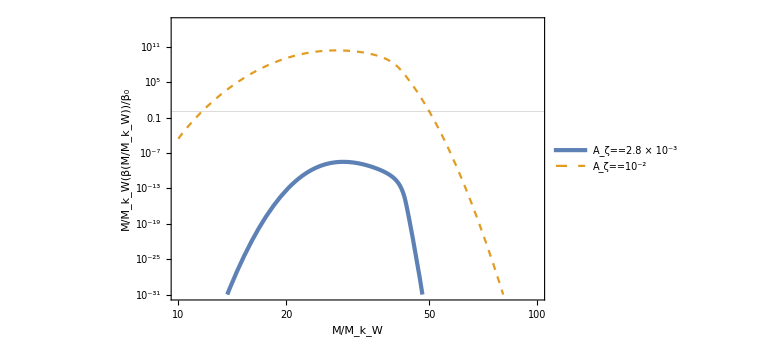

```mathematica
FigBeta=LogLogPlot[{MM nPBHint2[MM]/n2f,MM nPBHint1[MM]/n2f},{MM,10,100},PlotRange->{10^-31,10^15},GridLines->{None,{1}},FrameLabel->{Row[{M,"/",Subscript[M, Subscript[k, "W"]]}],Row[{M/Subscript[M, Subscript[k, "W"]],β[Row[{M,"/",Subscript[M, Subscript[k, "W"]]}]]/Subscript[β, 0]}]},PlotStyle->{AbsoluteThickness[3],Dashed},PlotLegends->Placed[LineLegend[{Row[{Subscript[A, ζ]==2.8," × ",Superscript[10,-3]}],Subscript[A, ζ]==Superscript[10,-2]},LabelStyle->Directive[Larger,Black,FontFamily->"Palatino"]],{0.82,0.85}]]
```

```mathematica
MaxfPBH=FindMaximum[MM nPBHint2[MM]/n2f,{MM,20},WorkingPrecision->30][[1]]
MaxMM=MM/.FindMaximum[MM nPBHint2[MM]/n2f,{MM,20},WorkingPrecision->30][[2]]
```

FindMaximum::precw: The precision of the argument function (-(5.73049×10^15 10^(«1») MM)) is less than WorkingPrecision (30.).

3.11903354176128427117906107374×10^-9

FindMaximum::precw: The precision of the argument function (-(5.73049×10^15 10^(«1») MM)) is less than WorkingPrecision (30.).

28.8015410141772332872142088305

InterpolatingFunction::dmval: Input value {0.0000612857} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::munfl: 1/10^2975.02 is too small to represent as a normalized machine number; precision may be lost.

InterpolatingFunction::dmval: Input value {0.0612858} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::munfl: 1/10^2529.91 is too small to represent as a normalized machine number; precision may be lost.

InterpolatingFunction::dmval: Input value {0.12251} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

General::munfl: 1/10^2133.67 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

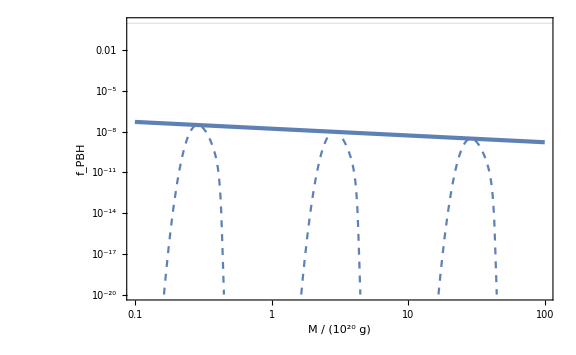

```mathematica
FigfPBH=LogLogPlot[{0.01^-0.5 MM/0.01 nPBHint2[MM/0.01]/n2f,0.1^-0.5 MM/0.1 nPBHint2[MM/0.1]/n2f,MM nPBHint2[MM]/n2f,MaxfPBH (MM/MaxMM)^(-1/2)},{MM,0.1,100},PlotRange->{10^-20,1},GridLines->{None,{1}},PlotStyle->{Dashed,{Color[1],Dashed},{Color[1],Dashed},{Color[1],AbsoluteThickness[3]}},FrameLabel->{Row[{M," / (",Superscript[10,20]," g)"}],Subscript[f, PBH]}]
```

#### Press-Schechter

```mathematica
WTH[z_]=3(Sin[z]-z Cos[z])/z^3;
TrsT[z_]=WTH[z/√3];
```

```mathematica
Integrand[z_]=WTH[k R]^2(k R)^4 TrsT[k R]^2/.{k->z/R}//Simplify
```

(243 (-z Cos[z]+Sin[z])^2 (√3 z Cos[z/(√3)]-3 Sin[z/(√3)])^2)/z^8

```mathematica
NIntegrate[Integrand[z] 1/z,{z,0,10^4}]
```

5.36981

```mathematica
sigmad2[As_]=16/81 As NIntegrate[Integrand[z] 1/z,{z,0,10^4}]
```

1.0607 As

```mathematica
betaPBH[As_]=1/2 Erfc[dth/(√(2sigmad2[As]))]/.{dth->0.267 2};
```

```mathematica
MPBH[R_]=10^20(R/(6.4 10^-14))^2;
```

```mathematica
fPBHPS[R_,As_]=betaPBH[As]/(7.2 10^-16)(MPBH[R]/10^20)^(-1/2);
```

```mathematica
{MPBH[R],fPBHPS[R,As]}/.{R->ks^-1}/.{ks->4.3 10^13,As->2.8 10^-3}
```

{1.32039×10^19,2.18112×10^-7}

```mathematica
fPBHPSList=Table[{MPBH[10^logR]/10^20,fPBHPS[10^logR,2.8 10^-3]},{logR,-Log10[4.3 10^13]-1,-Log10[4.3 10^13]+2,0.01}];
```

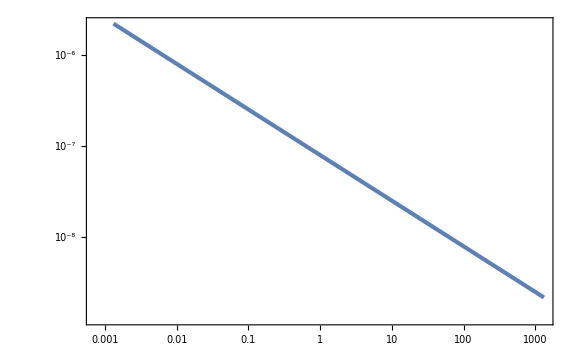

```mathematica
ListLogLogPlot[fPBHPSList]
```

InterpolatingFunction::dmval: Input value {0.0000612857} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::munfl: 1/10^2975.02 is too small to represent as a normalized machine number; precision may be lost.

InterpolatingFunction::dmval: Input value {0.0612858} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::munfl: 1/10^2529.91 is too small to represent as a normalized machine number; precision may be lost.

InterpolatingFunction::dmval: Input value {0.12251} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

General::munfl: 1/10^2133.67 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

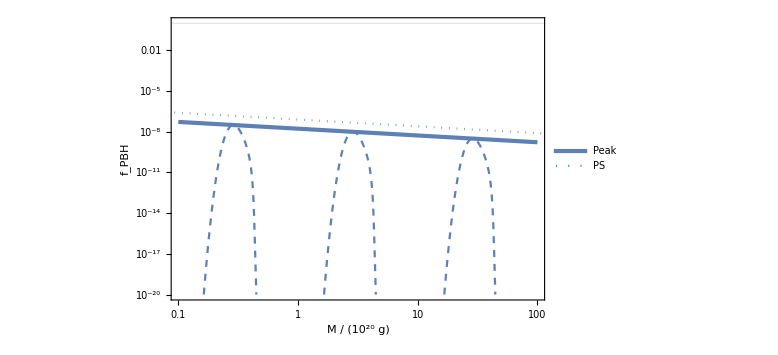

```mathematica
Show[LogLogPlot[{0.01^-0.5 MM/0.01 nPBHint2[MM/0.01]/n2f,0.1^-0.5 MM/0.1 nPBHint2[MM/0.1]/n2f,MM nPBHint2[MM]/n2f,MaxfPBH (MM/MaxMM)^(-1/2),0},{MM,0.1,100},PlotRange->{10^-20,1},GridLines->{None,{1}},PlotStyle->{Dashed,{Color[1],Dashed},{Color[1],Dashed},{Color[1],AbsoluteThickness[3]},{Color[1],Dotted}},PlotLegends->Placed[{None,None,None,"Peak","PS"},{0.8,0.8}],FrameLabel->{Row[{M," / (",Superscript[10,20]," g)"}],Subscript[f, PBH]}],ListLogLogPlot[fPBHPSList,PlotStyle->{Dotted}]]
```

### power law

```mathematica
Quit[]
```

```mathematica
$Assumptions={sg>0,ks>0,n≥1,ns>-2,As>0,kW>0,mu>0,kappa>0};
```

```mathematica
calPz[k_,As_,ks_,ns_]=As(k/ks)^ns;
```

```mathematica
sigman[n_,kW_,As_,ks_,ns_]=√Integrate[k^(2n)calPz[k,As,ks,ns] 1/k,{k,0,kW}]//Simplify
```

√((As ks^-ns kW^(2 n+ns))/(2 n+ns))

```mathematica
psin[n_,r_,kW_,ks_,ns_]=1/sigman[2,kW,As,ks,ns]^2 Integrate[k^(2n)Sin[k r]/(k r)calPz[k,As,ks,ns] 1/k,{k,0,kW}]//Simplify
```

(kW^(-4+2 n) (4+ns) HypergeometricPFQ[{n+ns/2},{3/2,1+n+ns/2},-1/4 kW^2 r^2])/(2 n+ns)

```mathematica
psin[1,r,kW,ks,ns]//Simplify
psin[2,r,kW,ks,ns]//Simplify
```

((4+ns) HypergeometricPFQ[{1+ns/2},{3/2,2+ns/2},-1/4 kW^2 r^2])/(kW^2 (2+ns))

HypergeometricPFQ[{2+ns/2},{3/2,3+ns/2},-1/4 kW^2 r^2]

```mathematica
gamma3[ns_]=sigman[3,kW,As,ks,ns]^2/(sigman[2,kW,As,ks,ns]sigman[4,kW,As,ks,ns])//Simplify
Rb[kW_,ns_]=√3 sigman[3,kW,As,ks,ns]/sigman[4,kW,As,ks,ns]//Simplify
```

(√((4+ns) (8+ns)))/(6+ns)

(√3 √((8+ns)/(6+ns)))/kW

```mathematica
zetabar[r_,kW_,ns_,mu2_,kb_]=mu2/(1-gamma3[ns]^2)(psin[1,r,kW,ks,ns]-1/3 Rb[kW,ns]^2 psin[2,r,kW,ks,ns])-mu2 kb^2 sigman[2,kW,As,ks,ns]/(sigman[4,kW,As,ks,ns]gamma3[ns](1-gamma3[ns]^2))(gamma3[ns]^2 psin[1,r,kW,ks,ns]-1/3 Rb[kW,ns]^2 psin[2,r,kW,ks,ns])//Simplify
```

1/(4 kW^4)mu2 (6+ns)^2 ((kW^2 (4+ns) HypergeometricPFQ[{1+ns/2},{3/2,2+ns/2},-1/4 kW^2 r^2])/(2+ns)-(kW^2 (8+ns) HypergeometricPFQ[{2+ns/2},{3/2,3+ns/2},-1/4 kW^2 r^2])/(6+ns)-(kb^2 (8+ns) ((4+ns)^2 HypergeometricPFQ[{1+ns/2},{3/2,2+ns/2},-1/4 kW^2 r^2]-(12+8 ns+ns^2) HypergeometricPFQ[{2+ns/2},{3/2,3+ns/2},-1/4 kW^2 r^2]))/((2+ns) (4+ns) (6+ns)))

```mathematica
zetax[x_,ns_,mu_,kappa_]=zetabar[x/kW,kW,ns,mu kW^2,kappa kW]//FullSimplify
```

(mu (6+ns) (-((4+ns)^2 (-6-ns+kappa^2 (8+ns)) HypergeometricPFQ[{1+ns/2},{3/2,2+ns/2},-x^2/4])/(2+ns)+(8+ns) (-4-ns+kappa^2 (6+ns)) HypergeometricPFQ[{2+ns/2},{3/2,3+ns/2},-x^2/4]))/(4 (4+ns))

```mathematica
CompactC[x_,ns_,mu_,kappa_]=(1-(1+x D[zetax[x,ns,mu,kappa], x])^2)/3//Simplify
```

1/3 (1-(1-1/(4 x)mu (6+ns) ((4+ns) (6+ns-kappa^2 (8+ns)) (x HypergeometricPFQ[{1+ns/2},{3/2,2+ns/2},-x^2/4]-Sin[x])+(8+ns) (-4-ns+kappa^2 (6+ns)) (x HypergeometricPFQ[{2+ns/2},{3/2,3+ns/2},-x^2/4]-Sin[x])))^2)

```mathematica
xmcond[x_,ns_,kappa_]=(D[zetax[x,ns,mu,kappa], x]+x D[D[zetax[x,ns,mu,kappa], x], x])/mu//Simplify
```

-1/(4 x^2)(6+ns) (-2 (-4-ns+kappa^2 (8+ns)) x Cos[x]+(8+6 ns+ns^2) (-6-ns+kappa^2 (8+ns)) x HypergeometricPFQ[{1+ns/2},{3/2,2+ns/2},-x^2/4]-(32+12 ns+ns^2) (-4-ns+kappa^2 (6+ns)) x HypergeometricPFQ[{2+ns/2},{3/2,3+ns/2},-x^2/4]+2 (-44-19 ns-2 ns^2+kappa^2 (72+25 ns+2 ns^2)) Sin[x])

```mathematica
FindRoot[xmcond[x,-1/2,kappa]==0,{x,Min[3/kappa,5]},WorkingPrecision->30]/.{kappa->10^-1}
```

FindRoot::srect: Value Min[5.,3./kappa] in search specification {x,Min[3/kappa,5]} is not a number or array of numbers.

{x→5.58273667673438840904381471746}

```mathematica
xmList=Flatten[ParallelTable[{10^logk,ns,x/.FindRoot[xmcond[x,ns,10^logk]==0,{x,Min[3/10^logk,5]},WorkingPrecision->30]},{logk,-3,2,10^-1},{ns,-19/10,2,10^-1}],1];//AbsoluteTiming
```

{4.49837,Null}

```mathematica
xmint[kappa_,ns_]=Interpolation[xmList][kappa,ns];
```

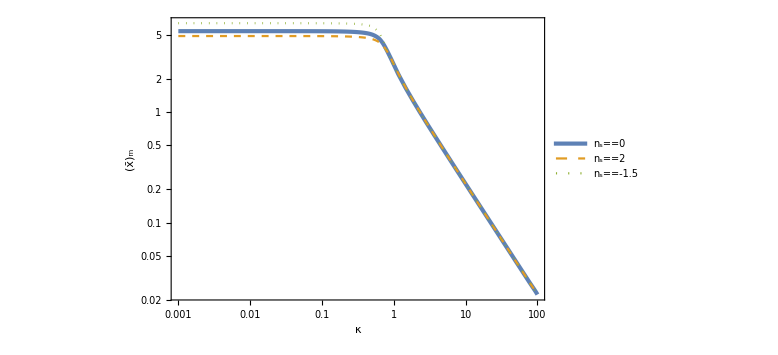

```mathematica
LogLogPlot[{xmint[kappa,0],xmint[kappa,2],xmint[kappa,-1.5]},{kappa,10^-3,10^2},PlotStyle->{AbsoluteThickness[3],Dashed,Dotted},PlotLegends->Placed[{Subscript[n, "s"]==0,Subscript[n, "s"]==2,Subscript[n, "s"]==-1.5},{0.25,0.3}],FrameLabel->{κ,Subscript[OverBar[x], "m"]}]
```

```mathematica
Cmax[mu_,kappa_,ns_]=CompactC[xmint[kappa,ns],ns,mu,kappa];
```

```mathematica
muthList=Flatten[ParallelTable[{10^logk,ns,mu/.Solve[Cmax[mu,10^logk,ns]==0.267,mu][[1]]},{logk,-3,2,10^-1},{ns,-19/10,2,10^-1}],1];//AbsoluteTiming
```

{5.41555,Null}

```mathematica
muthint[kappa_,ns_]=Interpolation[muthList][kappa,ns];
```

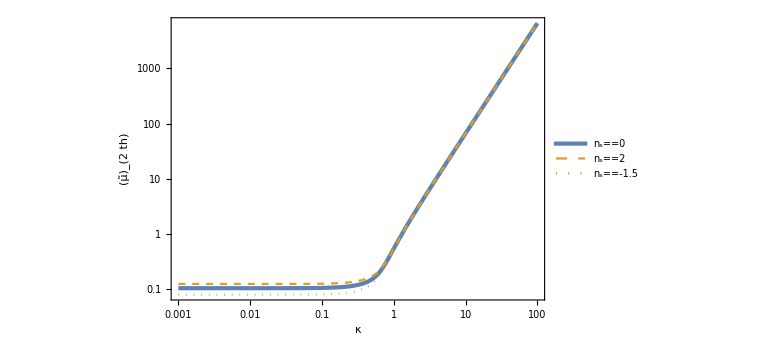

```mathematica
LogLogPlot[{muthint[kappa,0],muthint[kappa,2],muthint[kappa,-1.5]},{kappa,10^-3,10^2},PlotStyle->{AbsoluteThickness[3],Dashed,Dotted},PlotLegends->Placed[{Subscript[n, "s"]==0,Subscript[n, "s"]==2,Subscript[n, "s"]==-1.5},{0.25,0.7}],FrameLabel->{κ,Subscript[OverTilde[μ], 2th]}]
```

```mathematica
gm[kappa_,ns_]=zetax[xmint[kappa,ns],ns,mu,kappa]/mu//Simplify;
```

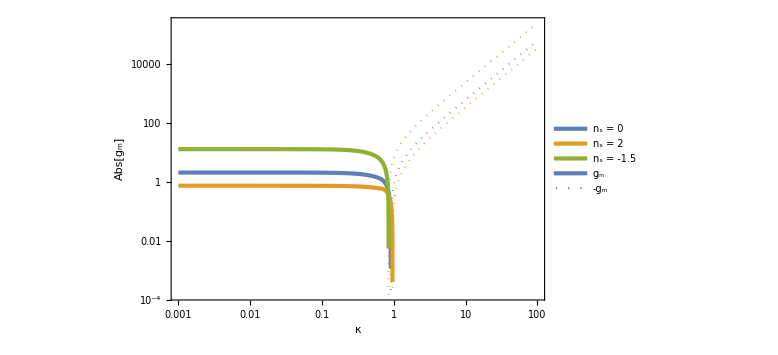

```mathematica
Show[LogLogPlot[{gm[kappa,0],-gm[kappa,0],gm[kappa,2],-gm[kappa,2],gm[kappa,-1.5],-gm[kappa,-1.5]},{kappa,10^-3,10^2},FrameLabel->{κ,Abs[Subscript[g, "m"]]},PlotStyle->{AbsoluteThickness[3],{Color[1],Dotted},{Color[2],AbsoluteThickness[3]},{Color[2],Dotted},{Color[3],AbsoluteThickness[3]},{Color[3],Dotted}},PlotLegends->Placed[LineLegend[{"n_s = 0",None,"n_s = 2",None,"n_s = -1.5",None},LegendLayout->"Row",LabelStyle->Directive[Black,Larger,FontFamily->"Palatino"],LegendMarkerSize->20],{0.3,0.8}]],LogLogPlot[{0,0},{kappa,0.001,100},PlotStyle->{{Color[1],AbsoluteThickness[3]},{Color[1],Dotted}},PlotLegends->Placed[LineLegend[{"g_m",-"g_m"},LegendLayout->"Row",LabelStyle->Directive[Black,Larger,FontFamily->"Palatino"],LegendMarkerSize->20],{0.3,0.7}]]]
```

```mathematica
kappacList=Table[{ns,kappa/.FindRoot[gm[kappa,ns]==0,{kappa,1}]},{ns,-19/10,2,10^-1}];//AbsoluteTiming
```

{0.900001,Null}

```mathematica
kappacint[ns_]=Interpolation[kappacList][ns];
```

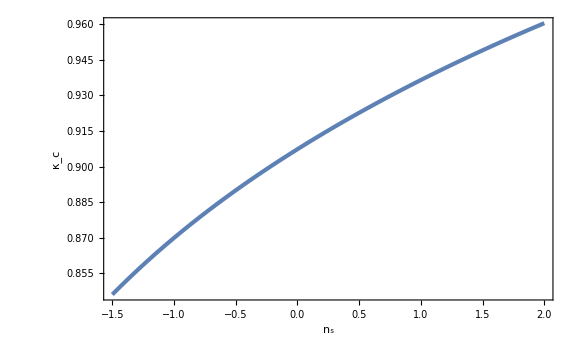

```mathematica
Plot[kappacint[ns],{ns,-1.5,2},FrameLabel->{Subscript[n, "s"],Subscript[κ, "c"]}]
```

```mathematica
MoMkW[mu_,kappa_,ns_]=xmint[kappa,ns]^2 Exp[2mu gm[kappa,ns]];
```

```mathematica
MContour0=Table[i,{i,-5,5,1/4}];
MContourm=Table[i,{i,-20,20}];
MContourp=Table[i,{i,-5,5,1/5}];
```

```mathematica
Show[ContourPlot[Log10[MoMkW[10^logm,10^logk,0]],{logk,-3,0.5},{logm,-2,0.5},Contours->MContour0,PlotLegends->BarLegend[Automatic,LegendLabel->Row[{Subscript["log", 10],M[Subscript[OverTilde[μ], 2],κ]/Subscript[M, Subscript[k, "W"]]}]],GridLines->{{Log10[kappacint[0]]},None},GridLinesStyle->Directive[Black,Dotted,AbsoluteThickness[2]],FrameLabel->{{Subscript["log", 10] Subscript[OverTilde[μ], 2],None},{Row[{Subscript["log", 10]," ",κ}],Subscript[n, "s"]==0}}],ContourPlot[MoMkW[10^logm,10^logk,0]==MoMkW[muthint[10^-3,0],10^-3,0],{logk,-3,0.5},{logm,-2,0.5},ContourStyle->{Black,AbsoluteThickness[2]}],Plot[Log10[muthint[10^logk,0]],{logk,-3,2},PlotStyle->{AbsoluteThickness[3],Color[4]}]]
```

-Graphics-

```mathematica
FigMoMkWm=Show[ContourPlot[Log10[MoMkW[10^logm,10^logk,-1.5]],{logk,-3,0.5},{logm,-2,0.5},Contours->MContourm,PlotLegends->BarLegend[Automatic,LegendLabel->Row[{Subscript["log", 10],M[Subscript[OverTilde[μ], 2],κ]/Subscript[M, Subscript[k, "W"]]}]],GridLines->{{Log10[kappacint[-1.5]]},None},GridLinesStyle->Directive[Black,Dotted,AbsoluteThickness[2]],FrameLabel->{{Subscript["log", 10] Subscript[OverTilde[μ], 2],None},{Row[{Subscript["log", 10]," ",κ}],Subscript[n, "s"]==-1.5}}],ContourPlot[MoMkW[10^logm,10^logk,-1.5]==MoMkW[muthint[10^-3,-1.5],10^-3,-1.5],{logk,-3,0.5},{logm,-2,0.5},ContourStyle->{Black,AbsoluteThickness[2]}],Plot[Log10[muthint[10^logk,-1.5]],{logk,-3,2},PlotStyle->{AbsoluteThickness[3],Color[4]}]]
```

-Graphics-

```mathematica
FigMoMkWp=Show[ContourPlot[Log10[MoMkW[10^logm,10^logk,2]],{logk,-3,0.5},{logm,-2,0.5},Contours->MContourp,PlotLegends->BarLegend[Automatic,LegendLabel->Row[{Subscript["log", 10],M[Subscript[OverTilde[μ], 2],κ]/Subscript[M, Subscript[k, "W"]]}]],GridLines->{{Log10[kappacint[2]]},None},GridLinesStyle->Directive[Black,Dotted,AbsoluteThickness[2]],FrameLabel->{{Subscript["log", 10] Subscript[OverTilde[μ], 2],None},{Row[{Subscript["log", 10]," ",κ}],Subscript[n, "s"]==2}}],ContourPlot[MoMkW[10^logm,10^logk,2]==MoMkW[muthint[10^-3,2],10^-3,2],{logk,-3,0.5},{logm,-2,0.5},ContourStyle->{Black,AbsoluteThickness[2]}],Plot[Log10[muthint[10^logk,2]],{logk,-3,2},PlotStyle->{AbsoluteThickness[3],Color[4]}]]
```

-Graphics-

```mathematica
(*Export["MoMkW_m1,5.pdf",FigMoMkWm];
Export["MoMkW_p2.pdf",FigMoMkWp];*)
```

```mathematica
Mc[ns_]=MoMkW[0.1,kappacint[ns],ns];
Mth[ns_]=MoMkW[muthint[10^-3,ns],10^-3,ns];
```

```mathematica
Mc[-1.5]
Mth[-1.5]
Mc[2]
Mth[2]
```

11.1265

292.702

8.10472

28.1231

```mathematica
muM[kappa_,ns_,MM_]=1/(2gm[kappa,ns])Log[MM/xmint[kappa,ns]^2];
```

```mathematica
FindRoot[muM[kappa,-1.5,0.9Mth[-1.5]]==muthint[kappa,-1.5],{kappa,0.9kappacint[-1.5]}]
```

{kappa→0.555554}

```mathematica
FindRoot[muM[kappa,-1.5,0.001]==muthint[kappa,-1.5],{kappa,1.1kappacint[-1.5]}]
```

{kappa→1.02839}

```mathematica
FindRoot[muM[kappa,2,0.9Mth[2]]==muthint[kappa,2],{kappa,0.9kappacint[2]}]
```

{kappa→0.53093}

```mathematica
FindRoot[muM[kappa,2,0.001]==muthint[kappa,2],{kappa,1.1kappacint[2]}]
```

{kappa→1.43857}

```mathematica
FindRoot[muM[kappa,-1.5,100]==muthint[kappa,-1.5],{kappa,0.8kappacint[-1.5]},WorkingPrecision->30]
```

FindRoot::precw: The precision of the argument function ((1.11111 Log[100/(InterpolatingFunction[«1»][kappa,-1.5])^2])/(-12.5 (-4.5+6.5 Power[«2»]) HypergeometricPFQ[{0.25},{3/2,1.25},-1/4 Power[«2»]]+6.5 (-2.5+4.5 Power[«2»]) HypergeometricPFQ[{1.25},{3/2,2.25},-1/4 Power[«2»]])==«1») is less than WorkingPrecision (30.).

{kappa→0.73822448377197264289745889825}

```mathematica
kappathList1=Flatten[ParallelTable[{ns,logM,kappa/.FindRoot[muM[kappa,ns,10^logM]==muthint[kappa,ns],{kappa,0.999kappacint[ns]}]},{ns,-19/10,2,10^-1},{logM,Log10[Mc[ns]]+10^-3,Log10[Mth[ns]],10^-2}],1];//AbsoluteTiming
```

{46.4885,Null}

```mathematica
kappathList2=Flatten[Table[{ns,logM,kappa/.FindRoot[muM[kappa,ns,10^logM]==muthint[kappa,ns],{kappa,1.001kappacint[ns]}]},{ns,-19/10,2,10^-1},{logM,-3,Log10[Mc[ns]],10^-1}],1];//AbsoluteTiming
```

{61.7697,Null}

```mathematica
kappathList=Sort[Join[kappathList1,kappathList2]];
```

```mathematica
kappathint[ns_,MM_]=Interpolation[kappathList][ns,Log10[MM]];
```

Interpolation::udeg: Interpolation on unstructured grids is currently only supported for InterpolationOrder->1 or InterpolationOrder->All. Order will be reduced to 1.

InterpolatingFunction::femdmval: Input value {2.,1.44906} lies outside the range of data in the interpolating function.

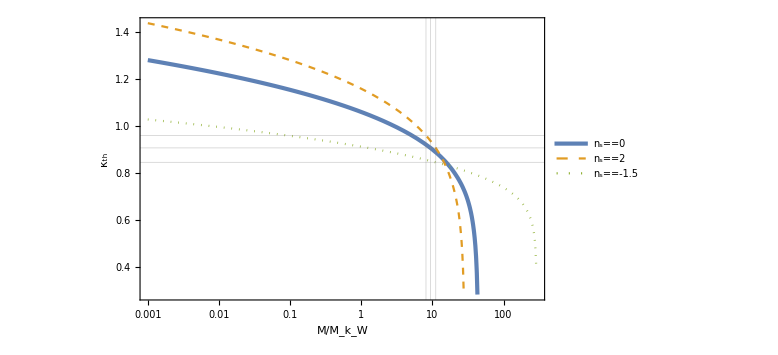

```mathematica
Show[LogLinearPlot[{kappathint[0,MM],0,0},{MM,10^-3,Mth[0]},GridLines->{{Mc[-1.5],Mc[0],Mc[2]},{kappacint[-1.5],kappacint[0],kappacint[2]}},PlotRange->{{10^-3,Mth[-1.5]},{kappathint[2,Mth[2]],kappathint[2,10^-3]}},FrameLabel->{Row[{M,"/",Subscript[M, Subscript[k, "W"]]}],Subscript[κ, th]},PlotLegends->Placed[{Subscript[n, "s"]==0,Subscript[n, "s"]==2,Subscript[n, "s"]==-1.5},{0.2,0.25}],PlotStyle->{AbsoluteThickness[3],Dashed,Dotted}],LogLinearPlot[kappathint[2,MM],{MM,10^-3,Mth[2]},PlotStyle->{Color[2],Dashed}],LogLinearPlot[kappathint[-1.5,MM],{MM,10^-3,Mth[-1.5]},PlotStyle->{Color[3],Dotted}]]
```

```mathematica
sigmamu=(kW^4/sigman[2,kW,As,ks,ns]^2)^(-1/2)/.{As->calPzW (kW/ks)^-ns}//Simplify
```

1/(√((4+ns)/calPzW))

```mathematica
kappa2mean=sigman[3,kW,As,ks,ns]^2/sigman[2,kW,As,ks,ns]^2 1/kW^2//Simplify
```

(4+ns)/(6+ns)

```mathematica
sigmakappa=((mu^2 kW^4 kW^4)/(sigman[4,kW,As,ks,ns]^2(1-gamma3[ns]^2)))^(-1/2)/.{As->calPzW (kW/ks)^-ns}//Simplify
```

2/(√((mu^2 (6+ns)^2 (8+ns))/calPzW))

```mathematica
CC=1/kW^3(2 3^(3/2))/(2π)^(3/2)mu kW^2 kappa kW sigman[4,kW,As,ks,ns]^2/(sigman[2,kW,As,ks,ns] sigman[3,kW,As,ks,ns]^3)(sigmamu sigmakappa)/(√(1-gamma3[ns]^2))kW^3/.{As->calPzW (kW/ks)^-ns}//Simplify
```

3 √(3/2) kappa ((6+ns)/(8 π+ns π))^(3/2)

```mathematica
zz=(mu kW^2 kappa^2 kW^2)/sigman[4,kW,As,ks,ns]/.{As->calPzW (kW/ks)^-ns}//Simplify
```

(kappa^2 mu)/(√(calPzW/(8+ns)))

```mathematica
f[z_]=1/2 z(z^2-3)(Erf[1/2 √(5/2)z]+Erf[√(5/2)z])+√(2/(5π))((8/5+31/4 z^2)Exp[-5/8 z^2]+(-8/5+1/2 z^2)Exp[-5/2 z^2]);
PG[z_,m_,s2_]=1/(√(2π s2))Exp[(-(z-m)^2)/(2s2)];
```

```mathematica
npk[mu_,kappa_,As_,ks_,kW_,ns_]=CC f[zz]PG[mu,0,sigmamu^2]PG[kappa^2,kappa2mean,sigmakappa^2]kappa/.{calPzW->calPz[kW,As,ks,ns]}//Simplify;
```

```mathematica
nPBH[MM_,As_,ks_,kW_,ns_]:=NIntegrate[2gm[kappa,ns]npk[muM[kappa,ns,MM],kappa,As,ks,kW,ns],{kappa,kappacint[ns],kappathint[ns,MM]}]/;MM<Mc[ns]
nPBH[MM_,As_,ks_,kW_,ns_]:=NIntegrate[2gm[kappa,ns]npk[muM[kappa,ns,MM],kappa,As,ks,kW,ns],{kappa,kappathint[ns,MM],kappacint[ns]}]/;Mc[ns]<MM<Mth[ns]
nPBH[MM_,As_,ks_,kW_,ns_]:=NIntegrate[2gm[kappa,ns]npk[muM[kappa,ns,MM],kappa,As,ks,kW,ns],{kappa,0,kappacint[ns]}]/;MM>Mth[ns]
```

```mathematica
k20=1.56 10^13;
```

```mathematica
nPBHListRedp=ParallelTable[{10^logM,nPBH[10^logM,2.8 10^-3,k20,√10 k20,-0.2]//Quiet},{logM,1,2,10^-2}];//AbsoluteTiming
nPBHListRed0=ParallelTable[{10^logM,nPBH[10^logM,2.8 10^-3,k20,k20,-0.2]//Quiet},{logM,1,2,10^-2}];//AbsoluteTiming
nPBHListRedm=ParallelTable[{10^logM,nPBH[10^logM,2.8 10^-3,k20,k20/√10,-0.2]//Quiet},{logM,1,2,10^-2}];//AbsoluteTiming
```

{47.7665,Null}

{47.6731,Null}

{47.8111,Null}

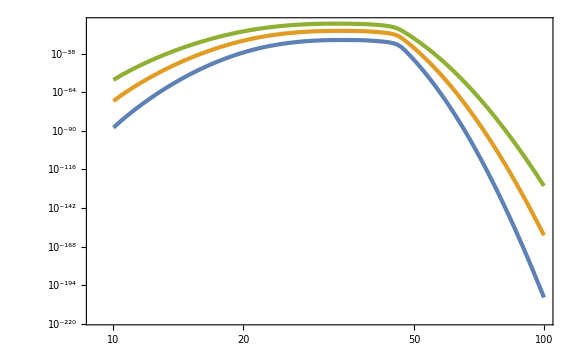

```mathematica
ListLogLogPlot[{nPBHListRedp,nPBHListRed0,nPBHListRedm}]
```

```mathematica
nPBHListBluep=ParallelTable[{10^logM,nPBH[10^logM,2.8 10^-3,k20,√10 k20,0.2]//Quiet},{logM,1,2,10^-2}];//AbsoluteTiming
nPBHListBlue0=ParallelTable[{10^logM,nPBH[10^logM,2.8 10^-3,k20,k20,0.2]//Quiet},{logM,1,2,10^-2}];//AbsoluteTiming
nPBHListBluem=ParallelTable[{10^logM,nPBH[10^logM,2.8 10^-3,k20,k20/√10,0.2]//Quiet},{logM,1,2,10^-2}];//AbsoluteTiming
```

{51.2338,Null}

{51.097,Null}

{51.1844,Null}

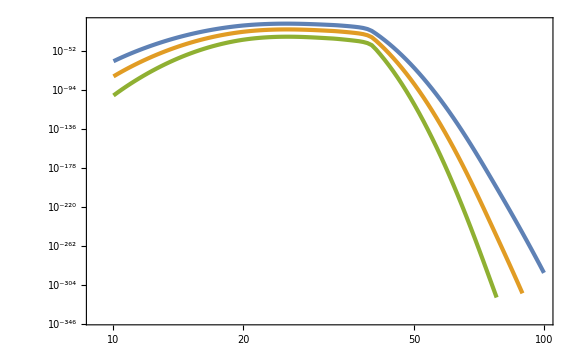

```mathematica
ListLogLogPlot[{nPBHListBluep,nPBHListBlue0,nPBHListBluem}]
```

```mathematica
gineV=(1.783 10^-33)^-1;
MpcinvineV=(10^6 3.086 10^16)^-1 1.973 10^-7;
KineV=(1.16 10^4)^-1;
MplineV=2.435 10^(18+9);
kminvsinvMpcineV=(10^3 6.582 10^-16)/(3.086 10^16 10^6);
```

```mathematica
n2f=((10^20 gineV (1.56 10^13 MpcinvineV)^3)/(0.12 3 MplineV^2(100kminvsinvMpcineV)^2))^-1
```

1.74505×10^-16

```mathematica
LognPBHListRedp=Map[Log10,nPBHListRedp,{2}]//Simplify;
LognPBHListRed0=Map[Log10,nPBHListRed0,{2}]//Simplify;
LognPBHListRedm=Map[Log10,nPBHListRedm,{2}]//Simplify;
```

```mathematica
nPBHintRedp[MM_]=10^(Interpolation[LognPBHListRedp][Log10[MM]]);
nPBHintRed0[MM_]=10^(Interpolation[LognPBHListRed0][Log10[MM]]);
nPBHintRedm[MM_]=10^(Interpolation[LognPBHListRedm][Log10[MM]]);
```

```mathematica
LognPBHListBluep=Map[Log10,nPBHListBluep,{2}]//Simplify;
LognPBHListBlue0=Map[Log10,nPBHListBlue0,{2}]//Simplify;
LognPBHListBluem=Map[Log10,nPBHListBluem,{2}]//Simplify;
```

```mathematica
nPBHintBluep[MM_]=10^(Interpolation[LognPBHListBluep][Log10[MM]]);
nPBHintBlue0[MM_]=10^(Interpolation[LognPBHListBlue0][Log10[MM]]);
nPBHintBluem[MM_]=10^(Interpolation[LognPBHListBluem][Log10[MM]]);
```

```mathematica
MkW[kW_]=10^20(kW/k20)^-2;
```

```mathematica
fPBHRedp[MM_]=(MkW[√10 k20]/10^20)^(-1/2)(MM MkW[k20]/MkW[√10 k20] nPBHintRedp[MM MkW[k20]/MkW[√10 k20]])/n2f;
fPBHRed0[MM_]=(MkW[k20]/10^20)^(-1/2)(MM nPBHintRed0[MM])/n2f;
fPBHRedm[MM_]=(MkW[k20/√10]/10^20)^(-1/2)(MM MkW[k20]/MkW[k20/√10] nPBHintRedm[MM MkW[k20]/MkW[k20/√10]])/n2f;
```

```mathematica
fPBHBluep[MM_]=(MkW[√10 k20]/10^20)^(-1/2)(MM MkW[k20]/MkW[√10 k20] nPBHintBluep[MM MkW[k20]/MkW[√10 k20]])/n2f;
fPBHBlue0[MM_]=(MkW[k20]/10^20)^(-1/2)(MM nPBHintBlue0[MM])/n2f;
fPBHBluem[MM_]=(MkW[k20/√10]/10^20)^(-1/2)(MM MkW[k20]/MkW[k20/√10] nPBHintBluem[MM MkW[k20]/MkW[k20/√10]])/n2f;
```

```mathematica
MmaxRedp=MM/.FindMaximum[fPBHRedp[MM],{MM,3},WorkingPrecision->30][[2]]
MmaxRed0=MM/.FindMaximum[fPBHRed0[MM],{MM,30}][[2]]
MmaxRedm=MM/.FindMaximum[fPBHRedm[MM],{MM,300}][[2]]
```

3.43898760913397611899994059905

33.795

332.638

```mathematica
fPBHmaxRedp=FindMaximum[fPBHRedp[MM],{MM,3},WorkingPrecision->30][[1]]
fPBHmaxRed0=FindMaximum[fPBHRed0[MM],{MM,30}][[1]]
fPBHmaxRedm=FindMaximum[fPBHRedm[MM],{MM,300}][[1]]
```

7.68187799382275832583332948823×10^-12

3.32861×10^-6

0.0742487

```mathematica
fPBHRedList=Map[Log10,{{MmaxRedp,fPBHmaxRedp},{MmaxRed0,fPBHmaxRed0},{MmaxRedm,fPBHmaxRedm}},{2}];
fPBHRedint[MM_]=10^(Interpolation[fPBHRedList][Log10[MM]]);
```

```mathematica
MmaxBluep=MM/.FindMaximum[fPBHBluep[MM],{MM,3},WorkingPrecision->30][[2]]
MmaxBlue0=MM/.FindMaximum[fPBHBlue0[MM],{MM,30},WorkingPrecision->30][[2]]
MmaxBluem=MM/.FindMaximum[fPBHBluem[MM],{MM,300},WorkingPrecision->50][[2]]
```

2.53603891095715268589213408005

25.430426591143034432750916966

254.88331693368291346403772199859109249398092270515

```mathematica
fPBHmaxBluep=FindMaximum[fPBHBluep[MM],{MM,3},WorkingPrecision->30][[1]]
fPBHmaxBlue0=FindMaximum[fPBHBlue0[MM],{MM,30},WorkingPrecision->30][[1]]
fPBHmaxBluem=FindMaximum[fPBHBluem[MM],{MM,300},WorkingPrecision->50][[1]]
```

5.82358813393036278090263216836×10^-6

1.16602367016177934833147031619×10^-12

5.2966402525789846961442416861162643296542679374004×10^-21

```mathematica
fPBHBlueList=Map[Log10,{{MmaxBluep,fPBHmaxBluep},{MmaxBlue0,fPBHmaxBlue0},{MmaxBluem,fPBHmaxBluem}},{2}];
fPBHBlueint[MM_]=10^(Interpolation[fPBHBlueList][Log10[MM]]);
```

```mathematica
fPBHflat[MM_]=3.1190335417612842711790610737385686790601101939361`30.*^-9(MM/(28.80154101417723328721420883047391386046`30.))^(-1/2);
```

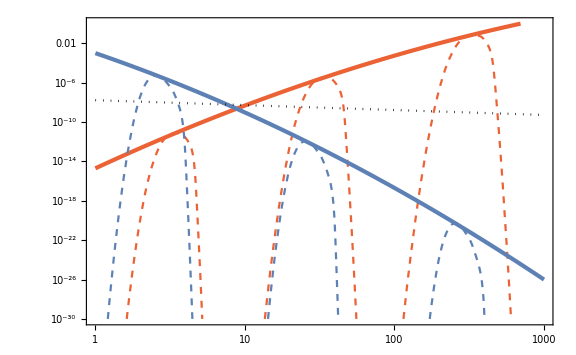

```mathematica
LogLogPlot[{fPBHRedp[MM]UnitStep[50-MM],fPBHRed0[MM],fPBHRedm[MM],fPBHRedint[MM],fPBHBluep[MM],fPBHBlue0[MM],fPBHBluem[MM],fPBHBlueint[MM],fPBHflat[MM]},{MM,1,10^3},PlotRange->{10^-30,1},PlotStyle->{{Color[4],Dashed},{Color[4],Dashed},{Color[4],Dashed},{Color[4],AbsoluteThickness[3]},{Color[1],Dashed},{Color[1],Dashed},{Color[1],Dashed},{Color[1],AbsoluteThickness[3]},{Black,Dotted}}]
```

#### Press-Schechter

```mathematica
WTH[z_]=3(Sin[z]-z Cos[z])/z^3;
TrsT[z_]=WTH[z/√3];
```

```mathematica
calPz[k,As,ks,ns]
```

As (k/ks)^ns

```mathematica
sigmad2[As_,ks_,ns_,R_]:=16/81 NIntegrate[calPz[k,As,ks,ns] WTH[k R]^2(k R)^4 TrsT[k R]^2 1/k,{k,0,10^4 R^-1}]
```

```mathematica
sigmad2[2.8 10^-3,k20,-0.2,1/k20]
```

0.00255182

```mathematica
betaPBH[As_,ks_,ns_,R_]:=1/2 Erfc[dth/(√(2sigmad2[As,ks,ns,R]))]/.{dth->0.267 2}
```

```mathematica
MPBH[R_]=10^20(R/(6.4 10^-14))^2;
```

```mathematica
fPBHPS[R_,As_,ks_,ns_]:=betaPBH[As,ks,ns,R]/(7.2 10^-16)(MPBH[R]/10^20)^(-1/2);
```

```mathematica
{MPBH[R],fPBHPS[R,As,ks,ns]}/.{R->ks^-1}/.{ks->4.3 10^13,As->2.8 10^-3,ns->0.2}
```

{1.32039×10^19,0.000264562}

```mathematica
fPBHPSListRed=ParallelTable[{MPBH[10^logR]/10^20,fPBHPS[10^logR,2.8 10^-3,k20,-0.2]},{logR,-Log10[4.3 10^13]-1,-Log10[4.3 10^13]+2,0.01}];
fPBHPSListBlue=ParallelTable[{MPBH[10^logR]/10^20,fPBHPS[10^logR,2.8 10^-3,k20,0.2]},{logR,-Log10[4.3 10^13]-1,-Log10[4.3 10^13]+2,0.01}];
```

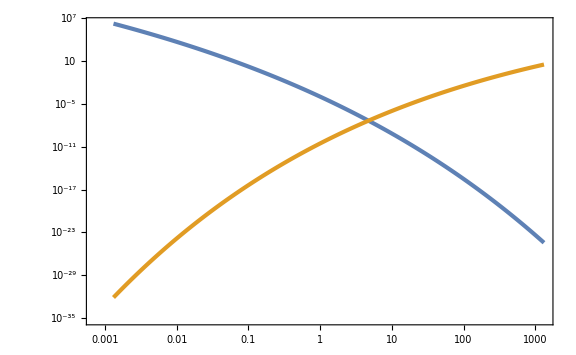

```mathematica
ListLogLogPlot[{fPBHPSListBlue,fPBHPSListRed}]
```

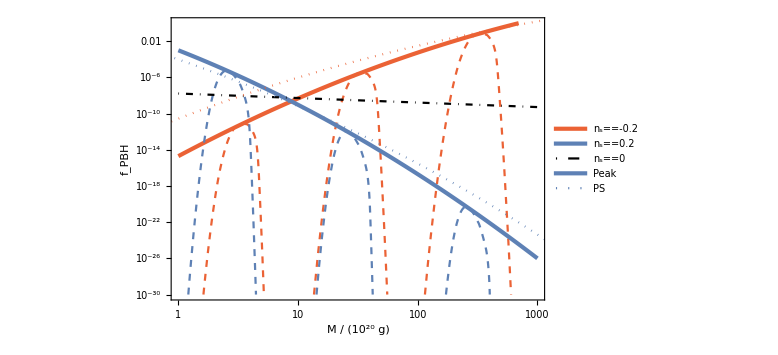

```mathematica
Show[LogLogPlot[{fPBHRedp[MM]UnitStep[50-MM],fPBHRed0[MM],fPBHRedm[MM],fPBHRedint[MM],fPBHBluep[MM],fPBHBlue0[MM],fPBHBluem[MM],fPBHBlueint[MM],fPBHflat[MM],0,0},{MM,1,10^3},PlotRange->{10^-30,1},PlotStyle->{{Color[4],Dashed},{Color[4],Dashed},{Color[4],Dashed},{Color[4],AbsoluteThickness[3]},{Color[1],Dashed},{Color[1],Dashed},{Color[1],Dashed},{Color[1],AbsoluteThickness[3]},{Black,DotDashed},{Color[1],AbsoluteThickness[3]},{Color[1],Dotted}},FrameLabel->{{Subscript[f, PBH],None},{Row[{M," / (",Superscript[10,20]," g)"}],Row[{Subscript[A, ζ]==2.8," × ",Superscript[10,-3]}]}},PlotLegends->Placed[LineLegend[{None,None,None,Subscript[n, "s"]==-0.2,None,None,None,Subscript[n, "s"]==0.2,Subscript[n, "s"]==0,"Peak","PS"},LegendFunction->(Framed[#1,Background->White]&),LabelStyle->Directive[Black,Larger,FontFamily->"Palatino"],LegendMarkerSize->20,LegendLayout->{"Column",2}],{0.22,0.2}]],ListLogLogPlot[{fPBHPSListRed,fPBHPSListBlue},PlotStyle->{{Color[4],Dotted},{Color[1],Dotted}}]]
```

### broken power-law

```mathematica
Quit[]
```

```mathematica
$Assumptions={r>0,sg>0,ks>0,n≥1,As>0,kW>0,x>0,mu>0,kappa>0,kappas>0};
```

```mathematica
calPz[k_,ks_,As_]=As((k/ks)^(3/2)UnitStep[ks-k]+(k/ks)^(-1/5)(1-UnitStep[ks-k]));
```

```mathematica
sigman[n_,kW_,As_,ks_]=√Integrate[k^(2n)calPz[k,ks,As] 1/k,{k,0,kW}]//Simplify
```

Piecewise[{{(√2 kW^(3/4+n) √(As/(3+4 n)))/ks^(3/4), ks≥kW}, {√((As (-17 ks^(2 n) kW^(1/5)+5 ks^(1/5) kW^(2 n) (3+4 n)))/(kW^(1/5) (-3+26 n+40 n^2))), True}}]

```mathematica
psin[n_,r_,kW_,kappas_]=1/sigman[2,kW,As,ks]^2 Integrate[k^(2n)Sin[k r]/(k r)calPz[k,ks,As] 1/k,{k,0,kW}]//Simplify
```

Piecewise[{{(11 kW^(-4+2 n) HypergeometricPFQ[{3/4+n},{3/2,7/4+n},-1/4 kW^2 r^2])/(3+4 n), ks≥kW}, {(209 ((5 ks^(2 n) HypergeometricPFQ[{-1/10+n},{3/2,9/10+n},-1/4 ks^2 r^2])/(1-10 n)+(5 ks^(1/5) kW^(-1/5+2 n) HypergeometricPFQ[{-1/10+n},{3/2,9/10+n},-1/4 kW^2 r^2])/(-1+10 n)+(2 ks^(2 n) HypergeometricPFQ[{3/4+n},{3/2,7/4+n},-1/4 ks^2 r^2])/(3+4 n)))/(-17 ks^4+55 (ks kW^19)^(1/5)), True}}]

```mathematica
psin[1,r,kW,ks]//Simplify
psin[2,r,kW,ks]//Simplify
```

Piecewise[{{(11 HypergeometricPFQ[{7/4},{3/2,11/4},-1/4 kW^2 r^2])/(7 kW^2), ks≥kW}, {(209 (-5/9 ks^2 HypergeometricPFQ[{9/10},{3/2,19/10},-1/4 ks^2 r^2]+5/9 (ks kW^9)^(1/5) HypergeometricPFQ[{9/10},{3/2,19/10},-1/4 kW^2 r^2]+2/7 ks^2 HypergeometricPFQ[{7/4},{3/2,11/4},-1/4 ks^2 r^2]))/(-17 ks^4+55 (ks kW^19)^(1/5)), True}}]

Piecewise[{{HypergeometricPFQ[{11/4},{3/2,15/4},-1/4 kW^2 r^2], ks≥kW}, {(-55 ks^4 HypergeometricPFQ[{19/10},{3/2,29/10},-1/4 ks^2 r^2]+55 (ks kW^19)^(1/5) HypergeometricPFQ[{19/10},{3/2,29/10},-1/4 kW^2 r^2]+38 ks^4 HypergeometricPFQ[{11/4},{3/2,15/4},-1/4 ks^2 r^2])/(-17 ks^4+55 (ks kW^19)^(1/5)), True}}]

```mathematica
gamma3[kW_,ks_]=sigman[3,kW,As,ks]^2/(sigman[2,kW,As,ks]sigman[4,kW,As,ks])//FullSimplify
Rb[kW_,ks_]=√3 sigman[3,kW,As,ks]/sigman[4,kW,As,ks]//Simplify
```

Piecewise[{{(√209)/15, ks≥kW}, {(19 √(143/3) (-17 ks^6+75 (ks kW^29)^(1/5)))/(145 √((-17 ks^4+55 (ks kW^19)^(1/5)) (-17 ks^8+95 (ks kW^39)^(1/5)))), True}}]

Piecewise[{{(√(19/5))/kW, ks≥kW}, {(√(741/145) √(-17 ks^6+75 (ks kW^29)^(1/5)))/(√(-17 ks^8+95 (ks kW^39)^(1/5))), True}}]

```mathematica
zetabar[r_,kW_,mu2_,kb_,ks_]=Simplify[mu2/(1-gamma3[kW,ks]^2)(psin[1,r,kW,ks]-1/3 Rb[kW,ks]^2 psin[2,r,kW,ks])]-mu2 kb^2 FullSimplify[sigman[2,kW,As,ks]/Simplify[sigman[4,kW,As,ks]gamma3[kW,ks](1-gamma3[kW,ks]^2)]](gamma3[kW,ks]^2 psin[1,r,kW,ks]-1/3 Rb[kW,ks]^2 psin[2,r,kW,ks])//Simplify
```

Piecewise[{{(15 mu2 (-121 (19 kb^2-15 kW^2) HypergeometricPFQ[{7/4},{3/2,11/4},-1/4 kW^2 r^2]+133 (15 kb^2-11 kW^2) HypergeometricPFQ[{11/4},{3/2,15/4},-1/4 kW^2 r^2]))/(1232 kW^4), ks≥kW}, {(145 mu2 (-80465 ks^(11/5) (247 kb^2 (17 ks^(29/5)-75 kW^(29/5))+145 (-17 ks^(39/5)+95 kW^(39/5))) HypergeometricPFQ[{9/10},{3/2,19/10},-1/4 ks^2 r^2]+80465 ks^(2/5) kW^(9/5) (247 kb^2 (17 ks^(29/5)-75 kW^(29/5))+145 (-17 ks^(39/5)+95 kW^(39/5))) HypergeometricPFQ[{9/10},{3/2,19/10},-1/4 kW^2 r^2]+9 (4598 ks^(11/5) (247 kb^2 (17 ks^(29/5)-75 kW^(29/5))+145 (-17 ks^(39/5)+95 kW^(39/5))) HypergeometricPFQ[{7/4},{3/2,11/4},-1/4 ks^2 r^2]+91 (55 ks^(21/5) (435 kb^2 (17 ks^(19/5)-55 kW^(19/5))+209 (-17 ks^(29/5)+75 kW^(29/5))) HypergeometricPFQ[{19/10},{3/2,29/10},-1/4 ks^2 r^2]+55 (209 (17 ks^(31/5) kW^(19/5)-75 ks^(2/5) kW^(48/5))+435 kb^2 (-17 ks^(21/5) kW^(19/5)+55 (ks kW^19)^(2/5))) HypergeometricPFQ[{19/10},{3/2,29/10},-1/4 kW^2 r^2]+38 ks^(21/5) (-435 kb^2 (17 ks^(19/5)-55 kW^(19/5))+209 (17 ks^(29/5)-75 kW^(29/5))) HypergeometricPFQ[{11/4},{3/2,15/4},-1/4 ks^2 r^2]))))/(231 (3309628 ks^12-58975125 ks^(41/5) kW^(19/5)+131638650 ks^(31/5) kW^(29/5)-101866125 ks^(21/5) kW^(39/5)+39187500 ks^(2/5) kW^(58/5))), True}}]

```mathematica
zetax[x_,mu_,kappa_,kappas_]=zetabar[x/kW,kW,mu kW^2,kappa kW,kappas kW]//Simplify
```

Piecewise[{{-(15 mu (121 (-15+19 kappa^2) HypergeometricPFQ[{7/4},{3/2,11/4},-x^2/4]+133 (11-15 kappa^2) HypergeometricPFQ[{11/4},{3/2,15/4},-x^2/4]))/1232, kappas≥1}, {(145 mu (80465 (247 kappa^2 (-75+17 kappas^(29/5))+145 (95-17 kappas^(39/5))) HypergeometricPFQ[{9/10},{3/2,19/10},-x^2/4]+80465 kappas^(9/5) (-247 kappa^2 (-75+17 kappas^(29/5))+145 (-95+17 kappas^(39/5))) HypergeometricPFQ[{9/10},{3/2,19/10},-1/4 kappas^2 x^2]-9 (4598 kappas^(9/5) (-247 kappa^2 (-75+17 kappas^(29/5))+145 (-95+17 kappas^(39/5))) HypergeometricPFQ[{7/4},{3/2,11/4},-1/4 kappas^2 x^2]+91 (435 kappa^2 (-55+17 kappas^(19/5))+209 (75-17 kappas^(29/5))) (55 HypergeometricPFQ[{19/10},{3/2,29/10},-x^2/4]+kappas^(19/5) (-55 HypergeometricPFQ[{19/10},{3/2,29/10},-1/4 kappas^2 x^2]+38 HypergeometricPFQ[{11/4},{3/2,15/4},-1/4 kappas^2 x^2])))))/(231 (39187500-101866125 kappas^(19/5)+131638650 kappas^(29/5)-58975125 kappas^(39/5)+3309628 kappas^(58/5))), True}}]

```mathematica
CompactC[x_,mu_,kappa_,kappas_]=(1-(1+x D[zetax[x,mu,kappa,kappas], x])^2)/3//Simplify;
```

```mathematica
CompactC[1,1,1,0.1]
```

0.170489

```mathematica
xmcond[x_,kappa_,kappas_]=(D[zetax[x,mu,kappa,kappas], x]+x D[D[zetax[x,mu,kappa,kappas], x], x])x^2/mu//Simplify
```

Piecewise[{{15/64 (8 (-11+19 kappa^2) x Cos[x]-77 (-15+19 kappa^2) x HypergeometricPFQ[{7/4},{3/2,11/4},-x^2/4]+209 (-11+15 kappa^2) x HypergeometricPFQ[{11/4},{3/2,15/4},-x^2/4]+16 (77-114 kappa^2) Sin[x]), kappas≥1}, {(1653 (-522500 x Cos[x]+1072500 kappa^2 x Cos[x]-961350 kappa^2 kappas^(19/5) x Cos[x]+461890 kappas^(29/5) x Cos[x]+461890 kappa^2 kappas^(29/5) x Cos[x]-271150 kappas^(39/5) x Cos[x]+198 (247 kappa^2 (-75+17 kappas^(29/5))+145 (95-17 kappas^(39/5))) x HypergeometricPFQ[{9/10},{3/2,19/10},-x^2/4]+198 kappas^(9/5) (-247 kappa^2 (-75+17 kappas^(29/5))+145 (-95+17 kappas^(39/5))) x HypergeometricPFQ[{9/10},{3/2,19/10},-1/4 kappas^2 x^2]+5303375 kappas^(9/5) x HypergeometricPFQ[{7/4},{3/2,11/4},-1/4 kappas^2 x^2]-7132125 kappa^2 kappas^(9/5) x HypergeometricPFQ[{7/4},{3/2,11/4},-1/4 kappas^2 x^2]+1616615 kappa^2 kappas^(38/5) x HypergeometricPFQ[{7/4},{3/2,11/4},-1/4 kappas^2 x^2]-949025 kappas^(48/5) x HypergeometricPFQ[{7/4},{3/2,11/4},-1/4 kappas^2 x^2]-7743450 x HypergeometricPFQ[{19/10},{3/2,29/10},-x^2/4]+11818950 kappa^2 x HypergeometricPFQ[{19/10},{3/2,29/10},-x^2/4]-3653130 kappa^2 kappas^(19/5) x HypergeometricPFQ[{19/10},{3/2,29/10},-x^2/4]+1755182 kappas^(29/5) x HypergeometricPFQ[{19/10},{3/2,29/10},-x^2/4]+7743450 kappas^(19/5) x HypergeometricPFQ[{19/10},{3/2,29/10},-1/4 kappas^2 x^2]-11818950 kappa^2 kappas^(19/5) x HypergeometricPFQ[{19/10},{3/2,29/10},-1/4 kappas^2 x^2]+3653130 kappa^2 kappas^(38/5) x HypergeometricPFQ[{19/10},{3/2,29/10},-1/4 kappas^2 x^2]-1755182 kappas^(48/5) x HypergeometricPFQ[{19/10},{3/2,29/10},-1/4 kappas^2 x^2]-11207625 kappas^(19/5) x HypergeometricPFQ[{11/4},{3/2,15/4},-1/4 kappas^2 x^2]+17106375 kappa^2 kappas^(19/5) x HypergeometricPFQ[{11/4},{3/2,15/4},-1/4 kappas^2 x^2]-5287425 kappa^2 kappas^(38/5) x HypergeometricPFQ[{11/4},{3/2,15/4},-1/4 kappas^2 x^2]+2540395 kappas^(48/5) x HypergeometricPFQ[{11/4},{3/2,15/4},-1/4 kappas^2 x^2]+5538500 Sin[x]-9223500 kappa^2 Sin[x]+4614480 kappa^2 kappas^(19/5) Sin[x]-2217072 kappas^(29/5) Sin[x]-1293292 kappa^2 kappas^(29/5) Sin[x]+759220 kappas^(39/5) Sin[x]-2575925 kappas^(4/5) Sin[kappas x]+3464175 kappa^2 kappas^(4/5) Sin[kappas x]+3464175 kappas^(14/5) Sin[kappas x]-5287425 kappa^2 kappas^(14/5) Sin[kappas x]+849082 kappa^2 kappas^(33/5) Sin[kappas x]-324258 kappas^(43/5) Sin[kappas x]))/(78375000-203732250 kappas^(19/5)+263277300 kappas^(29/5)-117950250 kappas^(39/5)+6619256 kappas^(58/5)), True}}]

```mathematica
FindRoot[xmcond[x,10^logk,kappas]==0,{x,Min[3/10^logk,5]},WorkingPrecision->30]/.{logk->0,kappas->1}
```

FindRoot::srect: Value Min[5.,3. 10.^(-1. logk)] in search specification {x,Min[3/10^logk,5]} is not a number or array of numbers.

{x→2.68032573992248743932667178385}

```mathematica
xmList=Flatten[ParallelTable[{logk,logks,Log10[x/.FindRoot[xmcond[x,10^logk,10^logks]==0,{x,Min[3/10^logk,5]},WorkingPrecision->30]]},{logk,-3,2,10^-1},{logks,-3,2,10^-1}],1];//AbsoluteTiming
```

{10.8442,Null}

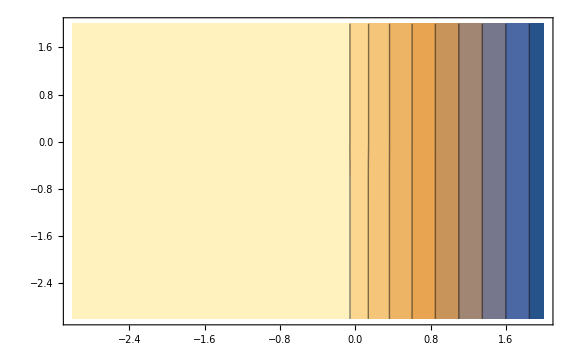

```mathematica
ListContourPlot[xmList]
```

```mathematica
xmint[kappa_,kappas_]=10^Interpolation[xmList][Log10[kappa],Log10[kappas]];
```

N::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating 3-Log[1000]/Log[10].

General::stop: Further output of N::meprec will be suppressed during this calculation.

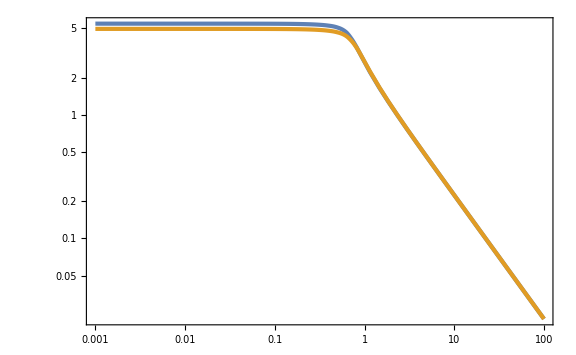

```mathematica
LogLogPlot[{xmint[kappa,10^-3],xmint[kappa,10^2]},{kappa,10^-3,10^2},PlotRange->Full]
```

```mathematica
Cmax[mu_,kappa_,kappas_]=CompactC[xmint[kappa,kappas],mu,kappa,kappas];
```

```mathematica
muthList=Flatten[ParallelTable[{logk,logks,Log10[mu/.Solve[Cmax[mu,10^logk,10^logks]==0.267,mu][[1]]]},{logk,-3,2,10^-1},{logks,-3,2,10^-1}],1];//AbsoluteTiming
```

{91.0746,Null}

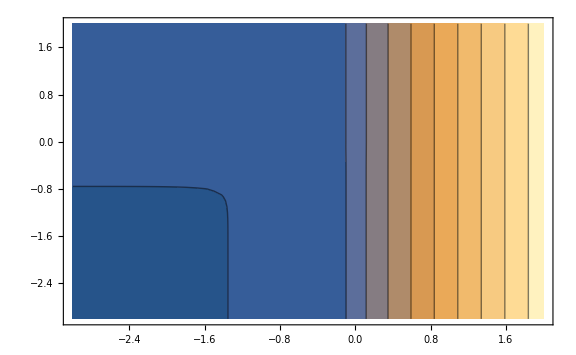

```mathematica
ListContourPlot[muthList]
```

```mathematica
muthint[kappa_,kappas_]=10^Interpolation[muthList][Log10[kappa],Log10[kappas]];
```

```mathematica
muthint[0.01,0.01]
```

0.099744

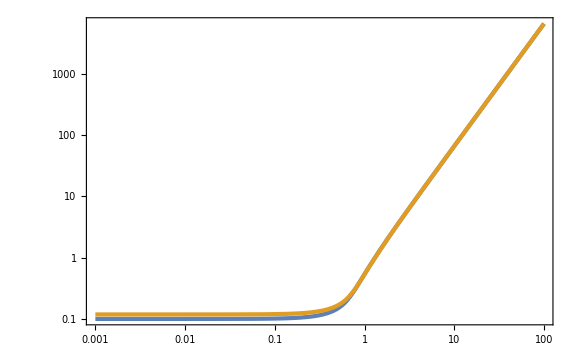

```mathematica
LogLogPlot[{muthint[kappa,10^-3],muthint[kappa,10^2]},{kappa,10^-3,10^2}]
```

```mathematica
gm[kappa_,kappas_]=zetax[xmint[kappa,kappas],mu,kappa,kappas]/mu;
```

N::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating 3-Log[1000]/Log[10].

General::stop: Further output of N::meprec will be suppressed during this calculation.

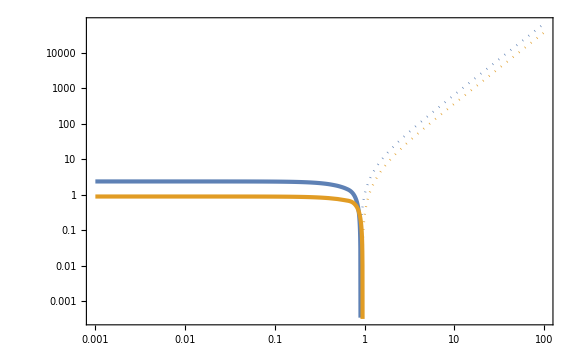

```mathematica
LogLogPlot[{gm[kappa,10^-3],-gm[kappa,10^-3],gm[kappa,10^2],-gm[kappa,10^2]},{kappa,10^-3,10^2},PlotStyle->{AbsoluteThickness[3],{Color[1],Dotted},{Color[2],AbsoluteThickness[3]},{Color[2],Dotted}}]
```

```mathematica
kappacList=ParallelTable[{10^logks,kappa/.FindRoot[gm[kappa,10^logks]==0,{kappa,1}]},{logks,-3,2,10^-1}];//AbsoluteTiming
```

{5.24423,Null}

```mathematica
kappacint[kappas_]=Interpolation[kappacList][kappas];
```

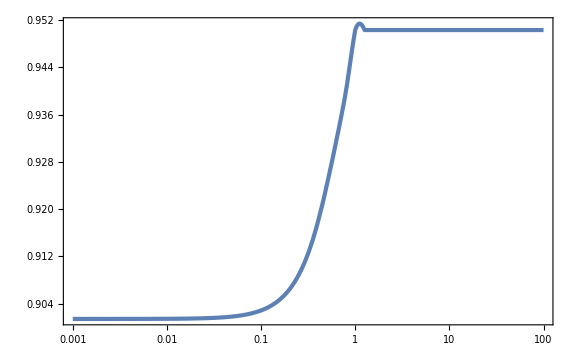

```mathematica
LogLinearPlot[kappacint[kappas],{kappas,10^-3,10^2}]
```

```mathematica
(6.4 10^-14)^-1
```

1.5625×10^13

```mathematica
sigman[4,kW,As]^2/(sigman[2,kW,As] sigman[3,kW,As]^3)
```

(3 √(3/2))/(As kW^3)

```mathematica
sigman[4,kW,As]
```

(√As kW^4)/(2 √2)

```mathematica
sigman[2,kW,As]
```

(√As kW^2)/2

```mathematica
sigman[3,kW]^2/sigman[2,kW,As]^2
```

(2 kW^2)/3

```mathematica
MoMkW[mu_,kappa_]=xmint[kappa]^2 Exp[2mu gm[kappa]];
```

```mathematica
MContour=Table[i,{i,-5,5,1/4}];
```

```mathematica
FigMoMkW=Show[ContourPlot[Log10[MoMkW[10^logm,10^logk]],{logk,-3,0.5},{logm,-2,0.5},Contours->MContour,PlotLegends->BarLegend[Automatic,LegendLabel->Row[{Subscript["log", 10],M[Subscript[OverTilde[μ], 2],κ]/Subscript[M, Subscript[k, "W"]]}]],GridLines->{{Log10[kappac]},None},GridLinesStyle->Directive[Black,Dotted,AbsoluteThickness[2]],FrameLabel->{Row[{Subscript["log", 10]," ",κ}],Subscript["log", 10] Subscript[OverTilde[μ], 2]}],ContourPlot[MoMkW[10^logm,10^logk]==MoMkW[muthint[10^-3],10^-3],{logk,-3,0.5},{logm,-2,0.5},ContourStyle->{Black,AbsoluteThickness[2]}],Plot[Log10[muthint[10^logk]],{logk,-3,2},PlotStyle->{AbsoluteThickness[3],Color[4]}]]
```

-Graphics-

```mathematica
Mc=MoMkW[0.1,kappac]
Mth=MoMkW[muthint[10^-3],10^-3]
```

9.17143

43.762

```mathematica
muthint[10^-3]
```

0.102313

```mathematica
muM[kappa_,MM_]=1/(2gm[kappa])Log[MM/xmint[kappa]^2];
```

```mathematica
FindRoot[muM[kappa,30]==muthint[kappa],{kappa,0.7}]
```

{kappa→0.701322}

```mathematica
FindRoot[muM[kappa,0.001]==muthint[kappa],{kappa,2}]
```

{kappa→1.28126}

```mathematica
kappathList1=Table[{10^logM,kappa/.FindRoot[muM[kappa,10^logM]==muthint[kappa],{kappa,0.908}]},{logM,Log10[Mc]+1/1000,Log10[Mth],1/100}];
```

```mathematica
kappathList2=Table[{10^logM,kappa/.FindRoot[muM[kappa,10^logM]==muthint[kappa],{kappa,0.91}]},{logM,-3,Log10[Mc],1/100}];
```

```mathematica
kappathList=Join[kappathList2,kappathList1];
```

```mathematica
Figkappath=ListLogLinearPlot[kappathList,FrameLabel->{Row[{M,"/",Subscript[M, Subscript[k, "W"]]}],Subscript[κ, th]},GridLines->{{Mc},{kappac}}]
```

-Graphics-

```mathematica
kappathint[MM_]=Interpolation[kappathList][MM];
```

```mathematica
f[z_]=1/2 z(z^2-3)(Erf[1/2 √(5/2)z]+Erf[√(5/2)z])+√(2/(5π))((8/5+31/4 z^2)Exp[-5/8 z^2]+(-8/5+1/2 z^2)Exp[-5/2 z^2]);
PG[z_,m_,s2_]=1/(√(2π s2))Exp[(-(z-m)^2)/(2s2)];
```

```mathematica
npk[mu_,kappa_,As_]=1/(2π)^(3/2)27(√3)/8 f[2 √2 mu kappa^2/(√As)]PG[mu,0,As/8]PG[kappa^2,2/3,As/(24 mu^2)]kappa;
```

```mathematica
nPBH[MM_,As_]:=NIntegrate[2gm[kappa]npk[muM[kappa,MM],kappa,As],{kappa,kappac,kappathint[MM]}]/;MM<Mc
nPBH[MM_,As_]:=NIntegrate[2gm[kappa]npk[muM[kappa,MM],kappa,As],{kappa,kappathint[MM],kappac}]/;Mc<MM<Mth
nPBH[MM_,As_]:=NIntegrate[2gm[kappa]npk[muM[kappa,MM],kappa,As],{kappa,0,kappac}]/;MM>Mth
```

```mathematica
nPBH[10,0.0028]
```

3.90138×10^-116

```mathematica
nPBHList1=ParallelTable[{10^logM,nPBH[10^logM,0.01]},{logM,1,2,1/100}];//AbsoluteTiming
nPBHList2=ParallelTable[{10^logM,nPBH[10^logM,0.0028]},{logM,1,2,1/100}];//AbsoluteTiming
```

InterpolatingFunction::dmval: 
                     16/25
   Input value {10 10     } lies outside the range of data in the
     interpolating function. Extrapolation will be used.

{73.3518,Null}

InterpolatingFunction::dmval: 
                     16/25
   Input value {10 10     } lies outside the range of data in the
     interpolating function. Extrapolation will be used.

{110.149,Null}

```mathematica
Export["nPBH1e-2.dat",nPBHList1];
Export["nPBH28e-4.dat",nPBHList2];
```

```mathematica
gineV=(1.783 10^-33)^-1;
MpcinvineV=(10^6 3.086 10^16)^-1 1.973 10^-7;
KineV=(1.16 10^4)^-1;
MplineV=2.435 10^(18+9);
kminvsinvMpcineV=(10^3 6.582 10^-16)/(3.086 10^16 10^6);
```

```mathematica
n2f=((10^20 gineV (1.56 10^13 MpcinvineV)^3)/(0.12 3 MplineV^2(100kminvsinvMpcineV)^2))^-1
```

1.74505×10^-16

```mathematica
LognPBHList1=Map[Log10,nPBHList1,{2}]//Simplify;
LognPBHList2=Map[Log10,nPBHList2,{2}]//Simplify;
```

```mathematica
nPBHint1[MM_]=10^(Interpolation[LognPBHList1][Log10[MM]]);
nPBHint2[MM_]=10^(Interpolation[LognPBHList2][Log10[MM]]);
```

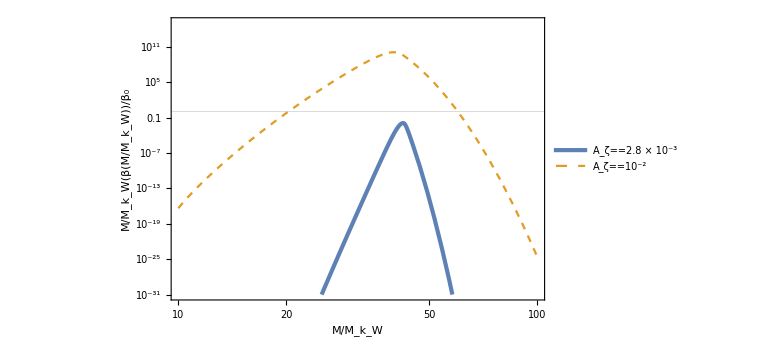

```mathematica
FigBeta=LogLogPlot[{MM nPBHint2[MM]/n2f,MM nPBHint1[MM]/n2f},{MM,10,100},PlotRange->{10^-31,10^15},GridLines->{None,{1}},FrameLabel->{Row[{M,"/",Subscript[M, Subscript[k, "W"]]}],Row[{M/Subscript[M, Subscript[k, "W"]],β[Row[{M,"/",Subscript[M, Subscript[k, "W"]]}]]/Subscript[β, 0]}]},PlotStyle->{AbsoluteThickness[3],Dashed},PlotLegends->Placed[LineLegend[{Row[{Subscript[A, ζ]==2.8," × ",Superscript[10,-3]}],Subscript[A, ζ]==Superscript[10,-2]},LabelStyle->Directive[Larger,Black,FontFamily->"Palatino"]],{0.25,0.2}]]
```

```mathematica
MaxfPBH=FindMaximum[MM nPBHint2[MM]/n2f,{MM,40}][[1]]
MaxMM=MM/.FindMaximum[MM nPBHint2[MM]/n2f,{MM,40}][[2]]
```

FindMaximum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient increase in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

0.0115842

FindMaximum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient increase in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

42.2278

InterpolatingFunction::dmval: Input value {0.0000612857} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::munfl: 1/10^2797.23 is too small to represent as a normalized machine number; precision may be lost.

InterpolatingFunction::dmval: Input value {0.0612858} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::munfl: 1/10^2376.04 is too small to represent as a normalized machine number; precision may be lost.

InterpolatingFunction::dmval: Input value {0.12251} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

General::munfl: 1/10^2002.41 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

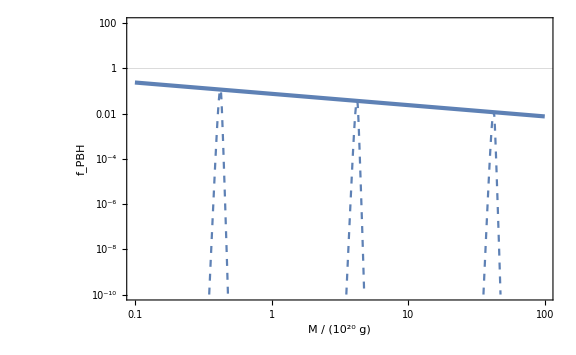

```mathematica
FigfPBH=LogLogPlot[{0.01^-0.5 MM/0.01 nPBHint2[MM/0.01]/n2f,0.1^-0.5 MM/0.1 nPBHint2[MM/0.1]/n2f,MM nPBHint2[MM]/n2f,MaxfPBH (MM/MaxMM)^(-1/2)},{MM,0.1,100},PlotRange->{10^-10,100},GridLines->{None,{1}},PlotStyle->{Dashed,{Color[1],Dashed},{Color[1],Dashed},{Color[1],AbsoluteThickness[3]}},FrameLabel->{Row[{M," / (",Superscript[10,20]," g)"}],Subscript[f, PBH]}]
```

## non-Gaussian

### monochromatic

```mathematica
sigman[n_,ks_,As_]=ks^n √As
psin[n_,r_,ks_]=ks^(2n-4)Sin[ks r]/(ks r)
```

√As ks^n

(ks^(-5+2 n) Sin[ks r])/r

```mathematica
gamma1=sigman[1,ks,As]^2/(sigman[0,ks,As]sigman[2,ks,As])
gamma2=sigman[2,ks,As]^2/(sigman[0,ks,As]sigman[4,ks,As])
gamma3=sigman[3,ks,As]^2/(sigman[2,ks,As]sigman[4,ks,As])
Rb[ks_]=√3 sigman[3,ks,As]/sigman[4,ks,As]
```

1

1

1

(√3)/ks

```mathematica
zetaGx[x_,mu_]=mu Sin[x]/x//Simplify
```

(mu Sin[x])/x

```mathematica
zetabar[x_,mu_,fNL_]=zetaGx[x,mu]+3/5 fNL zetaGx[x,mu]^2//Simplify
```

(mu Sin[x] (5 x+3 fNL mu Sin[x]))/(5 x^2)

```mathematica
CompactC[x_,mu_,fNL_]=1/3(1-(1+x D[zetabar[x,mu,fNL], x])^2)//Simplify
```

1/3 (1-((5 x^2-5 mu x Sin[x]-6 fNL mu^2 Sin[x]^2+mu x Cos[x] (5 x+6 fNL mu Sin[x]))^2)/(25 x^4))

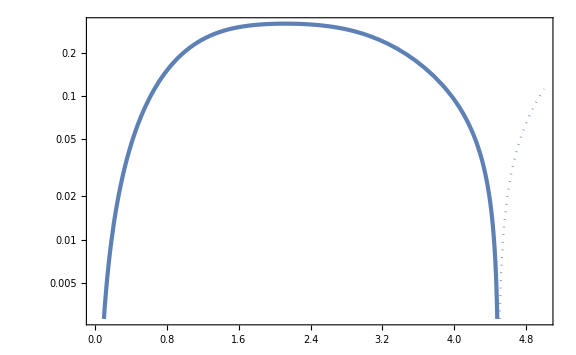

```mathematica
LogPlot[{CompactC[x,0.5,3],-CompactC[x,0.5,3]},{x,0,5},PlotStyle->{AbsoluteThickness[3],{Color[1],Dotted}}]
```

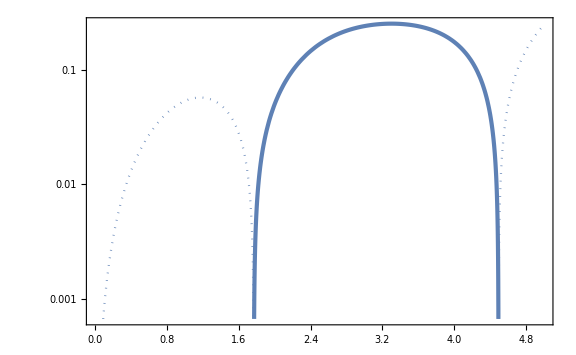

```mathematica
LogPlot[{CompactC[x,0.5,-3],-CompactC[x,0.5,-3]},{x,0,5},PlotStyle->{AbsoluteThickness[3],{Color[1],Dotted}}]
```

```mathematica
rmcond[x_,mu_,fNL_]=(5 x^3)/mu(D[zetabar[x,mu,fNL], x]+x D[D[zetabar[x,mu,fNL], x], x])//Simplify
```

6 fNL mu-5 x^2 Cos[x]+6 fNL mu (-1+x^2) Cos[2 x]+5 x Sin[x]-5 x^3 Sin[x]-9 fNL mu x Sin[2 x]

```mathematica
rmcond2[x_,mu_,fNL_]=5 x^2(1+x D[zetabar[x,mu,fNL], x])//Simplify
```

5 x^2-5 mu x Sin[x]-6 fNL mu^2 Sin[x]^2+mu x Cos[x] (5 x+6 fNL mu Sin[x])

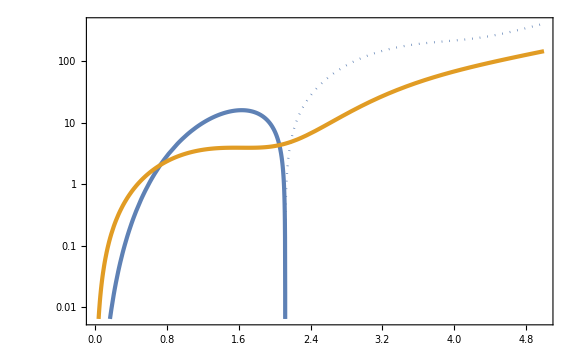

```mathematica
LogPlot[{-rmcond[x,0.5,3],rmcond[x,0.5,3],rmcond2[x,0.5,3],-rmcond2[x,0.5,3]},{x,0,5},PlotStyle->{AbsoluteThickness[3],{Color[1],Dotted},{AbsoluteThickness[3],Color[2]},{Color[2],Dotted}}]
```

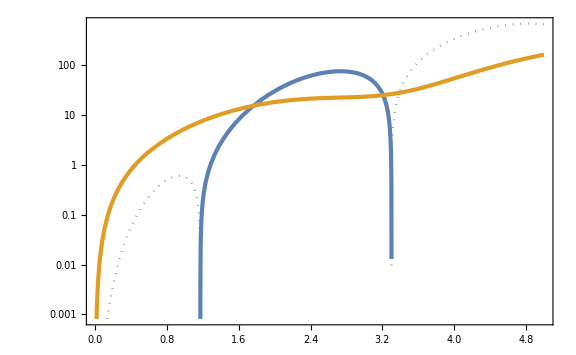

```mathematica
LogPlot[{-rmcond[x,0.5,-3],rmcond[x,0.5,-3],rmcond2[x,0.5,-3],-rmcond2[x,0.5,-3]},{x,0,5},PlotStyle->{AbsoluteThickness[3],{Color[1],Dotted},{AbsoluteThickness[3],Color[2]},{Color[2],Dotted}}]
```

```mathematica
FindRoot[rmcond[x,0.5,3]==0,{x,3}]
```

{x→2.1157}

```mathematica
xmList=Table[{mufNL,x/.FindRoot[rmcond[x,1,mufNL]==0,{x,3}]},{mufNL,-5/3,5/3,1/10}];
```

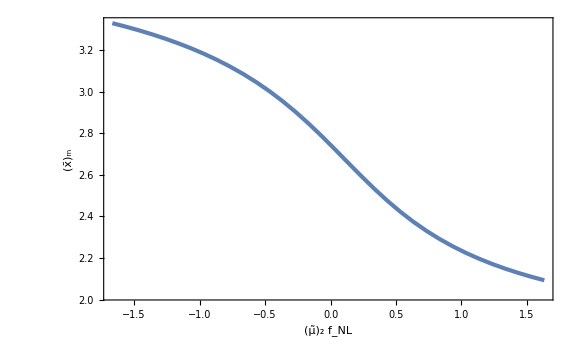

```mathematica
ListPlot[xmList,FrameLabel->{Subscript[OverTilde[μ], 2] Subscript[f, NL],Subscript[OverBar[x], "m"]}]
```

```mathematica
xmint[mufNL_]=Interpolation[xmList][mufNL];
```

```mathematica
Solve[CompactC[xmint[-5/3],mu,1/mu(-5/3)]==0.267,mu]
```

{{mu→0.537651},{mu→1.40366}}

```mathematica
muthList=Table[musol=mu/.Solve[CompactC[xmint[mufNL],mu,mufNL/mu]==0.267,mu][[1]];
{mufNL/musol,musol},{mufNL,-5/3,5/3,1/10}];
```

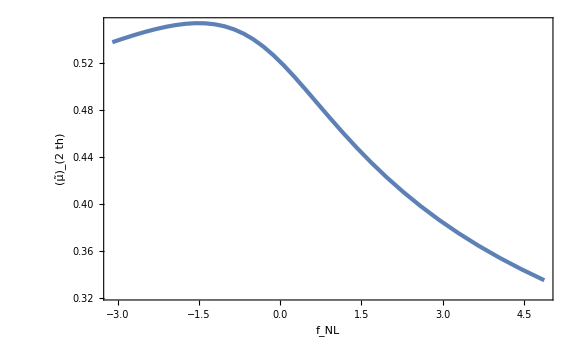

```mathematica
ListPlot[muthList,FrameLabel->{Subscript[f, NL],Subscript[OverTilde[μ], 2th]}]
```

```mathematica
fNLmin=First[muthList][[1]]
fNLmax=Last[muthList][[1]]
```

-3.0999

4.87679

```mathematica
muthint[fNL_]=Interpolation[muthList][fNL];
```

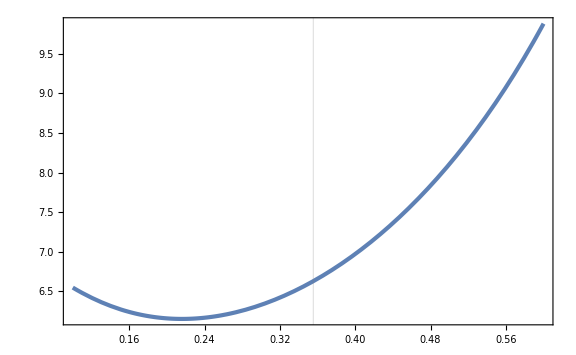

```mathematica
Plot[xmint[mu 4]^2 Exp[2zetabar[xmint[mu 4],mu,4]],{mu,0.1,0.6},GridLines->{{muthint[4]},None}]
```

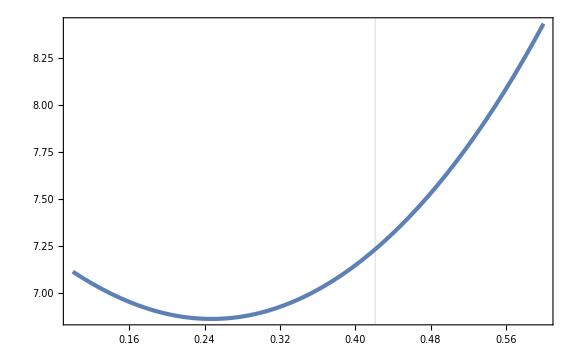

```mathematica
Plot[xmint[mu 2]^2 Exp[2zetabar[xmint[mu 2],mu,2]],{mu,0.1,0.6},GridLines->{{muthint[2]},None}]
```

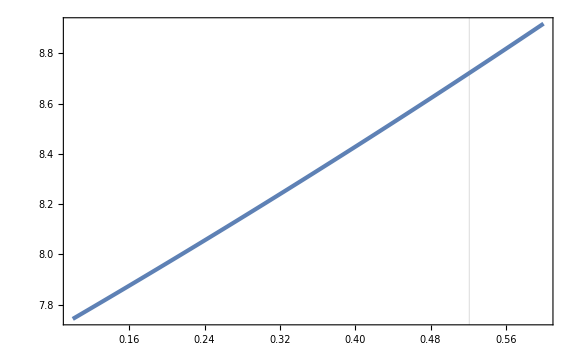

```mathematica
Plot[xmint[mu 0]^2 Exp[2zetabar[xmint[mu 0],mu,0]],{mu,0.1,0.6},GridLines->{{muthint[0]},None}]
```

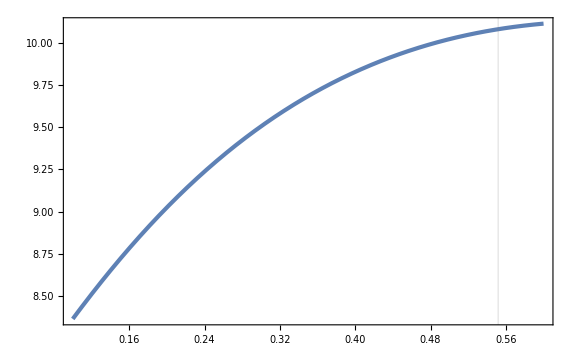

```mathematica
Plot[xmint[mu (-2)]^2 Exp[2zetabar[xmint[mu (-2)],mu,-2]],{mu,0.1,0.6},GridLines->{{muthint[-2]},None}]
```

```mathematica
dLogMdmu[mu_,fNL_]=D[Log[xmint[mu fNL]^2 Exp[2zetabar[xmint[mu fNL],mu,fNL]]], mu];
```

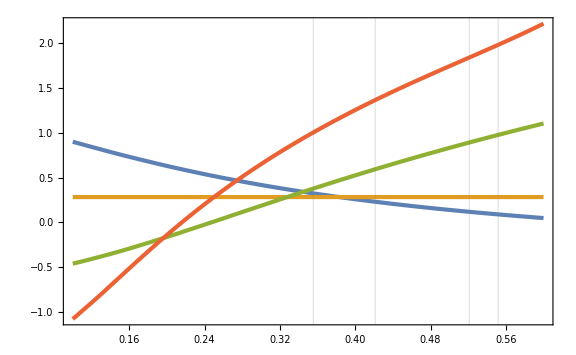

```mathematica
Plot[{dLogMdmu[mu,-2],dLogMdmu[mu,0],dLogMdmu[mu,2],dLogMdmu[mu,4]},{mu,0.1,0.6},GridLines->{{muthint[-2],muthint[0],muthint[2],muthint[4]},None}]
```

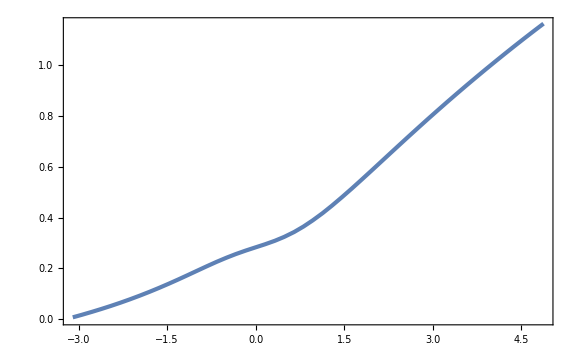

```mathematica
Plot[dLogMdmu[muthint[fNL],fNL],{fNL,fNLmin,fNLmax}(*,FrameLabel->{Subscript[f, NL],Subscript[Abs[Row[{"d log ",M}]/("d"Subscript[OverTilde[μ], 2])], Subscript[OverTilde[μ], 2]==Subscript[OverTilde[μ], 2th]]}*)]
```

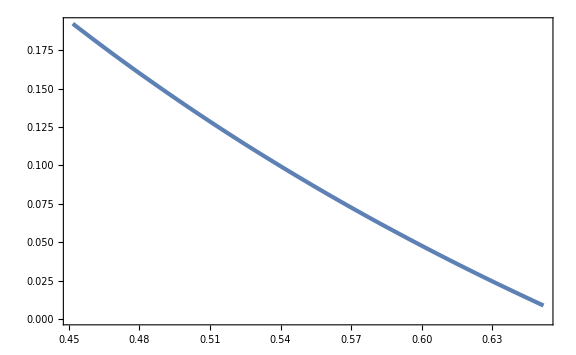

```mathematica
Plot[dLogMdmu[mu,-2],{mu,muthint[-2]-0.1,muthint[-2]+0.1}]
```

```mathematica
f[z_]=1/2 z(z^2-3)(Erf[1/2 √(5/2)z]+Erf[√(5/2)z])+√(2/(5π))((8/5+31/4 z^2)Exp[-5/8 z^2]+(-8/5+1/2 z^2)Exp[-5/2 z^2]);
```

```mathematica
gineV=(1.783 10^-33)^-1;
MpcinvineV=(10^6 3.086 10^16)^-1 1.973 10^-7;
KineV=(1.16 10^4)^-1;
MplineV=2.435 10^(18+9);
kminvsinvMpcineV=(10^3 6.582 10^-16)/(3.086 10^16 10^6);
```

```mathematica
((10^20 gineV(3/(2π))^(3/2)(1.56 10^13 MpcinvineV)^3)/(0.12 3 MplineV^2(100 kminvsinvMpcineV)^2))^-1
```

5.28928×10^-16

```mathematica
PG[x_,sg2_]=1/(√(2π sg2))Exp[-x^2/(2sg2)];
```

```mathematica
MoMks[mu_,fNL_]=xmint[mu fNL]^2 Exp[2zetabar[xmint[mu fNL],mu,fNL]];
```

```mathematica
fPBH[Mks_,ks_,As_,mu_,fNL_]=Mks/10^20 MoMks[mu,fNL](ks/(1.56 10^13))^3(f[mu/(√As)]PG[mu,As])/(5.3 10^-16)dLogMdmu[mu,fNL]^-1 UnitStep[mu-muthint[fNL]];
```

```mathematica
muthint[-2]
```

0.551735

```mathematica
fPBH[10^20,1.56 10^13,2.8 10^-3,0.6,0]
```

7.70761×10^-8

```mathematica
fPBHListfNLm2=Table[{MoMks[mu,-2],fPBH[10^20,1.56 10^13,2.8 10^-3,mu,-2]},{mu,muthint[-2]-0.1,5/3 1/2,0.01}];
fPBHListfNL0=Table[{MoMks[mu,0],fPBH[10^20,1.56 10^13,2.8 10^-3,mu,0]},{mu,muthint[0]-0.1,1,0.01}];
fPBHListfNLp2=Table[{MoMks[mu,2],fPBH[10^20,1.56 10^13,2.8 10^-3,mu,2]},{mu,muthint[2]-0.1,5/3 1/2,0.01}];
fPBHListfNLp4=Table[{MoMks[mu,4],fPBH[10^20,1.56 10^13,2.8 10^-3,mu,4]},{mu,muthint[4]-0.1,5/3 1/4,0.01}];
fPBHListfNLp4Ex=Table[{MoMks[mu,4],fPBH[10^20,1.56 10^13,2.8 10^-3,mu,4]},{mu,5/3 1/4,5/3 1/4+0.05,0.01}];
```

General::munfl: Exp[-708.863] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-724.864] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-741.043] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {1.64233} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {1.66141} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {1.66667} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

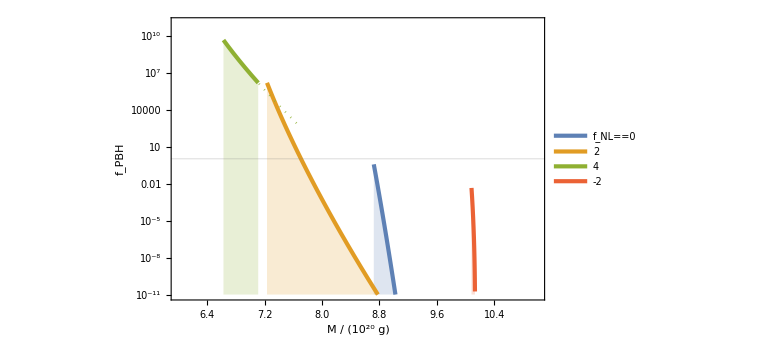

```mathematica
Show[ListLogPlot[{fPBHListfNL0,fPBHListfNLp2,fPBHListfNLp4,fPBHListfNLm2},PlotRange->{{6,11},{10^-11,10^11}},Filling->Bottom,GridLines->{None,{1}},FrameLabel->{Row[{M," / (10^20 g)"}],Subscript[f, PBH]},PlotLegends->Placed[LineLegend[{Subscript[f, NL]==0,2,4,-2},LabelStyle->Directive[Black,Larger,FontFamily->"Palatino"]],{0.8,0.75}]],ListLogPlot[fPBHListfNLp4Ex,PlotStyle->{Color[3],Dotted}]]
```

### scale-invariant

```mathematica
Quit[]
```

```mathematica
$Assumptions={sg>0,ks>0,n>0,As>0,kW>0,kL>0};
```

```mathematica
sigman[n_,kW_,As_]=√(As Integrate[Exp[2n logk],{logk ,-∞,Log[kW]}])//Simplify
```

(kW^n √(As/n))/(√2)

```mathematica
sigma0[kW_,As_,kL_]=√(As Integrate[1,{logk,Log[kL],Log[kW]}])//Simplify
```

√(As Log[kW/kL])

```mathematica
psin[n_,r_,kW_]=1/sigman[2,kW,As]^2 As Integrate[k^(2n)Sin[k r]/(k r)1/k,{k,0,kW}]
```

(2 kW^(-4+2 n) HypergeometricPFQ[{n},{3/2,1+n},-1/4 kW^2 r^2])/n

```mathematica
psin[1,r,kW]//Simplify
psin[2,r,kW]//Simplify
```

(4-4 Cos[kW r])/(kW^4 r^2)

(-8+(8-4 kW^2 r^2) Cos[kW r]+8 kW r Sin[kW r])/(kW^4 r^4)

```mathematica
gamma1[kW_,kL_]=sigman[1,kW,As]^2/(sigma0[kW,As,kL]sigman[2,kW,As])//Simplify
gamma2[kW_,kL_]=sigman[2,kW,As]^2/(sigma0[kW,As,kL]sigman[4,kW,As])//Simplify
gamma3=sigman[3,kW,As]^2/(sigman[2,kW,As]sigman[4,kW,As])
Rb[kW_]=√3 sigman[3,kW,As]/sigman[4,kW,As]
```

1/(√Log[kW/kL])

1/(√2 √Log[kW/kL])

(2 √2)/3

2/kW

```mathematica
DD[kW_,kL_]=1-gamma1[kW,kL]^2-gamma2[kW,kL]^2-gamma3^2+2gamma1[kW,kL] gamma2[kW,kL] gamma3
```

1/9-1/(6 Log[kW/kL])

```mathematica
calM={{1,γ1,γ2},{γ1,1,γ3},{γ2,γ3,1}};calM//MatrixForm
```

(1 | γ1 | γ2
γ1 | 1 | γ3
γ2 | γ3 | 1)

```mathematica
Simplify[Det[calM]Inverse[calM]]//MatrixForm
```

(1-γ3^2 | -γ1+γ2 γ3 | -γ2+γ1 γ3
-γ1+γ2 γ3 | 1-γ2^2 | γ1 γ2-γ3
-γ2+γ1 γ3 | γ1 γ2-γ3 | 1-γ1^2)

```mathematica
zetaGbar[r_,kW_,mu2_,kb_]=mu2/(1-gamma3^2)(psin[1,r,kW]-1/3 Rb[kW]^2 psin[2,r,kW])-mu2 kb^2 sigman[2,kW,As]/(sigman[4,kW,As]gamma3(1-gamma3^2))(gamma3^2 psin[1,r,kW]-1/3 Rb[kW]^2 psin[2,r,kW])//Simplify
```

(12 mu2 (-12 kb^2+8 kW^2-4 kb^2 kW^2 r^2+3 kW^4 r^2+(kW^2 (-8+kW^2 r^2)-2 kb^2 (-6+kW^2 r^2)) Cos[kW r]+4 kW (3 kb^2-2 kW^2) r Sin[kW r]))/(kW^8 r^4)

```mathematica
zetaGx[x_,mu_,kappa_]=zetaGbar[x/kW,kW,mu kW^2,kappa kW]//Simplify
```

-(12 mu (-8+12 kappa^2-3 x^2+4 kappa^2 x^2+(8-x^2+2 kappa^2 (-6+x^2)) Cos[x]-4 (-2+3 kappa^2) x Sin[x]))/x^4

```mathematica
zetabar[x_,mu_,kappa_,zetainf_,fNL_]=(1+6/5 fNL zetainf)zetaGx[x,mu,kappa]+3/5 fNL zetaGx[x,mu,kappa]^2//Simplify
```

1/(5 x^8)12 mu (-8+12 kappa^2-3 x^2+4 kappa^2 x^2+(8-x^2+2 kappa^2 (-6+x^2)) Cos[x]-4 (-2+3 kappa^2) x Sin[x]) (-x^4 (5+6 fNL zetainf)+36 fNL mu (-8+12 kappa^2-3 x^2+4 kappa^2 x^2+(8-x^2+2 kappa^2 (-6+x^2)) Cos[x]-4 (-2+3 kappa^2) x Sin[x]))

```mathematica
muzetainfsol=Solve[(1+6/5 fNL zetainf)mu==mueff&&fNL/(1+6/5 fNL zetainf)mu==fNLeff,{mu,zetainf}][[2]]
```

{mu→(√fNLeff √mueff)/(√fNL),zetainf→(5 (-√fNLeff+√fNL √mueff))/(6 fNL √fNLeff)}

```mathematica
zetaeff[x_,mueff_,kappa_,fNLeff_]=zetabar[x,mu,kappa,zetainf,fNL]/.muzetainfsol//Simplify
```

1/(5 x^8)12 mueff (-8+12 kappa^2-3 x^2+4 kappa^2 x^2+(8-x^2+2 kappa^2 (-6+x^2)) Cos[x]-4 (-2+3 kappa^2) x Sin[x]) (-288 fNLeff+432 fNLeff kappa^2-108 fNLeff x^2+144 fNLeff kappa^2 x^2-5 x^4+36 fNLeff (8-x^2+2 kappa^2 (-6+x^2)) Cos[x]-144 fNLeff (-2+3 kappa^2) x Sin[x])

```mathematica
Collect[zetaeff[x,mueff,kappa,fNLeff],fNLeff,Simplify]
```

-(12 mueff (-8+12 kappa^2-3 x^2+4 kappa^2 x^2+(8-x^2+2 kappa^2 (-6+x^2)) Cos[x]-4 (-2+3 kappa^2) x Sin[x]))/x^4+(432 fNLeff mueff (-8+12 kappa^2-3 x^2+4 kappa^2 x^2+(8-x^2+2 kappa^2 (-6+x^2)) Cos[x]-4 (-2+3 kappa^2) x Sin[x])^2)/(5 x^8)

```mathematica
12^2 3/5
```

432/5

```mathematica
gx[x_,kappa_]=zetaGx[x,mu,kappa]/mu//Simplify
```

-(12 (-8+12 kappa^2-3 x^2+4 kappa^2 x^2+(8-x^2+2 kappa^2 (-6+x^2)) Cos[x]-4 (-2+3 kappa^2) x Sin[x]))/x^4

```mathematica
Manipulate[LogLinearPlot[gx[x,10^logk],{x,10^-2,10^2},PlotRange->Full],{logk,-0.1,0.1}]
```

```mathematica
gxMaxList=ParallelTable[{10^logk,Max[FindMaxValue[{gx[x,10^logk],10^-2<x<6},{x,1},WorkingPrecision->30],FindMaxValue[{-gx[x,10^logk],10^-2<x<6},{x,1},WorkingPrecision->30]]//Quiet},{logk,-3,2,10^-2}];//AbsoluteTiming
```

{322.191,Null}

```mathematica
Export["gxMax_flat_NG.dat",gxMaxList];
```

```mathematica
gxMaxList=Import["gxMax_flat_NG.dat"]//ToExpression;
```

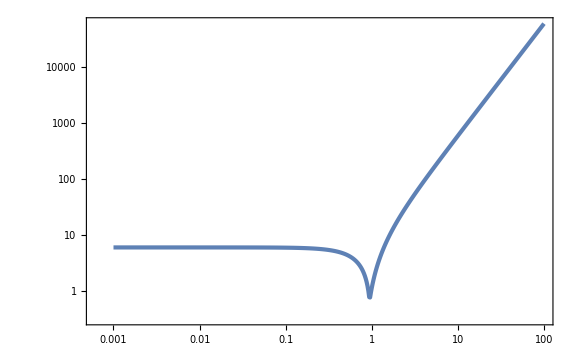

```mathematica
ListLogLogPlot[gxMaxList]
```

```mathematica
gxMaxInt[kappa_]=Interpolation[gxMaxList][kappa];
```

```mathematica
gbar[x_,kappa_,fNLeff_]=zetaeff[x,mueff,kappa,fNLeff]/mueff//Simplify
```

1/(5 x^8)12 (-8+12 kappa^2-3 x^2+4 kappa^2 x^2+(8-x^2+2 kappa^2 (-6+x^2)) Cos[x]-4 (-2+3 kappa^2) x Sin[x]) (-288 fNLeff+432 fNLeff kappa^2-108 fNLeff x^2+144 fNLeff kappa^2 x^2-5 x^4+36 fNLeff (8-x^2+2 kappa^2 (-6+x^2)) Cos[x]-144 fNLeff (-2+3 kappa^2) x Sin[x])

```mathematica
Collect[gbar[x,kappa,fNLeff],fNLeff,Simplify]
```

-(12 (-8+12 kappa^2-3 x^2+4 kappa^2 x^2+(8-x^2+2 kappa^2 (-6+x^2)) Cos[x]-4 (-2+3 kappa^2) x Sin[x]))/x^4+(432 fNLeff (-8+12 kappa^2-3 x^2+4 kappa^2 x^2+(8-x^2+2 kappa^2 (-6+x^2)) Cos[x]-4 (-2+3 kappa^2) x Sin[x])^2)/(5 x^8)

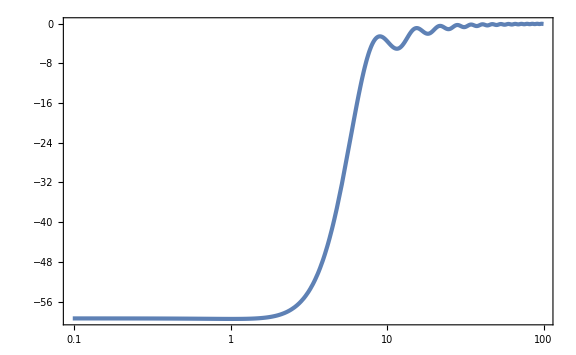

```mathematica
LogLinearPlot[gbar[x,10^(1/2),-1/6 gxMaxInt[10^(1/2)]^-1],{x,0,10^2}]
```

```mathematica
CompactC[x_,mueff_,kappa_,fNLeff_]=1/3(1-(1+x D[zetaeff[x,mueff,kappa,fNLeff], x])^2)//Simplify
```

1/3 (1-1/(25 x^16)(5 x^8-48 mueff x^2 (54 fNLeff-72 fNLeff kappa^2+5 x^2+18 fNLeff (-3+4 kappa^2) Cos[x]+9 fNLeff (-1+2 kappa^2) x Sin[x]) (-8+12 kappa^2-3 x^2+4 kappa^2 x^2+(8-x^2+2 kappa^2 (-6+x^2)) Cos[x]-4 (-2+3 kappa^2) x Sin[x])+12 mueff x^2 (6-8 kappa^2+(-6+8 kappa^2) Cos[x]+(-1+2 kappa^2) x Sin[x]) (288 fNLeff-432 fNLeff kappa^2+108 fNLeff x^2-144 fNLeff kappa^2 x^2+5 x^4-36 fNLeff (8-x^2+2 kappa^2 (-6+x^2)) Cos[x]+144 fNLeff (-2+3 kappa^2) x Sin[x])-96 mueff (8-12 kappa^2+3 x^2-4 kappa^2 x^2+(-8+x^2-2 kappa^2 (-6+x^2)) Cos[x]+4 (-2+3 kappa^2) x Sin[x]) (288 fNLeff-432 fNLeff kappa^2+108 fNLeff x^2-144 fNLeff kappa^2 x^2+5 x^4-36 fNLeff (8-x^2+2 kappa^2 (-6+x^2)) Cos[x]+144 fNLeff (-2+3 kappa^2) x Sin[x]))^2)

```mathematica
Collect[CompactC[x,mueff,kappa,fNLeff],mueff,Simplify]
```

1/(5 x^8)16 mueff (x Cos[x/2]-2 Sin[x/2]) (4 (-2+3 kappa^2) x Cos[x/2]+(16-x^2+2 kappa^2 (-12+x^2)) Sin[x/2]) (-576 fNLeff+864 fNLeff kappa^2-216 fNLeff x^2+288 fNLeff kappa^2 x^2-5 x^4+72 fNLeff (8-x^2+2 kappa^2 (-6+x^2)) Cos[x]-288 fNLeff (-2+3 kappa^2) x Sin[x])-1/(25 x^16)192 mueff^2 (x Cos[x/2]-2 Sin[x/2])^2 (4 (-2+3 kappa^2) x Cos[x/2]+(16-x^2+2 kappa^2 (-12+x^2)) Sin[x/2])^2 (576 fNLeff-864 fNLeff kappa^2+216 fNLeff x^2-288 fNLeff kappa^2 x^2+5 x^4-72 fNLeff (8-x^2+2 kappa^2 (-6+x^2)) Cos[x]+288 fNLeff (-2+3 kappa^2) x Sin[x])^2

```mathematica
Manipulate[LogLogPlot[CompactC[x,10^-1,10^logk,-1/6 gxMaxInt[10^logk]^-1],{x,Min[10^-2,10^(-logk-1)],Min[10^2,10^(-logk+2)]},WorkingPrecision->30]//Quiet,{logk,-3,2,1/2}]
```

```mathematica
xmcond[x_,kappa_,fNLeff_]=1/x^2(D[gbar[x,kappa,fNLeff], x]+x D[D[gbar[x,kappa,fNLeff], x], x])//Simplify
```

-1/(5 x^11)12 (-221184 fNLeff+663552 fNLeff kappa^2-497664 fNLeff kappa^4-93312 fNLeff x^2+264384 fNLeff kappa^2 x^2-186624 fNLeff kappa^4 x^2-640 x^4-5472 fNLeff x^4+960 kappa^2 x^4+14976 fNLeff kappa^2 x^4-10368 fNLeff kappa^4 x^4-60 x^6+80 kappa^2 x^6+(5 x^4 (128-52 x^2+x^4-2 kappa^2 (96-40 x^2+x^4))+72 fNLeff (4096-320 x^2-280 x^4+3 x^6+8 kappa^4 (1152-144 x^2-73 x^4+x^6)-2 kappa^2 (6144-624 x^2-406 x^4+5 x^6))) Cos[x]+72 fNLeff (-1024+1616 x^2-156 x^4+x^6-4 kappa^2 (-768+1230 x^2-129 x^4+x^6)+4 kappa^4 (-576+936 x^2-106 x^4+x^6)) Cos[2 x]+294912 fNLeff x Sin[x]-884736 fNLeff kappa^2 x Sin[x]+663552 fNLeff kappa^4 x Sin[x]+51264 fNLeff x^3 Sin[x]-140256 fNLeff kappa^2 x^3 Sin[x]+95040 fNLeff kappa^4 x^3 Sin[x]+640 x^5 Sin[x]-3240 fNLeff x^5 Sin[x]-960 kappa^2 x^5 Sin[x]+9936 fNLeff kappa^2 x^5 Sin[x]-7488 fNLeff kappa^4 x^5 Sin[x]-55 x^7 Sin[x]+90 kappa^2 x^7 Sin[x]-147456 fNLeff x Sin[2 x]+442368 fNLeff kappa^2 x Sin[2 x]-331776 fNLeff kappa^4 x Sin[2 x]+48096 fNLeff x^3 Sin[2 x]-151056 fNLeff kappa^2 x^3 Sin[2 x]+118368 fNLeff kappa^4 x^3 Sin[2 x]-1404 fNLeff x^5 Sin[2 x]+5040 fNLeff kappa^2 x^5 Sin[2 x]-4464 fNLeff kappa^4 x^5 Sin[2 x])

```mathematica
Manipulate[LogLogPlot[{-xmcond[x,10^logk,(*-5/6 gxMaxInt[10^logk]^-1*)0],xmcond[x,10^logk,(*-5/6 gxMaxInt[10^logk]^-1*)0]},{x,Min[5 10^-2,10^(-logk-1)],Min[50,10^(-logk+1)]},PlotStyle->{AbsoluteThickness[3],{Color[1],Dotted}},WorkingPrecision->30,PlotRange->Full,GridLines->{{Min[2/10^logk,6]},None}],{logk,-3,2,1/2}]
```

```mathematica
FindRoot[xmcond[x,kappa,-5/6 gxMaxInt[kappa]^-1]==0,{x,Min[3/kappa,6]},WorkingPrecision->30]/.{kappa->10^1}
```

FindRoot::srect: Value Min[6.,3./kappa] in search specification {x,Min[3/kappa,6]} is not a number or array of numbers.

FindRoot::precw: The precision of the argument function (-(12 (6.8889406527297112022493010365×10^6+2.5811855025380933437119077814×10^6 x^2+«10»+8945 x^7 Sin[x]+«3»))/(5 x^11)==0) is less than WorkingPrecision (30.).

{x→0.223967042965739153170238325521}

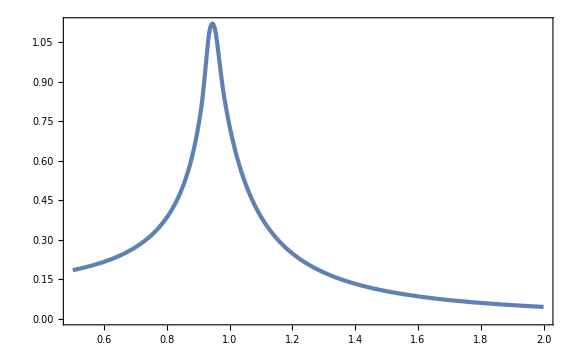

```mathematica
Plot[5/6 gxMaxInt[kappa]^-1,{kappa,5/10,2}]
```

```mathematica
xm[kappa_,fNLeff_]:=(x/.FindRoot[xmcond[x,kappa,fNLeff]==0,{x,Min[2/kappa,6]},WorkingPrecision->30])/;Abs[3/5 fNLeff gxMaxInt[kappa]]≤1/2
xm[kappa_,fNLeff_]:=None/;Abs[3/5 fNLeff gxMaxInt[kappa]]>1/2
```

```mathematica
xmList=Flatten[Table[{logk,fNLeff,xm[10^logk,fNLeff]},{logk,-3,2,10^-2},{fNLeff,-2,2,10^-2}],1];//AbsoluteTiming
```

{111.16,Null}

```mathematica
Export["xm_flat_NG.dat",xmList];
```

```mathematica
xmList=Import["xm_flat_NG.dat"]//ToExpression;
```

```mathematica
xmint[kappa_,fNLeff_]=Interpolation[xmList][Log10[kappa],fNLeff];
```

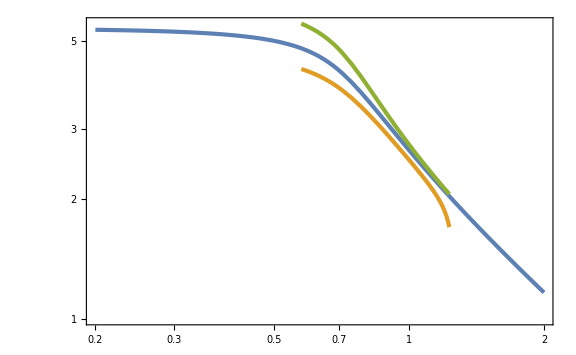

```mathematica
LogLogPlot[{xmint[kappa,0],xmint[kappa,0.2],xmint[kappa,-0.2]},{kappa,2/10,2}]
```

```mathematica
musol[x_,kappa_,fNLeff_,Cth_]=mueff/.Solve[CompactC[x,mueff,kappa,fNLeff]==Cth,mueff][[2]];
```

```mathematica
Clear[muth]
```

```mathematica
muth[kappa_,fNLeff_]:=musol[xmint[kappa,fNLeff],kappa,fNLeff,0.267]/;Abs[3/5 fNLeff gxMaxInt[kappa]]≤1/2
muth[kappa_,fNLeff_]:=None/;Abs[3/5 fNLeff gxMaxInt[kappa]]>1/2
```

```mathematica
muthList=Flatten[Table[{logk,fNLeff,muth[10^logk,fNLeff]//Quiet},{logk,-3,2,10^-2},{fNLeff,-2,2,10^-2}],1];//AbsoluteTiming
```

{420.455,Null}

```mathematica
Export["muth_flat_NG.dat",muthList];
```

```mathematica
muthList=Import["muth_flat_NG.dat"]//ToExpression;
```

```mathematica
muthint[kappa_,fNLeff_]=Interpolation[muthList][Log10[kappa],fNLeff];
```

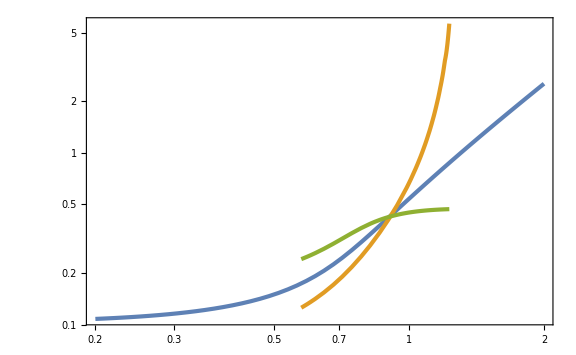

```mathematica
LogLogPlot[{muthint[kappa,0],muthint[kappa,0.2],muthint[kappa,-0.2]},{kappa,0.2,2}]
```

```mathematica
gm[kappa_,fNLeff_]:=gbar[xmint[kappa,fNLeff],kappa,fNLeff]/;Abs[3/5 fNLeff gxMaxInt[kappa]]≤1/2;
gm[kappa_,fNLeff_]:=None/;Abs[3/5 fNLeff gxMaxInt[kappa]]>1/2;
```

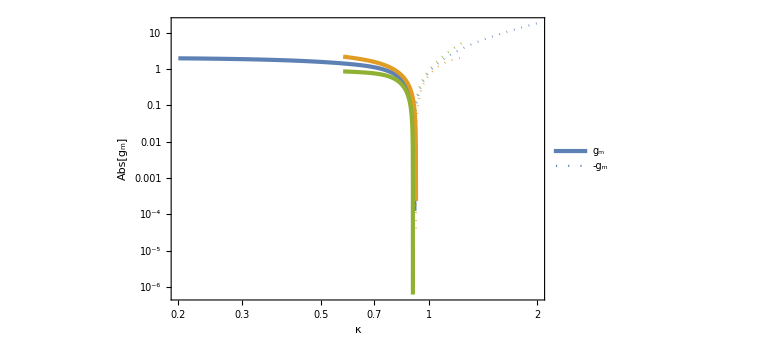

```mathematica
Figgm=LogLogPlot[{gm[kappa,0],-gm[kappa,0],gm[kappa,0.2],-gm[kappa,0.2],gm[kappa,-0.2],-gm[kappa,-0.2]},{kappa,0.2,2},PlotRange->Full,PlotStyle->{AbsoluteThickness[3],{Color[1],Dotted},{Color[2],AbsoluteThickness[3]},{Color[2],Dotted},{Color[3],AbsoluteThickness[3]},{Color[3],Dotted}},FrameLabel->{κ,Abs[Subscript[g, "m"]]},PlotLegends->Placed[{Subscript[g, "m"],-Subscript[g, "m"]},{0.2,0.2}]]
```

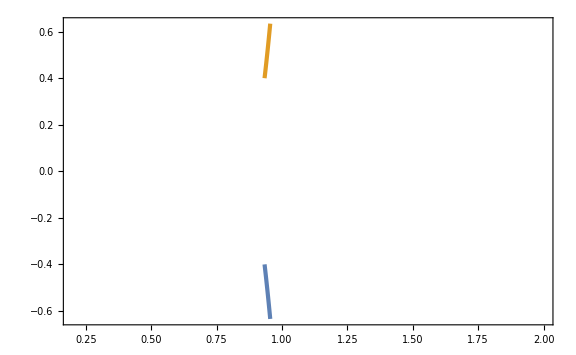

```mathematica
Plot[{gm[kappa,-0.82],-gm[kappa,-0.82]},{kappa,0.2,2},PlotRange->Full]
```

```mathematica
fNLeffmax=82/100;
fNLeffminkc=-5/10;
```

```mathematica
kappa/.FindRoot[gm[kappa,5/10]==0,{kappa,94/100},WorkingPrecision->30]
```

0.931948938890984880696191217549

```mathematica
kappacList=Table[{fNLeff,kappa/.FindRoot[gm[kappa,fNLeff]==0,{kappa,94/100},WorkingPrecision->30]//Quiet},{fNLeff,fNLeffminkc,fNLeffmax,10^-2}];//AbsoluteTiming
```

{1.9396,Null}

```mathematica
Export["kappac_flat_NG.dat",kappacList];
```

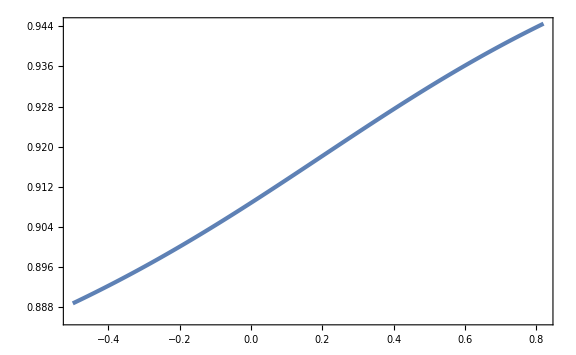

```mathematica
ListPlot[kappacList]
```

```mathematica
kappacint[fNLeff_]=Interpolation[kappacList][fNLeff];
```

```mathematica
Cm[mueff_,kappa_,fNLeff_]=CompactC[xmint[kappa,fNLeff],mueff,kappa,fNLeff];
```

```mathematica
alpha[mueff_,kappa_,fNLeff_]=KK(Cm[mueff,kappa,fNLeff]-Cth)^γ/.{KK->4.2,Cth->0.267,γ->0.36};
```

```mathematica
MoMkW[mueff_,kappa_,fNLeff_]=Collect[alpha[mueff,kappa,fNLeff] xmint[kappa,fNLeff]^2 Exp[2mueff gm[kappa,fNLeff]],mueff];
```

```mathematica
MoMkW[0.6,1,0]
```

2.58198

```mathematica
Solve[KK(1/3(1-(1+mueff xzp)^2)-Cth)^γ x^2 E^(2mueff g)==M,mueff]
```

$Aborted

```mathematica
E^(-2/3 Log[1-3mu g])
```

1/(1-3 g mu)^(2/3)

```mathematica
Solve[KK(mu-mt)^γ/(1-3g mu)^(2/3)x^2==M,mu]
```

$Aborted

```mathematica
Solve[KK(mueff-mt)^γ x^2 E^(2mueff g)==M,mueff]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{mueff→(2 g mt+γ ProductLog[(g ((2^γ ⅇ^(-2 g mt) M)/(KK x^2))^(1/γ))/γ])/(2 g)}}

```mathematica
Solve[MoMkW[mueff,kappa,fNLeff]==M,mueff]
```

$Aborted

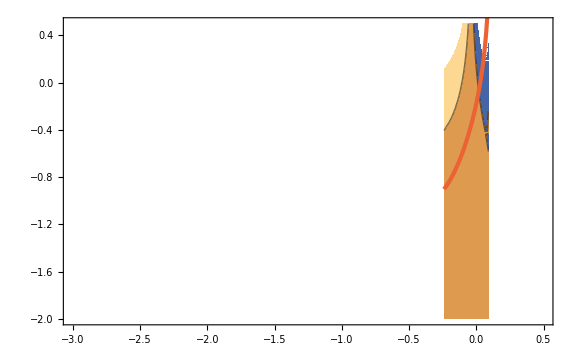

```mathematica
Show[ContourPlot[Log10[MoMkW[10^logm,10^logk,0.2]],{logk,-3,1/2},{logm,-2,1/2}],Plot[Log10[muthint[10^logk,0.2]],{logk,-3,2},PlotStyle->{AbsoluteThickness[3],Color[4]}]]
```

```mathematica
MContour=Table[i,{i,-5,5,1/4}];
```

```mathematica
FigMoMkW=Show[ContourPlot[Log10[MoMkW[10^logm,10^logk]],{logk,-3,0.5},{logm,-2,0.5},Contours->MContour,PlotLegends->BarLegend[Automatic,LegendLabel->Row[{Subscript["log", 10],M[Subscript[OverTilde[μ], 2],κ]/Subscript[M, Subscript[k, "W"]]}]],GridLines->{{Log10[kappac]},None},GridLinesStyle->Directive[Black,Dotted,AbsoluteThickness[2]],FrameLabel->{Row[{Subscript["log", 10]," ",κ}],Subscript["log", 10] Subscript[OverTilde[μ], 2]}],ContourPlot[MoMkW[10^logm,10^logk]==MoMkW[muthint[10^-3],10^-3],{logk,-3,0.5},{logm,-2,0.5},ContourStyle->{Black,AbsoluteThickness[2]}],Plot[Log10[muthint[10^logk]],{logk,-3,2},PlotStyle->{AbsoluteThickness[3],Color[4]}]]
```

-Graphics-

```mathematica
Mc=MoMkW[0.1,kappac]
Mth=MoMkW[muthint[10^-3],10^-3]
```

9.17143

43.762

```mathematica
muthint[10^-3]
```

0.102313

```mathematica
muM[kappa_,MM_]=1/(2gm[kappa])Log[MM/xmint[kappa]^2];
```

```mathematica
FindRoot[muM[kappa,30]==muthint[kappa],{kappa,0.7}]
```

{kappa→0.701322}

```mathematica
FindRoot[muM[kappa,0.001]==muthint[kappa],{kappa,2}]
```

{kappa→1.28126}

```mathematica
kappathList1=Table[{10^logM,kappa/.FindRoot[muM[kappa,10^logM]==muthint[kappa],{kappa,0.908}]},{logM,Log10[Mc]+1/1000,Log10[Mth],1/100}];
```

```mathematica
kappathList2=Table[{10^logM,kappa/.FindRoot[muM[kappa,10^logM]==muthint[kappa],{kappa,0.91}]},{logM,-3,Log10[Mc],1/100}];
```

```mathematica
kappathList=Join[kappathList2,kappathList1];
```

```mathematica
Figkappath=ListLogLinearPlot[kappathList,FrameLabel->{Row[{M,"/",Subscript[M, Subscript[k, "W"]]}],Subscript[κ, th]},GridLines->{{Mc},{kappac}}]
```

-Graphics-

```mathematica
kappathint[MM_]=Interpolation[kappathList][MM];
```

```mathematica
f[z_]=1/2 z(z^2-3)(Erf[1/2 √(5/2)z]+Erf[√(5/2)z])+√(2/(5π))((8/5+31/4 z^2)Exp[-5/8 z^2]+(-8/5+1/2 z^2)Exp[-5/2 z^2]);
PG[z_,m_,s2_]=1/(√(2π s2))Exp[(-(z-m)^2)/(2s2)];
```

```mathematica
npk[mu_,kappa_,As_]=1/(2π)^(3/2)27(√3)/8 f[2 √2 mu kappa^2/(√As)]PG[mu,0,As/8]PG[kappa^2,2/3,As/(24 mu^2)]kappa;
```

```mathematica
nPBH[MM_,As_]:=NIntegrate[2gm[kappa]npk[muM[kappa,MM],kappa,As],{kappa,kappac,kappathint[MM]}]/;MM<Mc
nPBH[MM_,As_]:=NIntegrate[2gm[kappa]npk[muM[kappa,MM],kappa,As],{kappa,kappathint[MM],kappac}]/;Mc<MM<Mth
nPBH[MM_,As_]:=NIntegrate[2gm[kappa]npk[muM[kappa,MM],kappa,As],{kappa,0,kappac}]/;MM>Mth
```

```mathematica
nPBH[10,0.0028]
```

3.90138×10^-116

```mathematica
nPBHList1=ParallelTable[{10^logM,nPBH[10^logM,0.01]},{logM,1,2,1/100}];//AbsoluteTiming
nPBHList2=ParallelTable[{10^logM,nPBH[10^logM,0.0028]},{logM,1,2,1/100}];//AbsoluteTiming
```

InterpolatingFunction::dmval: 
                     16/25
   Input value {10 10     } lies outside the range of data in the
     interpolating function. Extrapolation will be used.

{73.3518,Null}

InterpolatingFunction::dmval: 
                     16/25
   Input value {10 10     } lies outside the range of data in the
     interpolating function. Extrapolation will be used.

{110.149,Null}

```mathematica
Export["nPBH1e-2.dat",nPBHList1];
Export["nPBH28e-4.dat",nPBHList2];
```

```mathematica
gineV=(1.783 10^-33)^-1;
MpcinvineV=(10^6 3.086 10^16)^-1 1.973 10^-7;
KineV=(1.16 10^4)^-1;
MplineV=2.435 10^(18+9);
kminvsinvMpcineV=(10^3 6.582 10^-16)/(3.086 10^16 10^6);
```

```mathematica
n2f=((10^20 gineV (1.56 10^13 MpcinvineV)^3)/(0.12 3 MplineV^2(100kminvsinvMpcineV)^2))^-1
```

1.74505×10^-16

```mathematica
LognPBHList1=Map[Log10,nPBHList1,{2}]//Simplify;
LognPBHList2=Map[Log10,nPBHList2,{2}]//Simplify;
```

```mathematica
nPBHint1[MM_]=10^(Interpolation[LognPBHList1][Log10[MM]]);
nPBHint2[MM_]=10^(Interpolation[LognPBHList2][Log10[MM]]);
```

```mathematica
FigBeta=LogLogPlot[{MM nPBHint2[MM]/n2f,MM nPBHint1[MM]/n2f},{MM,10,100},PlotRange->{10^-31,10^15},GridLines->{None,{1}},FrameLabel->{Row[{M,"/",Subscript[M, Subscript[k, "W"]]}],Row[{M/Subscript[M, Subscript[k, "W"]],β[Row[{M,"/",Subscript[M, Subscript[k, "W"]]}]]/Subscript[β, 0]}]},PlotStyle->{AbsoluteThickness[3],Dashed},PlotLegends->Placed[LineLegend[{Row[{Subscript[A, ζ]==2.8," × ",Superscript[10,-3]}],Subscript[A, ζ]==Superscript[10,-2]},LabelStyle->Directive[Larger,Black,FontFamily->"Palatino"]],{0.25,0.2}]]
```

-Graphics-

```mathematica
MaxfPBH=FindMaximum[MM nPBHint2[MM]/n2f,{MM,40}][[1]]
MaxMM=MM/.FindMaximum[MM nPBHint2[MM]/n2f,{MM,40}][[2]]
```

FindMaximum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient increase in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

0.0115842

FindMaximum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient increase in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

42.2278

```mathematica
FigfPBH=LogLogPlot[{0.01^-0.5 MM/0.01 nPBHint2[MM/0.01]/n2f,0.1^-0.5 MM/0.1 nPBHint2[MM/0.1]/n2f,MM nPBHint2[MM]/n2f,MaxfPBH (MM/MaxMM)^(-1/2)},{MM,0.1,100},PlotRange->{10^-10,100},GridLines->{None,{1}},PlotStyle->{Dashed,{Color[1],Dashed},{Color[1],Dashed},{Color[1],AbsoluteThickness[3]}},FrameLabel->{Row[{M," / (",Superscript[10,20]," g)"}],Subscript[f, PBH]}]
```

InterpolatingFunction::dmval: Input value {0.0000612857} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::munfl: 1/10^2797.23 is too small to represent as a normalized machine number; precision may be lost.

InterpolatingFunction::dmval: Input value {0.0612858} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::munfl: 1/10^2376.04 is too small to represent as a normalized machine number; precision may be lost.

InterpolatingFunction::dmval: Input value {0.12251} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

General::munfl: 1/10^2002.41 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

-Graphics-

## Exp tail

### monochromatic

```mathematica
sigman[n_,ks_,As_]=ks^n √As
psin[n_,r_,ks_]=ks^(2n-4)Sin[ks r]/(ks r)
```

√As ks^n

(ks^(-5+2 n) Sin[ks r])/r

```mathematica
gamma1=sigman[1,ks,As]^2/(sigman[0,ks,As]sigman[2,ks,As])
gamma2=sigman[2,ks,As]^2/(sigman[0,ks,As]sigman[4,ks,As])
gamma3=sigman[3,ks,As]^2/(sigman[2,ks,As]sigman[4,ks,As])
Rb[ks_]=√3 sigman[3,ks,As]/sigman[4,ks,As]
```

1

1

1

(√3)/ks

```mathematica
zfull[zG_]=-1/3 Log[1-3zG];
Normal[Series[zfull[zG],{zG,0,2}]]
```

zG+(3 zG^2)/2

```mathematica
zetaGx[x_,mu_]=mu Sin[x]/x//Simplify
```

(mu Sin[x])/x

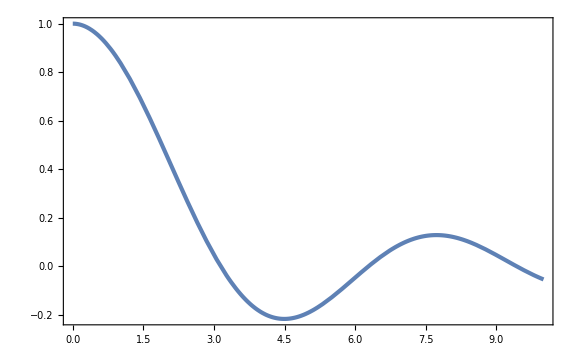

```mathematica
Plot[Sin[x]/x,{x,0,10}]
```

```mathematica
zetabar[x_,mu_]=-1/3 Log[1-3mu Sin[x]/x]//Simplify
```

-1/3 Log[1-(3 mu Sin[x])/x]

```mathematica
CompactC[x_,mu_]=1/3(1-(1+x D[zetabar[x,mu], x])^2)//Simplify
```

-(mu (x Cos[x]-Sin[x]) (2 x+mu x Cos[x]-7 mu Sin[x]))/(3 (x-3 mu Sin[x])^2)

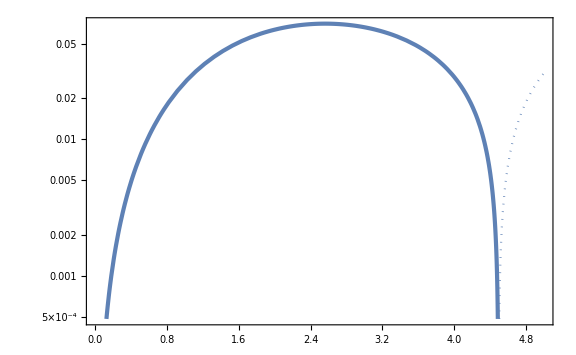

```mathematica
LogPlot[{CompactC[x,0.1],-CompactC[x,0.1]},{x,0,5},PlotStyle->{AbsoluteThickness[3],{Color[1],Dotted}}]
```

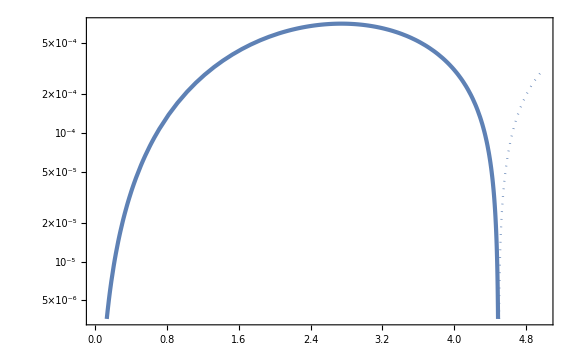

```mathematica
LogPlot[{CompactC[x,0.001],-CompactC[x,0.001]},{x,0,5},PlotStyle->{AbsoluteThickness[3],{Color[1],Dotted}}]
```

```mathematica
rmcond[x_,mu_]=(x-3mu Sin[x])^2/mu(D[zetabar[x,mu], x]+x D[D[zetabar[x,mu], x], x])//Simplify
```

3 mu x+Sin[x]-x^2 Sin[x]-Cos[x] (x+3 mu Sin[x])

```mathematica
rmcond2[x_,mu_]=(1+x D[zetabar[x,mu], x])//Simplify
```

(x+mu x Cos[x]-4 mu Sin[x])/(x-3 mu Sin[x])

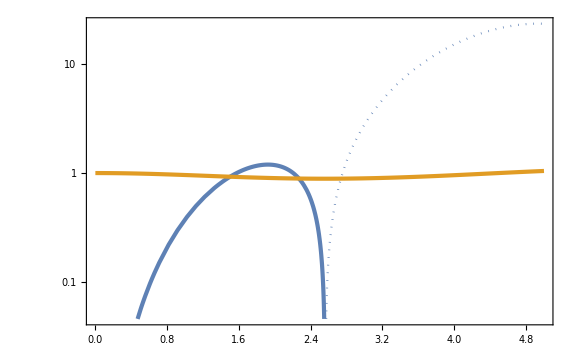

```mathematica
LogPlot[{-rmcond[x,0.1],rmcond[x,0.1],rmcond2[x,0.1],-rmcond2[x,0.1]},{x,0,5},PlotStyle->{AbsoluteThickness[3],{Color[1],Dotted},{AbsoluteThickness[3],Color[2]},{Color[2],Dotted}}]
```

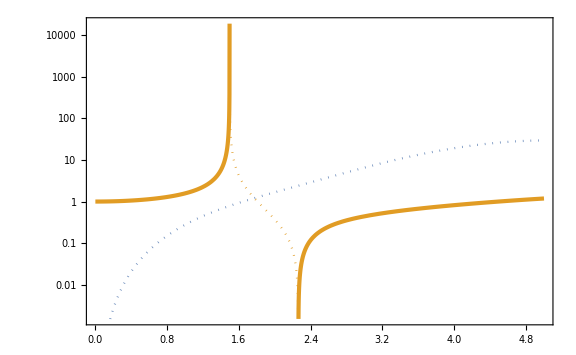

```mathematica
LogPlot[{-rmcond[x,0.5],rmcond[x,0.5],rmcond2[x,0.5],-rmcond2[x,0.5]},{x,0,5},PlotStyle->{AbsoluteThickness[3],{Color[1],Dotted},{AbsoluteThickness[3],Color[2]},{Color[2],Dotted}}]
```

```mathematica
FindRoot[rmcond[x,10^-4]==0,{x,3}]
```

{x→2.74355}

```mathematica
xmList=Table[{mu,x/.FindRoot[rmcond[x,mu]==0,{x,3}]},{mu,10^-4,1/3,10^-4}];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

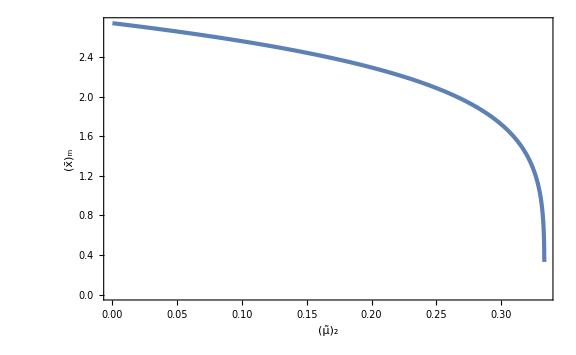

```mathematica
ListPlot[xmList,FrameLabel->{Subscript[OverTilde[μ], 2],Subscript[OverBar[x], "m"]}]
```

```mathematica
xmint[mu_]=Interpolation[xmList][mu];
```

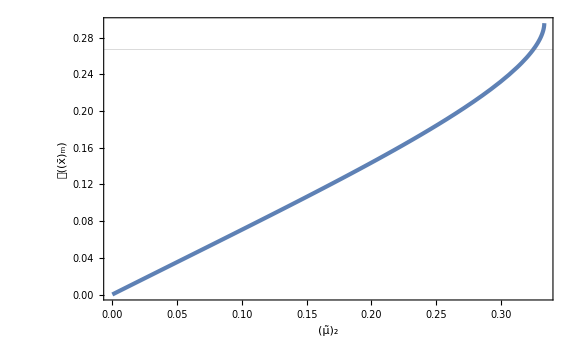

```mathematica
Plot[CompactC[xmint[mu],mu],{mu,10^-4,1/3},GridLines->{None,{0.267}},FrameLabel->{Subscript[OverTilde[μ], 2],𝒞[Subscript[OverBar[x], "m"]]}]
```

```mathematica
muth=mu/.FindRoot[CompactC[xmint[mu],mu]==0.267,{mu,0.3}]
```

0.324784

```mathematica
dLogMdmu[mu_]=D[Log[xmint[mu]^2 Exp[2zetabar[xmint[mu],mu]]], mu];
```

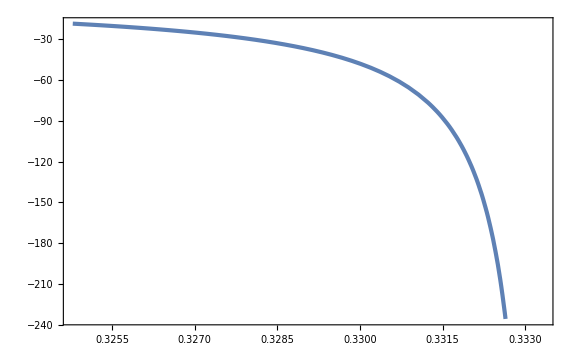

```mathematica
Plot[dLogMdmu[mu],{mu,muth,1/3}]
```

```mathematica
f[z_]=1/2 z(z^2-3)(Erf[1/2 √(5/2)z]+Erf[√(5/2)z])+√(2/(5π))((8/5+31/4 z^2)Exp[-5/8 z^2]+(-8/5+1/2 z^2)Exp[-5/2 z^2]);
```

```mathematica
gineV=(1.783 10^-33)^-1;
MpcinvineV=(10^6 3.086 10^16)^-1 1.973 10^-7;
KineV=(1.16 10^4)^-1;
MplineV=2.435 10^(18+9);
kminvsinvMpcineV=(10^3 6.582 10^-16)/(3.086 10^16 10^6);
```

```mathematica
((10^20 gineV(3/(2π))^(3/2)(1.56 10^13 MpcinvineV)^3)/(0.12 3 MplineV^2(100 kminvsinvMpcineV)^2))^-1
```

5.28928×10^-16

```mathematica
PG[x_,sg2_]=1/(√(2π sg2))Exp[-x^2/(2sg2)];
```

```mathematica
MoMks[mu_]=xmint[mu]^2 Exp[2zetabar[xmint[mu],mu]];
```

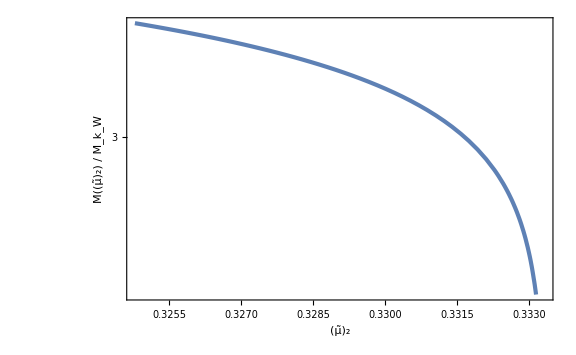

```mathematica
LogPlot[MoMks[mu],{mu,muth,1/3},FrameLabel->{Subscript[OverTilde[μ], 2],Row[{M[Subscript[OverTilde[μ], 2]]," / ",Subscript[M, Subscript[k, "W"]]}]}]
```

```mathematica
fPBH[Mks_,ks_,As_,mu_]=Mks/10^20 MoMks[mu](ks/(1.56 10^13))^3(f[mu/(√As)]PG[mu,As])/(5.3 10^-16)Abs[dLogMdmu[mu]]^-1 UnitStep[mu-muth];
```

```mathematica
fPBH[10^20,1.56 10^13,2.8 10^-3,0.33]
```

7.98637×10^8

```mathematica
fPBHList=Table[{MoMks[mu],fPBH[10^20,1.56 10^13,2.8 10^-3,mu]},{mu,muth,1/3,10^-4}];
```

```mathematica
Mmin=Last[fPBHList][[1]]
```

1.66375

```mathematica
fPBHLogLogList=Map[{Log[#[[1]]],Log[#[[2]]]}&,fPBHList];
```

```mathematica
fPBHint[M_]=Exp[Interpolation[fPBHLogLogList,InterpolationOrder->1][Log[M]]];
```

InterpolatingFunction::dmval: Input value {0.262369} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

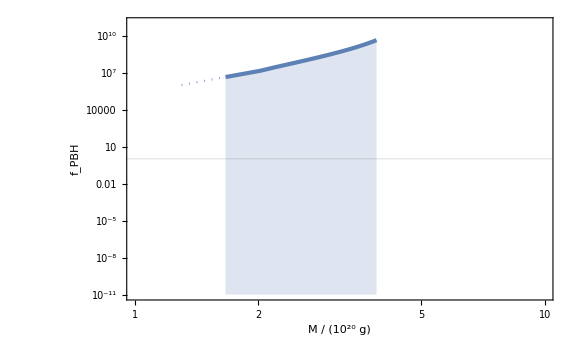

```mathematica
Show[ListLogLogPlot[fPBHList,Filling->Bottom,GridLines->{None,{1}},FrameLabel->{Row[{M," / (10^20 g)"}],Subscript[f, PBH]},PlotRange->{{1,10},{10^-11,10^11}}],LogLogPlot[fPBHint[M],{M,1.3,Mmin},PlotStyle->{Color[1],Dotted}]]
```

## Critical effect

### mono Gauss

```mathematica
sigman[n_,ks_,As_]=ks^n √As
psin[n_,r_,ks_]=Sin[ks r]/(ks r)
```

√As ks^n

Sin[ks r]/(ks r)

```mathematica
gamma1=sigman[1,ks,As]^2/(sigman[0,ks,As]sigman[2,ks,As])
gamma2=sigman[2,ks,As]^2/(sigman[0,ks,As]sigman[4,ks,As])
gamma3=sigman[3,ks,As]^2/(sigman[2,ks,As]sigman[4,ks,As])
Rb[ks_]=√3 sigman[3,ks,As]/sigman[4,ks,As]
```

1

1

1

(√3)/ks

```mathematica
zetabar[x_,mu_]=mu Sin[x]/x//Simplify
```

(mu Sin[x])/x

```mathematica
Plot[Sin[x]/x,{x,0,10}]
```

-Graphics-

```mathematica
CompactC[x_,mu_]=2/3(1-(1+x D[zetabar[x,mu], x])^2)//Simplify
```

(2 (x^2-(x+mu x Cos[x]-mu Sin[x])^2))/(3 x^2)

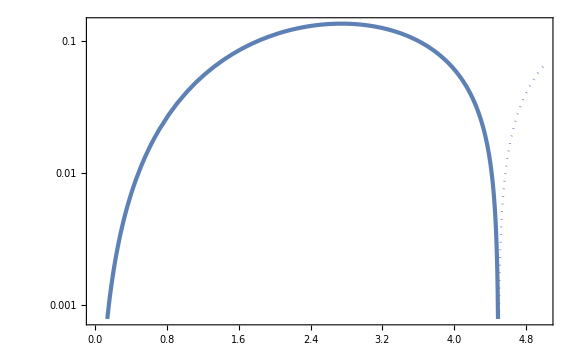

```mathematica
LogPlot[{CompactC[x,0.1],-CompactC[x,0.1]},{x,0,5},PlotStyle->{AbsoluteThickness[3],{Color[1],Dotted}}]
```

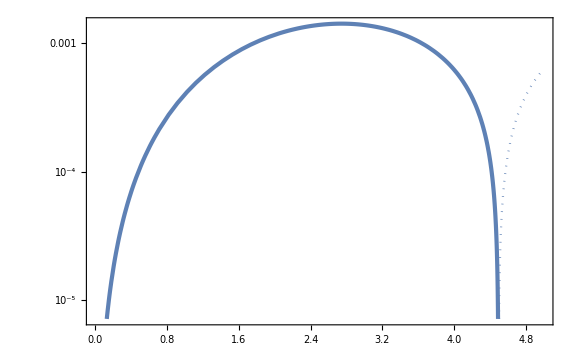

```mathematica
LogPlot[{CompactC[x,0.001],-CompactC[x,0.001]},{x,0,5},PlotStyle->{AbsoluteThickness[3],{Color[1],Dotted}}]
```

```mathematica
rmcond[x_]=-x^2/mu(D[zetabar[x,mu], x]+x D[D[zetabar[x,mu], x], x])//Simplify
```

x Cos[x]+(-1+x^2) Sin[x]

```mathematica
rmcond2[x_,mu_]=(1+x D[zetax[x,mu], x])//Simplify
```

1+mu Cos[x]-(mu Sin[x])/x

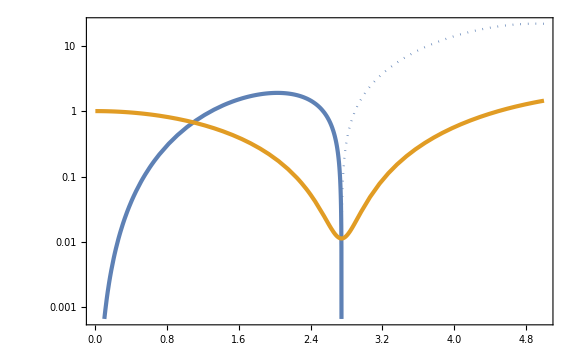

```mathematica
LogPlot[{rmcond[x],-rmcond[x],rmcond2[x,0.93],-rmcond2[x,0.93]},{x,0,5},PlotStyle->{AbsoluteThickness[3],{Color[1],Dotted},{AbsoluteThickness[3],Color[2]},{Color[2],Dotted}}]
```

```mathematica
xm=x/.FindRoot[rmcond[x]==0,{x,3}]
```

2.74371

```mathematica
Cm[mu_]=CompactC[xm,mu]//Simplify
```

0.+1.41747 mu-0.75346 mu^2

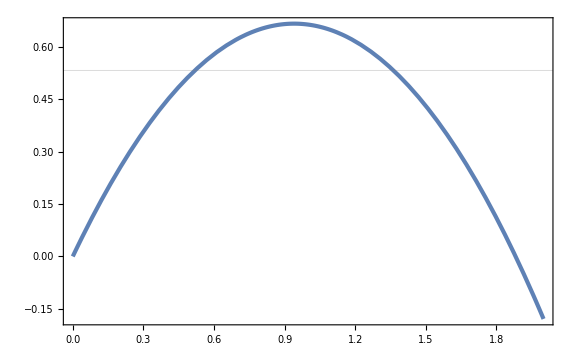

```mathematica
Plot[Cm[mu],{mu,0,2},GridLines->{None,{0.533}}]
```

```mathematica
muth=mu/.Solve[Cm[mu]==0.533,mu][[1]]
```

0.519449

```mathematica
alpha[mu_]=KK(Cm[mu]-Cth)^γ/.{KK->3.3,Cth->0.533,γ->0.36};
```

```mathematica
MoMks[mu_]=xm^2 Exp[2zetabar[xm,mu]]alpha[mu];
dLogMdmu[mu_]=D[Log[MoMks[mu]], mu]//Simplify
```

0.282443+0.51029/((-0.533+1.41747 mu-0.75346 mu^2)^1.)-(0.542491 mu)/((-0.533+1.41747 mu-0.75346 mu^2)^1.)

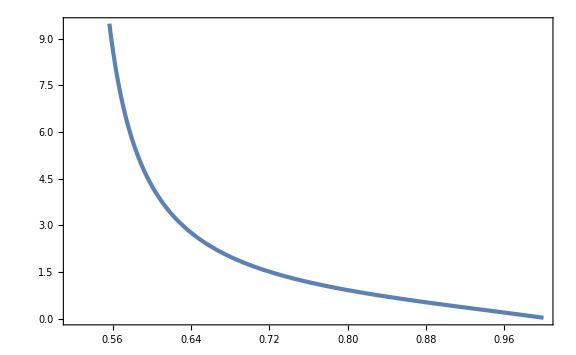

```mathematica
Plot[dLogMdmu[mu],{mu,muth,1}]
```

```mathematica
f[z_]=1/2 z(z^2-3)(Erf[1/2 √(5/2)z]+Erf[√(5/2)z])+√(2/(5π))((8/5+31/4 z^2)Exp[-5/8 z^2]+(-8/5+1/2 z^2)Exp[-5/2 z^2]);
```

```mathematica
gineV=(1.783 10^-33)^-1;
MpcinvineV=(10^6 3.086 10^16)^-1 1.973 10^-7;
KineV=(1.16 10^4)^-1;
MplineV=2.435 10^(18+9);
kminvsinvMpcineV=(10^3 6.582 10^-16)/(3.086 10^16 10^6);
keq=0.07 0.143
```

0.01001

```mathematica
((10^20 gineV(3/(2π))^(3/2)(1.56 10^13 MpcinvineV)^3)/(0.12 3 MplineV^2(100 kminvsinvMpcineV)^2))^-1
```

5.28928×10^-16

```mathematica
PG[x_,sg2_]=1/(√(2π sg2))Exp[-x^2/(2sg2)];
```

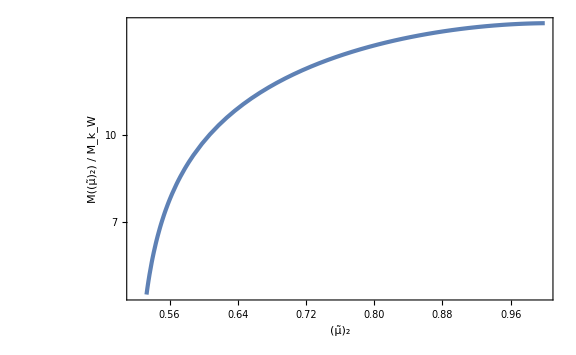

```mathematica
LogPlot[MoMks[mu],{mu,muth,1},FrameLabel->{Subscript[OverTilde[μ], 2],Row[{M[Subscript[OverTilde[μ], 2]]," / ",Subscript[M, Subscript[k, "W"]]}]}]
```

```mathematica
fPBH[Mks_,ks_,As_,mu_]=Mks/10^20 MoMks[mu](ks/(1.56 10^13))^3(f[mu/(√As)]PG[mu,As])/(5.3 10^-16)Abs[dLogMdmu[mu]]^-1 UnitStep[mu-muth];
```

```mathematica
fPBH[10^20((10^5 keq)/(1.56 10^13))^-2,10^5 keq,2.8 10^-3,muth]
```

2.50345×10^-32

```mathematica
fPBHList=Flatten[Table[{MoMks[mu],10^logA,fPBH[10^20((10^5 keq)/(1.56 10^13))^-2,10^5 keq,10^logA,mu]},{mu,muth,0.9,10^-4},{logA,-3,0,10^-2}],1];//AbsoluteTiming
```

General::munfl: Exp[-708.488] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-708.754] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-709.02] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

{243.64,Null}

```mathematica
fPBHint[M_,A_]=Interpolation[fPBHList][M,A]UnitStep[MoMks[0.9]-M];
```

```mathematica
NIntegrate[fPBHint[M,3 10^-3]/M,{M,0.01,20}]
```

4.27206×10^-13

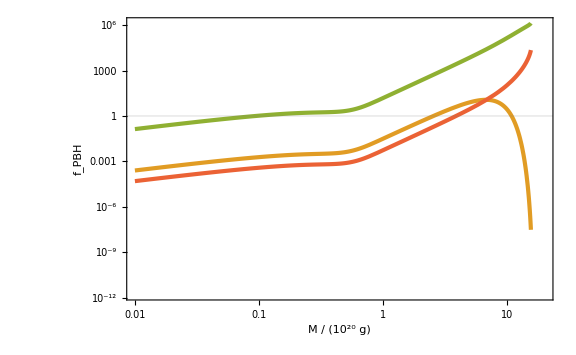

```mathematica
LogLogPlot[{fPBHint[M,10^-3],fPBHint[M,10^-2],fPBHint[M,10^-1],fPBHint[M,1]},{M,0.01,20},GridLines->{None,{1}},FrameLabel->{Row[{M," / (10^20 g)"}],Subscript[f, PBH]}]
```

```mathematica
fPBHAList=Table[{10^logA,NIntegrate[fPBHint[M,10^logA]/M,{M,0.01,20}]},{logA,-3,0,10^-2}];//AbsoluteTiming
```

{118.392,Null}

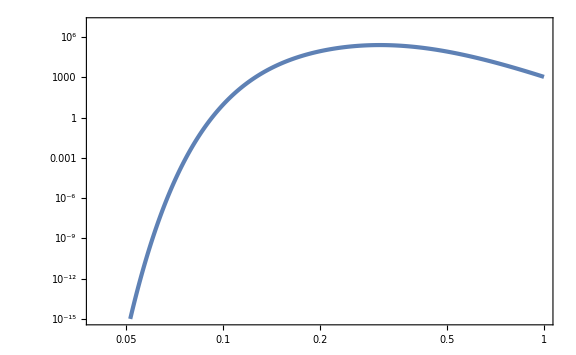

```mathematica
ListLogLogPlot[Map[{Sqrt[#[[1]]],#[[2]]}&,fPBHAList],PlotRange->{{0.04,1},{10^-15,10^7}}]
```

```mathematica
fPBHList=Flatten[Table[{MoMks[mu],10^logA,fPBH[10^20,1.56 10^13,10^logA,mu]},{mu,muth,0.9,10^-4},{logA,-3,0,10^-2}],1];//AbsoluteTiming
```

General::munfl: Exp[-708.488] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-708.754] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-709.02] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

{258.957,Null}

```mathematica
fPBHint[M_,A_]=Interpolation[fPBHList][M,A]UnitStep[MoMks[0.9]-M];
```

```mathematica
NIntegrate[fPBHint[M,3 10^-3]/M,{M,0.01,20}]
```

0.00665776

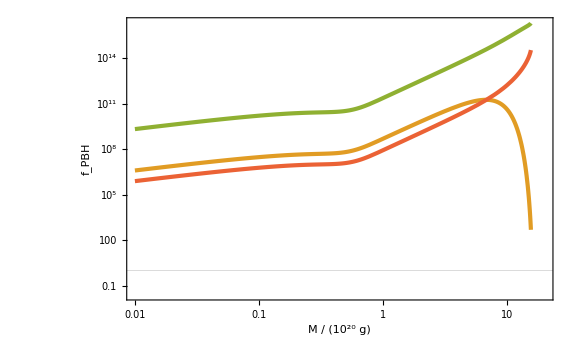

```mathematica
LogLogPlot[{fPBHint[M,10^-3],fPBHint[M,10^-2],fPBHint[M,10^-1],fPBHint[M,1]},{M,0.01,20},GridLines->{None,{1}},FrameLabel->{Row[{M," / (10^20 g)"}],Subscript[f, PBH]}]
```

```mathematica
fPBHAList=Table[{10^logA,NIntegrate[fPBHint[M,10^logA]/M,{M,0.01,20}]},{logA,-3,0,10^-2}];//AbsoluteTiming
```

{112.043,Null}

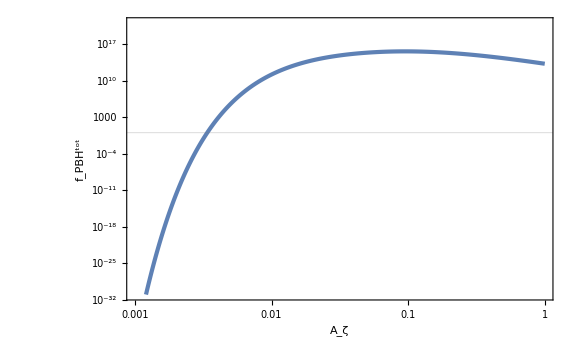

```mathematica
ListLogLogPlot[fPBHAList,FrameLabel->{{Subscript[f, PBH]^tot,None},{Subscript[A, ζ],Row[{SubStar[k]==1.56 10^13," Mpc^-1"}]}},PlotRange->{{10^-3,1},{10^-31,10^21}},GridLines->{None,{1}}]
```

### mono fNL

```mathematica
sigman[n_,ks_,As_]=ks^n √As
psin[n_,r_,ks_]=Sin[ks r]/(ks r)
```

√As ks^n

Sin[ks r]/(ks r)

```mathematica
gamma1=sigman[1,ks,As]^2/(sigman[0,ks,As]sigman[2,ks,As])
gamma2=sigman[2,ks,As]^2/(sigman[0,ks,As]sigman[4,ks,As])
gamma3=sigman[3,ks,As]^2/(sigman[2,ks,As]sigman[4,ks,As])
Rb[ks_]=√3 sigman[3,ks,As]/sigman[4,ks,As]
```

1

1

1

(√3)/ks

```mathematica
zetaGx[x_,mu_]=mu Sin[x]/x//Simplify
```

(mu Sin[x])/x

```mathematica
zetabar[x_,mu_,fNL_]=zetaGx[x,mu]+3/5 fNL zetaGx[x,mu]^2//Simplify
```

(mu Sin[x] (5 x+3 fNL mu Sin[x]))/(5 x^2)

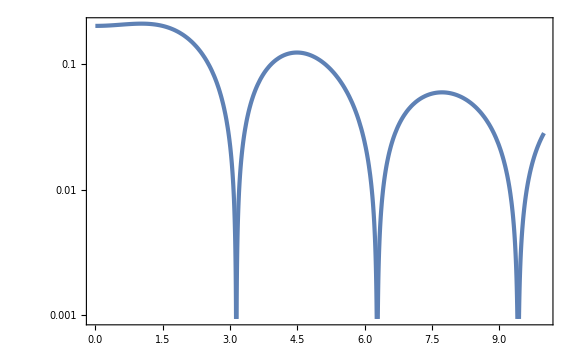

```mathematica
LogPlot[Abs[zetabar[x,0.5,-2]],{x,0,10}]
```

```mathematica
CompactC[x_,mu_,fNL_]=1/3(1-(1+x D[zetabar[x,mu,fNL], x])^2)//Simplify
```

1/3 (1-((5 x^2-5 mu x Sin[x]-6 fNL mu^2 Sin[x]^2+mu x Cos[x] (5 x+6 fNL mu Sin[x]))^2)/(25 x^4))

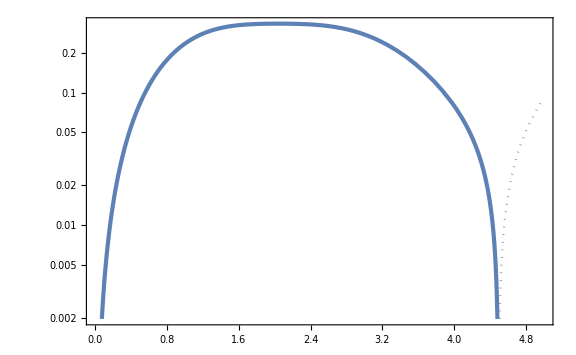

```mathematica
LogPlot[{CompactC[x,0.5,4],-CompactC[x,0.5,4]},{x,0,5},PlotStyle->{AbsoluteThickness[3],{Color[1],Dotted}}]
```

```mathematica
LogPlot[{CompactC[x,0.5,-3],-CompactC[x,0.5,-3]},{x,0,5},PlotStyle->{AbsoluteThickness[3],{Color[1],Dotted}}]
```

-Graphics-

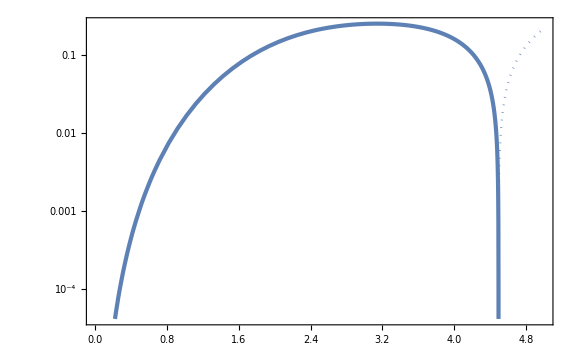

```mathematica
LogPlot[{CompactC[x,0.5,-5/3],-CompactC[x,0.5,-5/3]},{x,0,5},PlotStyle->{AbsoluteThickness[3],{Color[1],Dotted}}]
```

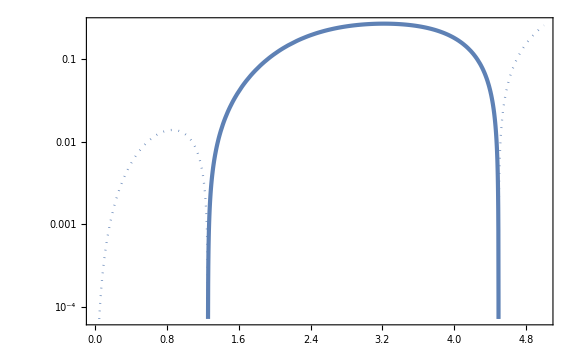

```mathematica
LogPlot[{CompactC[x,0.55,-2],-CompactC[x,0.55,-2]},{x,0,5},PlotStyle->{AbsoluteThickness[3],{Color[1],Dotted}}]
```

```mathematica
rmcond[x_,mu_,fNL_]=(5 x^3)/mu(D[zetabar[x,mu,fNL], x]+x D[D[zetabar[x,mu,fNL], x], x])//Simplify
```

6 fNL mu-5 x^2 Cos[x]+6 fNL mu (-1+x^2) Cos[2 x]+5 x Sin[x]-5 x^3 Sin[x]-9 fNL mu x Sin[2 x]

```mathematica
rmcond2[x_,mu_,fNL_]=5 x^2(1+x D[zetabar[x,mu,fNL], x])//Simplify
```

5 x^2-5 mu x Sin[x]-6 fNL mu^2 Sin[x]^2+mu x Cos[x] (5 x+6 fNL mu Sin[x])

```mathematica
LogPlot[{-rmcond[x,0.5,3],rmcond[x,0.5,3],rmcond2[x,0.5,3],-rmcond2[x,0.5,3]},{x,0,5},PlotStyle->{AbsoluteThickness[3],{Color[1],Dotted},{AbsoluteThickness[3],Color[2]},{Color[2],Dotted}}]
```

-Graphics-

```mathematica
LogPlot[{-rmcond[x,0.5,-3],rmcond[x,0.5,-3],rmcond2[x,0.5,-3],-rmcond2[x,0.5,-3]},{x,0,5},PlotStyle->{AbsoluteThickness[3],{Color[1],Dotted},{AbsoluteThickness[3],Color[2]},{Color[2],Dotted}}]
```

-Graphics-

```mathematica
FindRoot[rmcond[x,0.5,3]==0,{x,3}]
```

{x→2.1157}

```mathematica
xmList=Table[{mufNL,x/.FindRoot[rmcond[x,1,mufNL]==0,{x,3}]},{mufNL,-5/3,5/3,1/10}];
```

```mathematica
ListPlot[xmList,FrameLabel->{Subscript[OverTilde[μ], 2] Subscript[f, NL],Subscript[OverBar[x], "m"]}]
```

-Graphics-

```mathematica
xmint[mufNL_]=Interpolation[xmList][mufNL];
```

```mathematica
Solve[CompactC[xmint[-5/3],mu,1/mu(-5/3)]==0.267,mu]
```

{{mu→0.537651},{mu→1.40366}}

```mathematica
muthList=Table[musol=mu/.Solve[CompactC[xmint[mufNL],mu,mufNL/mu]==0.267,mu][[1]];
{mufNL/musol,musol},{mufNL,-5/3,5/3,1/10}];
```

```mathematica
ListPlot[muthList,FrameLabel->{Subscript[f, NL],Subscript[OverTilde[μ], 2th]}]
```

-Graphics-

```mathematica
fNLmin=First[muthList][[1]]
fNLmax=Last[muthList][[1]]
```

-3.0999

4.87679

```mathematica
muthint[fNL_]=Interpolation[muthList][fNL];
```

```mathematica
Plot[xmint[mu 4]^2 Exp[2zetabar[xmint[mu 4],mu,4]],{mu,0.1,0.6},GridLines->{{muthint[4]},None}]
```

-Graphics-

```mathematica
Plot[xmint[mu 2]^2 Exp[2zetabar[xmint[mu 2],mu,2]],{mu,0.1,0.6},GridLines->{{muthint[2]},None}]
```

-Graphics-

```mathematica
Plot[xmint[mu 0]^2 Exp[2zetabar[xmint[mu 0],mu,0]],{mu,0.1,0.6},GridLines->{{muthint[0]},None}]
```

-Graphics-

```mathematica
Plot[xmint[mu (-2)]^2 Exp[2zetabar[xmint[mu (-2)],mu,-2]],{mu,0.1,0.6},GridLines->{{muthint[-2]},None}]
```

-Graphics-

```mathematica
dLogMdmu[mu_,fNL_]=D[Log[xmint[mu fNL]^2 Exp[2zetabar[xmint[mu fNL],mu,fNL]]], mu];
```

```mathematica
Plot[{dLogMdmu[mu,-2],dLogMdmu[mu,0],dLogMdmu[mu,2],dLogMdmu[mu,4]},{mu,0.1,0.6},GridLines->{{muthint[-2],muthint[0],muthint[2],muthint[4]},None}]
```

-Graphics-

```mathematica
Plot[dLogMdmu[muthint[fNL],fNL],{fNL,fNLmin,fNLmax}(*,FrameLabel->{Subscript[f, NL],Subscript[Abs[Row[{"d log ",M}]/("d"Subscript[OverTilde[μ], 2])], Subscript[OverTilde[μ], 2]==Subscript[OverTilde[μ], 2th]]}*)]
```

-Graphics-

```mathematica
Plot[dLogMdmu[mu,-2],{mu,muthint[-2]-0.1,muthint[-2]+0.1}]
```

-Graphics-

```mathematica
f[z_]=1/2 z(z^2-3)(Erf[1/2 √(5/2)z]+Erf[√(5/2)z])+√(2/(5π))((8/5+31/4 z^2)Exp[-5/8 z^2]+(-8/5+1/2 z^2)Exp[-5/2 z^2]);
```

```mathematica
gineV=(1.783 10^-33)^-1;
MpcinvineV=(10^6 3.086 10^16)^-1 1.973 10^-7;
KineV=(1.16 10^4)^-1;
MplineV=2.435 10^(18+9);
kminvsinvMpcineV=(10^3 6.582 10^-16)/(3.086 10^16 10^6);
```

```mathematica
((10^20 gineV(3/(2π))^(3/2)(1.56 10^13 MpcinvineV)^3)/(0.12 3 MplineV^2(100 kminvsinvMpcineV)^2))^-1
```

5.28928×10^-16

```mathematica
PG[x_,sg2_]=1/(√(2π sg2))Exp[-x^2/(2sg2)];
```

```mathematica
MoMks[mu_,fNL_]=xmint[mu fNL]^2 Exp[2zetabar[xmint[mu fNL],mu,fNL]];
```

```mathematica
fPBH[Mks_,ks_,As_,mu_,fNL_]=Mks/10^20 MoMks[mu,fNL](ks/(1.56 10^13))^3(f[mu/(√As)]PG[mu,As])/(5.3 10^-16)dLogMdmu[mu,fNL]^-1 UnitStep[mu-muthint[fNL]];
```

```mathematica
muthint[-2]
```

0.551735

```mathematica
fPBH[10^20,1.56 10^13,2.8 10^-3,0.6,0]
```

7.70761×10^-8

```mathematica
fPBHListfNLm2=Table[{MoMks[mu,-2],fPBH[10^20,1.56 10^13,2.8 10^-3,mu,-2]},{mu,muthint[-2]-0.1,5/3 1/2,0.01}];
fPBHListfNL0=Table[{MoMks[mu,0],fPBH[10^20,1.56 10^13,2.8 10^-3,mu,0]},{mu,muthint[0]-0.1,1,0.01}];
fPBHListfNLp2=Table[{MoMks[mu,2],fPBH[10^20,1.56 10^13,2.8 10^-3,mu,2]},{mu,muthint[2]-0.1,5/3 1/2,0.01}];
fPBHListfNLp4=Table[{MoMks[mu,4],fPBH[10^20,1.56 10^13,2.8 10^-3,mu,4]},{mu,muthint[4]-0.1,5/3 1/4,0.01}];
fPBHListfNLp4Ex=Table[{MoMks[mu,4],fPBH[10^20,1.56 10^13,2.8 10^-3,mu,4]},{mu,5/3 1/4,5/3 1/4+0.05,0.01}];
```

General::munfl: Exp[-708.863] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-724.864] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-741.043] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {1.64233} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {1.66141} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {1.66667} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

```mathematica
Show[ListLogPlot[{fPBHListfNL0,fPBHListfNLp2,fPBHListfNLp4,fPBHListfNLm2},PlotRange->{{6,11},{10^-11,10^11}},Filling->Bottom,GridLines->{None,{1}},FrameLabel->{Row[{M," / (10^20 g)"}],Subscript[f, PBH]},PlotLegends->Placed[LineLegend[{Subscript[f, NL]==0,2,4,-2},LabelStyle->Directive[Black,Larger,FontFamily->"Palatino"]],{0.8,0.75}]],ListLogPlot[fPBHListfNLp4Ex,PlotStyle->{Color[3],Dotted}]]
```

-Graphics-

### mono exp

```mathematica
sigman[n_,ks_,As_]=ks^n √As
psin[n_,r_,ks_]=ks^(2n-4)Sin[ks r]/(ks r)
```

√As ks^n

(ks^(-5+2 n) Sin[ks r])/r

```mathematica
gamma1=sigman[1,ks,As]^2/(sigman[0,ks,As]sigman[2,ks,As])
gamma2=sigman[2,ks,As]^2/(sigman[0,ks,As]sigman[4,ks,As])
gamma3=sigman[3,ks,As]^2/(sigman[2,ks,As]sigman[4,ks,As])
Rb[ks_]=√3 sigman[3,ks,As]/sigman[4,ks,As]
```

1

1

1

(√3)/ks

```mathematica
zfull[zG_]=-1/3 Log[1-3zG];
Normal[Series[zfull[zG],{zG,0,2}]]
```

zG+(3 zG^2)/2

```mathematica
zetaGx[x_,mu_]=mu Sin[x]/x//Simplify
```

(mu Sin[x])/x

```mathematica
Plot[Sin[x]/x,{x,0,10}]
```

-Graphics-

```mathematica
zetabar[x_,mu_]=-1/3 Log[1-3mu Sin[x]/x]//Simplify
```

-1/3 Log[1-(3 mu Sin[x])/x]

```mathematica
CompactC[x_,mu_]=1/3(1-(1+x D[zetabar[x,mu], x])^2)//Simplify
```

-(mu (x Cos[x]-Sin[x]) (2 x+mu x Cos[x]-7 mu Sin[x]))/(3 (x-3 mu Sin[x])^2)

```mathematica
LogPlot[{CompactC[x,0.1],-CompactC[x,0.1]},{x,0,5},PlotStyle->{AbsoluteThickness[3],{Color[1],Dotted}}]
```

-Graphics-

```mathematica
LogPlot[{CompactC[x,0.001],-CompactC[x,0.001]},{x,0,5},PlotStyle->{AbsoluteThickness[3],{Color[1],Dotted}}]
```

-Graphics-

```mathematica
rmcond[x_,mu_]=(x-3mu Sin[x])^2/mu(D[zetabar[x,mu], x]+x D[D[zetabar[x,mu], x], x])//Simplify
```

3 mu x+Sin[x]-x^2 Sin[x]-Cos[x] (x+3 mu Sin[x])

```mathematica
rmcond2[x_,mu_]=(1+x D[zetabar[x,mu], x])//Simplify
```

(x+mu x Cos[x]-4 mu Sin[x])/(x-3 mu Sin[x])

```mathematica
LogPlot[{-rmcond[x,0.1],rmcond[x,0.1],rmcond2[x,0.1],-rmcond2[x,0.1]},{x,0,5},PlotStyle->{AbsoluteThickness[3],{Color[1],Dotted},{AbsoluteThickness[3],Color[2]},{Color[2],Dotted}}]
```

-Graphics-

```mathematica
LogPlot[{-rmcond[x,0.5],rmcond[x,0.5],rmcond2[x,0.5],-rmcond2[x,0.5]},{x,0,5},PlotStyle->{AbsoluteThickness[3],{Color[1],Dotted},{AbsoluteThickness[3],Color[2]},{Color[2],Dotted}}]
```

-Graphics-

```mathematica
FindRoot[rmcond[x,10^-4]==0,{x,3}]
```

{x→2.74355}

```mathematica
dmu=10^-5;
```

```mathematica
xmList=Table[{mu,x/.FindRoot[rmcond[x,mu]==0,{x,3}]},{mu,dmu,1/3,dmu}];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

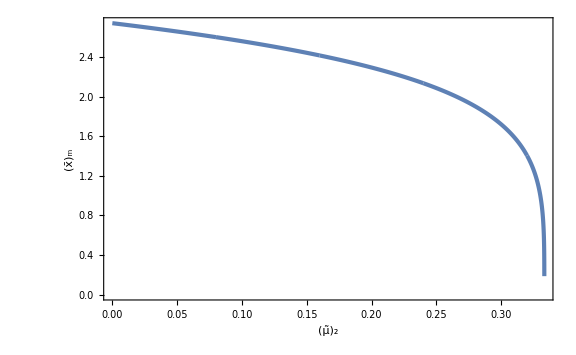

```mathematica
ListPlot[xmList,FrameLabel->{Subscript[OverTilde[μ], 2],Subscript[OverBar[x], "m"]}]
```

```mathematica
xmint[mu_]=Interpolation[xmList][mu];
```

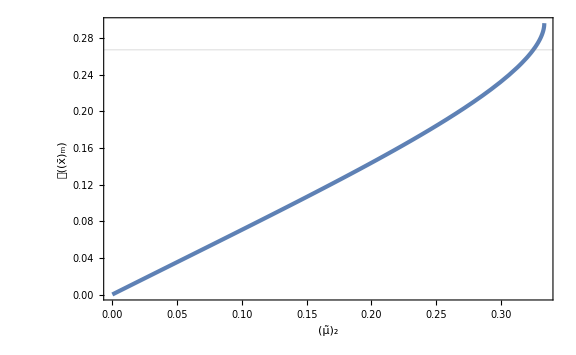

```mathematica
Plot[CompactC[xmint[mu],mu],{mu,10^-4,1/3},GridLines->{None,{0.267}},FrameLabel->{Subscript[OverTilde[μ], 2],𝒞[Subscript[OverBar[x], "m"]]}]
```

```mathematica
muth=mu/.FindRoot[CompactC[xmint[mu],mu]==0.267,{mu,0.3}]
```

0.324784

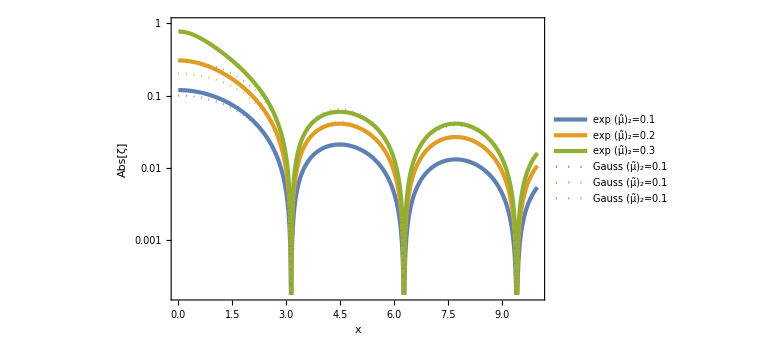

```mathematica
LogPlot[{Abs[zetabar[x,0.1]],Abs[zetabar[x,0.2]],Abs[zetabar[x,0.3]],Abs[zetaGx[x,0.1]],Abs[zetaGx[x,0.2]],Abs[zetaGx[x,0.3]]},{x,0,10},PlotStyle->{AbsoluteThickness[3],AbsoluteThickness[3],AbsoluteThickness[3],{Color[1],Dotted},{Color[2],Dotted},{Color[3],Dotted}},FrameLabel->{x,Abs[ζ̄]},PlotLegends->Placed[LineLegend[{"exp (μ̃)_2=0.1","exp (μ̃)_2=0.2","exp (μ̃)_2=0.3","Gauss (μ̃)_2=0.1","Gauss (μ̃)_2=0.1","Gauss (μ̃)_2=0.1"},LabelStyle->Directive[Black,Larger,FontFamily->"Palatino"],LegendLayout->{"Row",2},LegendMarkerSize->20],{0.6,0.85}]]
```

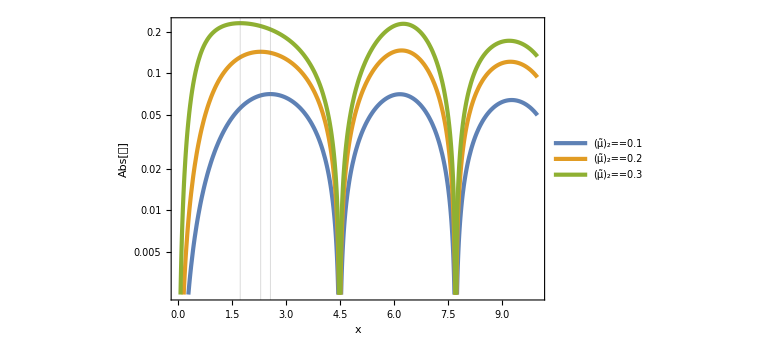

```mathematica
LogPlot[{Abs[CompactC[x,0.1]],Abs[CompactC[x,0.2]],Abs[CompactC[x,0.3]]},{x,0,10},FrameLabel->{x,Abs[𝒞]},PlotLegends->Placed[LineLegend[{Subscript[μ̃, 2]==0.1,Subscript[μ̃, 2]==0.2,Subscript[μ̃, 2]==0.3},LabelStyle->Directive[Black,Larger,FontFamily->"Palatino"],LegendMarkerSize->20],{0.6,0.2}],GridLines->{{xmint[0.1],xmint[0.2],xmint[0.3]},None}]
```

```mathematica
Cm[mu_]=CompactC[xmint[mu],mu];
```

```mathematica
alpha[mu_]=KK(Cm[mu]-Cth)^γ/.{KK->4.2,Cth->0.267,γ->0.36};
```

```mathematica
alpha[0.325]
```

0.253885

```mathematica
MoMks[mu_]=xmint[mu]^2 Exp[2zetabar[xmint[mu],mu]]alpha[mu];
dLogMdmu[mu_]=D[Log[MoMks[mu]], mu];
```

```mathematica
mumax=mu/.FindMaximum[{MoMks[mu],muth<mu<1/3},{mu,0.33}][[2]]
Mmax=MoMks[mumax]
```

0.33132

2.91933

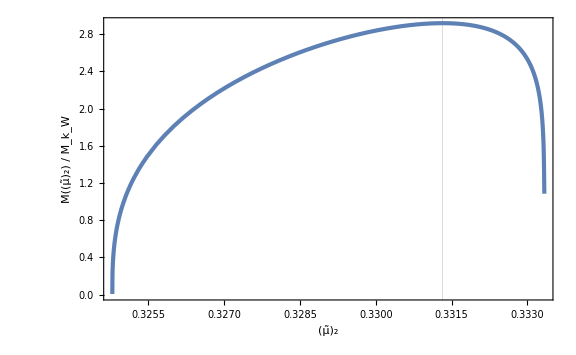

```mathematica
Plot[MoMks[mu],{mu,muth,1/3},FrameLabel->{Subscript[OverTilde[μ], 2],Row[{M[Subscript[OverTilde[μ], 2]]," / ",Subscript[M, Subscript[k, "W"]]}]},GridLines->{{mumax},None}]
```

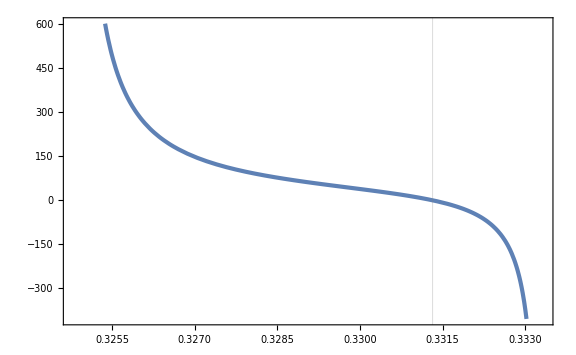

```mathematica
Plot[dLogMdmu[mu],{mu,muth,1/3},GridLines->{{mumax},None}]
```

```mathematica
f[z_]=1/2 z(z^2-3)(Erf[1/2 √(5/2)z]+Erf[√(5/2)z])+√(2/(5π))((8/5+31/4 z^2)Exp[-5/8 z^2]+(-8/5+1/2 z^2)Exp[-5/2 z^2]);
```

```mathematica
gineV=(1.783 10^-33)^-1;
MpcinvineV=(10^6 3.086 10^16)^-1 1.973 10^-7;
KineV=(1.16 10^4)^-1;
MplineV=2.435 10^(18+9);
kminvsinvMpcineV=(10^3 6.582 10^-16)/(3.086 10^16 10^6);
```

```mathematica
((10^20 gineV(3/(2π))^(3/2)(1.56 10^13 MpcinvineV)^3)/(0.12 3 MplineV^2(100 kminvsinvMpcineV)^2))^-1
```

5.28928×10^-16

```mathematica
PG[x_,sg2_]=1/(√(2π sg2))Exp[-x^2/(2sg2)];
```

```mathematica
fPBH[Mks_,ks_,As_,mu_]=Mks/10^20 MoMks[mu](ks/(1.56 10^13))^3(f[mu/(√As)]PG[mu,As])/(5.3 10^-16)Abs[dLogMdmu[mu]]^-1 UnitStep[mu-muth];
```

```mathematica
fPBH[10^20,1.56 10^13,2.8 10^-3,0.33]
```

8.41159×10^8

```mathematica
fPBHlowList=Table[{MoMks[mu],fPBH[10^20,1.56 10^13,1.35 10^-3(*2.8 10^-3*),mu]},{mu,muth+10^-9,mumax,dmu}];
fPBHhighList=Table[{MoMks[mu],fPBH[10^20,1.56 10^13,1.35 10^-3(*2.8 10^-3*),mu]},{mu,mumax+10^-9,1/3-dmu,dmu}];
```

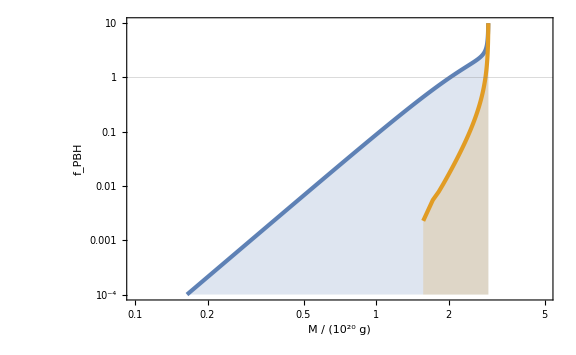

```mathematica
ListLogLogPlot[{fPBHlowList,fPBHhighList},Filling->Bottom,GridLines->{None,{1}},FrameLabel->{Row[{M," / (10^20 g)"}],Subscript[f, PBH]},PlotRange->{{10^-1,5},{10^-4,10^1}}]
```

```mathematica
fPBHlowint[M_]=Interpolation[fPBHlowList][M];
fPBHhighint[M_]=Interpolation[fPBHhighList][M];
```

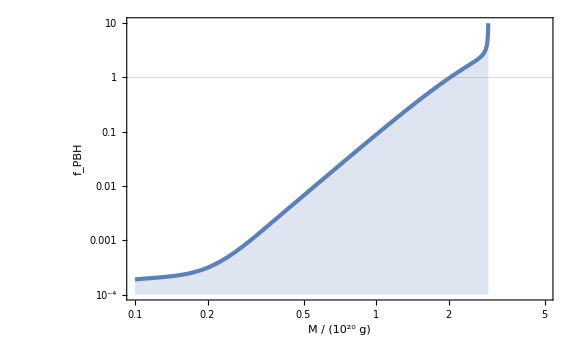

```mathematica
LogLogPlot[{fPBHlowint[M]},{M,0.1,Mmax},Filling->Bottom,GridLines->{None,{1}},FrameLabel->{Row[{M," / (10^20 g)"}],Subscript[f, PBH]},PlotRange->{{0.1,5},{10^-4,10}}]
```

```mathematica
fPBHtot[M_]:=NIntegrate[fPBHlowint[Mp]/Mp,{Mp,0.2,M}]
```

```mathematica
fPBHtotList=Table[{M,fPBHtot[M]},{M,0.2,Mmax,10^-2}];//AbsoluteTiming
```

{55.0556,Null}

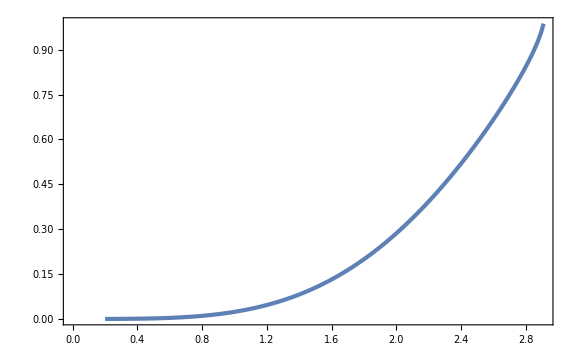

```mathematica
ListPlot[fPBHtotList]
```

```mathematica
fPBHtotint[M_]=Interpolation[fPBHtotList][M];
```

```mathematica
dLogfdM[M_]=D[Log[fPBHtotint[M]], M];
```

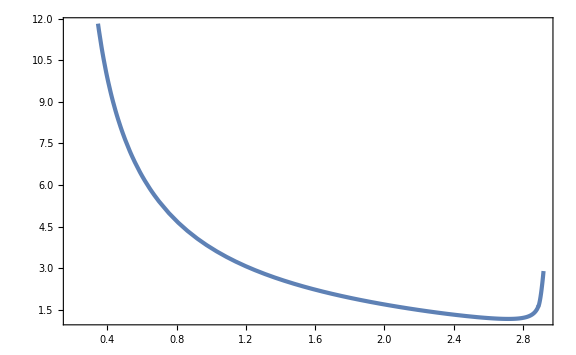

```mathematica
Plot[dLogfdM[M],{M,0.2,Mmax}]
```

#### Riotto

```mathematica
MoMH[dl_]=κ((dl-3/8 dl^2)-dc)^γ/.{κ->3.3,γ-> 0.36,dc->0.59};
```

```mathematica
dlc=4/3(1-Sqrt[1-3/2 dc])/.{dc->0.59}
```

0.881178

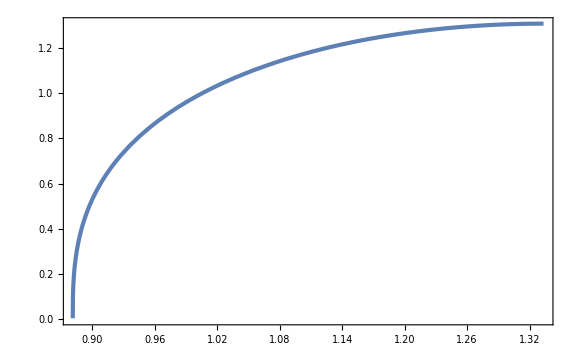

```mathematica
Plot[MoMH[dl],{dl,dlc,4/3}]
```

```mathematica
dLogMddl[dl_]=D[Log[MoMH[dl]], dl];
dMddl[dl_]=D[MoMH[dl], dl];
```

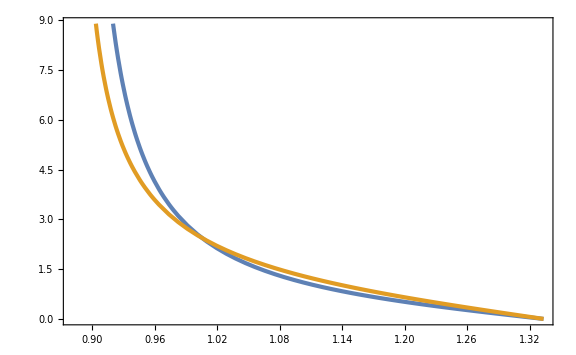

```mathematica
Plot[{dLogMddl[dl],dMddl[dl]},{dl,dlc,4/3}]
```

```mathematica
s2X[A_]=16/9 3^2 A;
s2Y[A_]=9A;
```

```mathematica
P[dl_,A_]=E^(-1/(2s2Y[A]))/(2π(s2X[A]+s2Y[A] dl^2)^(3/2))Sqrt[s2X[A]](2Sqrt[s2Y[A](s2X[A]+s2Y[A] dl^2)]+Sqrt[2π s2X[A]]Exp[s2X[A]/(2s2X[A]s2Y[A]+2 s2Y[A]^2 dl^2)]Erf[Sqrt[s2X[A]]/Sqrt[2s2Y[A](s2X[A]+s2Y[A] dl^2)]]);
```

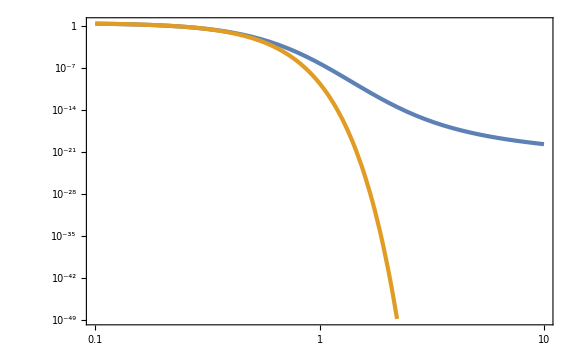

```mathematica
LogLogPlot[{P[dl,1.35 10^-3],Exp[-dl^2/(2s2X[1.35 10^-3])]/Sqrt[2π s2X[1.35 10^-3]]},{dl,10^-1,10}]
```

```mathematica
beta[A_]:=NIntegrate[MoMH[dl]P[dl,A],{dl,dlc,4/3}];
```

```mathematica
((1/(6 10^-9))((2 10^33)/10^20)^(1/2))^-1//N
```

1.34164×10^-15

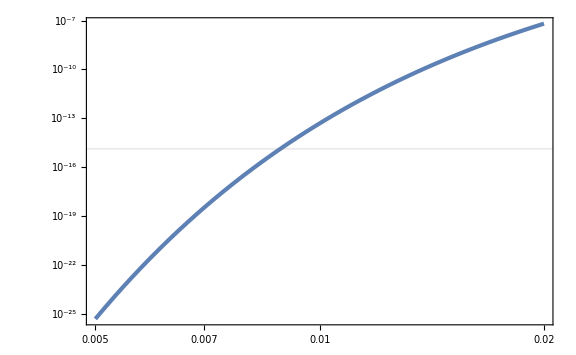

```mathematica
LogLogPlot[beta[s2/16],{s2,0.005,0.02},GridLines->{None,{1.34 10^-15}}]
```

```mathematica
FindRoot[beta[A]==1.34 10^-15,{A,0.007/16}]
```

NIntegrate::inumr: The integrand (2.10085 √A (-0.59+dl-(3 «1»)/8)^0.36 ⅇ^(-1/18/A) (6 √(A (16 A+9 A Power[«2»]))+4 √A ⅇ^((16 A)/(Times[«2»]«1»Times«1»«1»])) √(2 π) Erf[(2 √2 √A)/(3 √(A Plus[«2»]))]))/((16 A+9 A dl^2)^(3/2)) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0.881178,4/3}}.

NIntegrate::inumr: The integrand 3.3 (-0.59+dl-(3«1»«1»)/8)^0.36 (-(3 √A (16+9 dl^2) ⅇ^(-1/18/A) (6 √(A Plus[«2»])+4 √A ⅇ^(16 A Power[«2»]) √(2 π) Erf[2/3 Power[«2»] Power[«2»] Power[«2»]]))/((16 A+9 A dl^2)^(5/2) π)+(ⅇ^(-1/18/A) (6 √(A Plus[«2»])+4 √A ⅇ^(«1») √(2 π) Erf[2/3 Power[«2»] Power[«2»] Power[«2»]]))/(9 A^(3/2) (16 A+9 A dl^2)^(3/2) π)+(ⅇ^(-1/18/A) (6 √(A Plus[«2»])+«1»))/(√A (16 A+9 A («2»)^2)^(3/2) π)+(2 √A ⅇ^(-1/18/A) («1»))/((16 A+9 A dl^2)^(3/2) π)) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0.881178,4/3}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

{A→0.000553127}

```mathematica
dLogbdM[dl_,A_]:=(MoMH[dl]P[dl,A] Abs[dMddl[dl]]^-1)/beta[A];
```

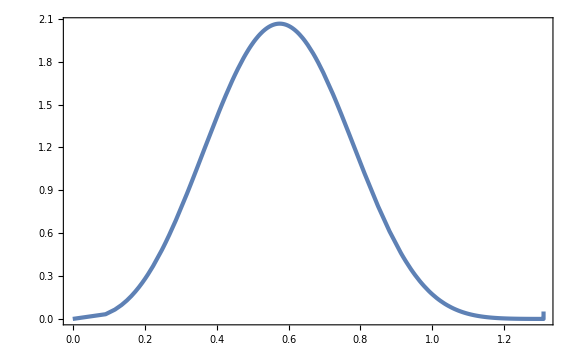

```mathematica
ParametricPlot[{MoMH[dl],dLogbdM[dl,10^-2/16]},{dl,dlc,4/3},PlotRange->Full]
```

```mathematica
dbetadLogM[dl_,A_]=MoMH[dl]P[dl,A] Abs[dLogMddl[dl]]^-1;
```

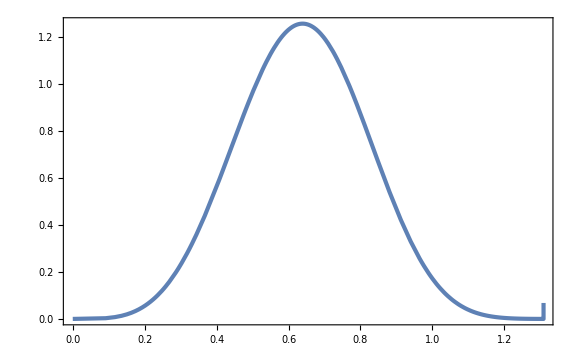

```mathematica
ParametricPlot[{MoMH[dl],1/beta[10^-2/16] dbetadLogM[dl,10^-2/16]},{dl,dlc,4/3}]
```

```mathematica
fPBHRiotto[dl_,A_]=(dbetadLogM[dl,A]/(6 10^-9))((2 10^33)/10^20)^(1/2);
```

```mathematica
ddl=10^-5;
```

```mathematica
fPBHListRiotto=Table[{MoMH[dl],fPBHRiotto[dl,(*1.35*)0.52 10^-3]},{dl,dlc+10^-7,4/3-10^-1,ddl}];
```

```mathematica
fPBHintRiotto[M_]=Interpolation[fPBHListRiotto][M];
```

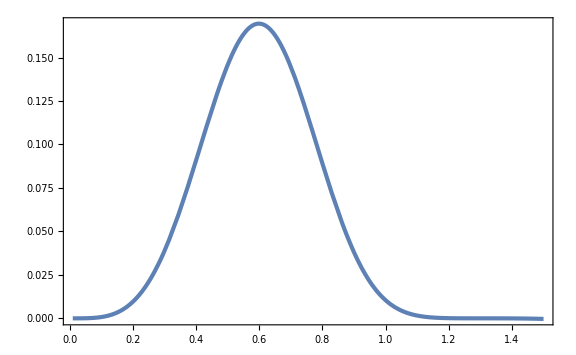

```mathematica
Plot[fPBHintRiotto[M],{M,0.01,1.5}]
```

```mathematica
NIntegrate[fPBHintRiotto[M]/M,{M,0.1,20}]
```

1.18491

```mathematica
ListLogLogPlot[{fPBHlowList,fPBHListRiotto},FrameLabel->{Row[{M," / (10^20 g)"}],Subscript[f, PBH]},PlotRange->{{0.1,20},{10^-4,10}},PlotLegends->Placed[{"Yoo","Riotto"},{0.7,0.2}]]
```

-Graphics-

## Mean C

### mono Gauss

```mathematica
sigman[n_,ks_,As_]=ks^n √As
psin[n_,r_,ks_]=Sin[ks r]/(ks r)
```

√As ks^n

Sin[ks r]/(ks r)

```mathematica
gamma1=sigman[1,ks,As]^2/(sigman[0,ks,As]sigman[2,ks,As])
gamma2=sigman[2,ks,As]^2/(sigman[0,ks,As]sigman[4,ks,As])
gamma3=sigman[3,ks,As]^2/(sigman[2,ks,As]sigman[4,ks,As])
Rb[ks_]=√3 sigman[3,ks,As]/sigman[4,ks,As]
```

1

1

1

(√3)/ks

```mathematica
zetabar[x_,mu_]=mu Sin[x]/x//Simplify
```

(mu Sin[x])/x

```mathematica
Plot[zetabar[x,1],{x,0,10}]
```

-Graphics-

```mathematica
CompactC[x_,mu_]=2/3(1-(1+x D[zetabar[x,mu], x])^2)//Simplify
```

(2 (x^2-(x+mu x Cos[x]-mu Sin[x])^2))/(3 x^2)

```mathematica
<<init`
```

```mathematica
LogPlot[{CompactC[x,0.1],-CompactC[x,0.1]},{x,0,5},PlotStyle->{AbsoluteThickness[3],{Color[1],Dotted}}]
```

-Graphics-

```mathematica
LogPlot[{CompactC[x,10],-CompactC[x,10]},{x,0,5},PlotStyle->{AbsoluteThickness[3],{Color[1],Dotted}}]
```

-Graphics-

```mathematica
(D[zetabar[x,mu], x]+x D[D[zetabar[x,mu], x], x])//Simplify
```

-(mu (x Cos[x]+(-1+x^2) Sin[x]))/x^2

```mathematica
rmcond1[x_]=-x^2/mu(D[zetabar[x,mu], x]+x D[D[zetabar[x,mu], x], x])//Simplify
```

x Cos[x]+(-1+x^2) Sin[x]

```mathematica
rmcond2[x_,mu_]=(1+x D[zetabar[x,mu], x])//Simplify
```

1+mu Cos[x]-(mu Sin[x])/x

```mathematica
LogPlot[{rmcond1[x],-rmcond1[x],rmcond2[x,0.95],-rmcond2[x,0.95]},{x,0,5},PlotStyle->{AbsoluteThickness[3],{Color[1],Dotted},{AbsoluteThickness[3],Color[2]},{Color[2],Dotted}}]
```

-Graphics-

```mathematica
xm=x/.FindRoot[rmcond1[x]==0,{x,3}]
```

2.74371

```mathematica
(1/0.12(1.56 10^13)/0.07(106.75/3.38)^(1/6)1/(2(Sqrt[2]-1)xm))^-1
```

6.88396×10^-16

```mathematica
Rarea[x_,mu_]=E^zetabar[x,mu] x
```

ⅇ^((mu Sin[x])/x) x

```mathematica
D[Rarea[x,mu], x]//Simplify
```

(ⅇ^((mu Sin[x])/x) (x+mu x Cos[x]-mu Sin[x]))/x

```mathematica
Plot[Rarea[x,2],{x,0,5}]
```

-Graphics-

```mathematica
rmcond2minList=Table[{mu,FindMinimum[rmcond2[x,mu],{x,2.7}][[1]]},{mu,0.9,1,10^-2}];
```

```mathematica
ListPlot[rmcond2minList]
```

-Graphics-

```mathematica
rmcond2minint[mu_]=Interpolation[rmcond2minList][mu];
```

```mathematica
mutype2=mu/.FindRoot[rmcond2minint[mu]==0,{mu,0.94}]
```

0.940642

```mathematica
Cx[x_,mu_]=D[CompactC[x,mu], x]//Simplify
Rx[x_,mu_]=D[Rarea[x,mu], x]//Simplify
```

(4 mu (x+mu x Cos[x]-mu Sin[x]) (x Cos[x]+(-1+x^2) Sin[x]))/(3 x^3)

(ⅇ^((mu Sin[x])/x) (x+mu x Cos[x]-mu Sin[x]))/x

```mathematica
LogPlot[{Cx[x,10],-Cx[x,10],Rx[x,10],-Rx[x,10],CompactC[x,10]},{x,0,5},PlotStyle->{AbsoluteThickness[3],{Color[1],Dashed},{AbsoluteThickness[3],Color[2]},{Color[2],Dashed},{AbsoluteThickness[3],Color[3]}}]
```

-Graphics-

```mathematica
zetabar[xm,mu]
```

0.141221 mu

```mathematica
VMS[mu_]=(4π)/3 Rarea[xm,mu]^3;
```

```mathematica
Cbarm[mu_]:=1/VMS[mu] 4π NIntegrate[CompactC[x,mu] Rarea[x,mu]^2 D[Rarea[x,mu], x],{x,0,xm}]
```

```mathematica
CbarmList=Table[{mu,Cbarm[mu]},{mu,10^-2,mutype2,10^-2}];
```

```mathematica
Cth=2/5;
```

```mathematica
ListPlot[CbarmList,GridLines->{None,{Cth}},FrameLabel->{Subscript[OverTilde[μ], 2],Subscript[OverHat[OverBar[𝒞]], "m"]},PlotStyle->{AbsoluteThickness[3],Black}]
```

-Graphics-

```mathematica
Cbarmint[mu_]=Interpolation[CbarmList][mu];
```

```mathematica
Cbarmint[mutype2]
```

InterpolatingFunction::dmval: Input value {0.940642} lies outside the range of data in the interpolating function. Extrapolation will be used.

0.398532

```mathematica
mu/.FindRoot[Cbarmint[mu]==Cth,{mu,1}][[1]]
```

InterpolatingFunction::dmval: Input value {1.} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.94032} lies outside the range of data in the interpolating function. Extrapolation will be used.

0.932241

```mathematica
muth=mu/.FindRoot[Cbarmint[mu]==Cth,{mu,0.6}][[1]]
```

0.615329

```mathematica
3.3(D[CompactC[xm,mu], mu])^0.36/.{mu->muth}
```

2.55302

```mathematica
1/((D[CompactC[xm,mu], mu])^0.36/.{mu->muth})
```

1.29258

```mathematica
3.3(Cbarmint'[muth])^0.36
```

1.8322

```mathematica
Plot[{Cbarmint[mu],CompactC[xm,mu]},{mu,0,mutype2},GridLines->{{muth},{Cth}},FrameLabel->{Subscript[OverTilde[μ], 2],None},PlotStyle->{{AbsoluteThickness[3],Black},{Black,Dashed}},PlotLegends->Placed[{Subscript[OverHat[OverBar[𝒞]], "m"],Subscript[OverHat[𝒞], "m"]},{0.83,0.2}]]
```

InterpolatingFunction::dmval: Input value {0.000019216} lies outside the range of data in the interpolating function. Extrapolation will be used.

-Graphics-

```mathematica
dth=CompactC[xm,muth]
```

0.586929

```mathematica
4/3(1-Sqrt[1-3/2 dth])
```

0.872211

```mathematica
-3/8(4/3(1-Sqrt[1-3/2 d]))^2+4/3(1-Sqrt[1-3/2 d])//Simplify
```

d

```mathematica
SphericalBesselJ[0,z]//FullSimplify
```

Sinc[z]

```mathematica
D[(Sinc[z]^2), z]//FunctionExpand//Simplify
```

(2 (z Cos[z]-Sin[z]) Sin[z])/z^3

```mathematica
Plot[2Sinc[z]Sinc'[z],{z,0,5}]
```

-Graphics-

```mathematica
xm
```

2.74371

```mathematica
W[r_]=1/π 4π Integrate[Sin[k rp]^2/k^2,{rp,0,r}]//Simplify
```

(2 k r-Sin[2 k r])/k^3

```mathematica
Normal[Series[W[r],{r,∞,0}]]
```

(2 r)/k^2-Sin[2 k r]/k^3

```mathematica
Sinc'[z]+z Sinc''[z]//Simplify
```

(-z Cos[z]+Sin[z]-z^2 Sin[z])/z^2

```mathematica
SphericalHarmonicY[0,0,θ,ϕ]
```

1/(2 √π)

```mathematica
3.3 Cbarmint'[muth]^0.36
```

1.8322

```mathematica
alpha[mu_]=KK(mu-muth)^γ/.{KK->1,γ->0.36};
```

```mathematica
MoMks[mu_]=xm^2 Exp[2zetabar[xm,mu]]alpha[mu]
dLogMdmu[mu_]=D[Log[MoMks[mu]], mu]//Simplify
```

7.52793 ⅇ^(0.282443 mu) (-0.615329+mu)^0.36

0.282443+0.36/(-0.615329+mu)^1.

```mathematica
Plot[MoMks[mu],{mu,muth,mutype2},FrameLabel->{Subscript[OverTilde[μ], 2],Row[{M[Subscript[OverTilde[μ], 2]]," / ",Subscript[M, SubStar[k]]}]},PlotStyle->{AbsoluteThickness[3],Black}]
```

-Graphics-

```mathematica
Sin[xm]/xm
```

0.141221

```mathematica
Solve[M==x^2 E^(2 mu pm)(mu-mt)^g K Mk,mu]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{mu→(2 mt pm+g ProductLog[(pm ((2^g ⅇ^(-2 mt pm) M)/(K Mk x^2))^(1/g))/g])/(2 pm)}}

```mathematica
LogPlot[MoMks[mu],{mu,muth,mutype2},FrameLabel->{Subscript[OverTilde[μ], 2],Row[{M[Subscript[OverTilde[μ], 2]]," / ",Subscript[M, Subscript[k, "W"]]}]}]
```

-Graphics-

```mathematica
Plot[dLogMdmu[mu],{mu,muth,mutype2}]
```

-Graphics-

```mathematica
f[z_]=1/2 z(z^2-3)(Erf[1/2 √(5/2)z]+Erf[√(5/2)z])+√(2/(5π))((8/5+31/4 z^2)Exp[-5/8 z^2]+(-8/5+1/2 z^2)Exp[-5/2 z^2]);
```

```mathematica
gineV=(1.783 10^-33)^-1;
MpcinvineV=(10^6 3.086 10^16)^-1 1.973 10^-7;
KineV=(1.16 10^4)^-1;
MplineV=2.435 10^(18+9);
kminvsinvMpcineV=(10^3 6.582 10^-16)/(3.086 10^16 10^6);
keq=0.07 0.143
```

0.01001

```mathematica
((10^20 gineV(3/(2π))^(3/2)(1.56 10^13 MpcinvineV)^3)/(0.12 3 MplineV^2(100 kminvsinvMpcineV)^2))^-1
```

5.28928×10^-16

```mathematica
PG[x_,sg2_]=1/(√(2π sg2))Exp[-x^2/(2sg2)];
```

```mathematica
1/(6.4 10^-14)
```

1.5625×10^13

```mathematica
fPBH[Mks_,ks_,As_,mu_]=Mks/10^20 MoMks[mu](ks/(1.56 10^13))^3(f[mu/(√As)]PG[mu,As])/(5.3 10^-16)Abs[dLogMdmu[mu]]^-1 UnitStep[mu-muth];
```

```mathematica
fPBHList=Flatten[ParallelTable[{MoMks[muth+10^logmu],10^logA,fPBH[10^20,1.56 10^13,10^logA,muth+10^logmu]//Quiet},{logmu,-10,Log10[mutype2-muth],10^-2},{logA,-3,0,10^-2}],1];//AbsoluteTiming
```

{12.3956,Null}

```mathematica
Export["fPBH_Gauss.dat",fPBHList];
```

```mathematica
fPBHList=Import["fPBH_Gauss.dat"]//ToExpression;
```

```mathematica
fPBHint[M_,A_]=Interpolation[fPBHList][M,A]UnitStep[MoMks[mutype2]-M,M-MoMks[muth+10^-10]];
```

```mathematica
LogLogPlot[{fPBHint[M,10^-3],fPBHint[M,10^-2],fPBHint[M,10^-1],fPBHint[M,1]},{M,0.01,20},GridLines->{None,{1}},FrameLabel->{Row[{M," / (10^20 g)"}],Subscript[f, PBH]},PlotRange->Full]
```

-Graphics-

```mathematica
NIntegrate[fPBHint[E^logM,3 10^-3],{logM,Log[10^-2],Log[10]}]
```

4.10056×10^-11

```mathematica
fPBHAList=ParallelTable[{10^logA,NIntegrate[fPBHint[E^logM,10^logA],{logM,Log[10^-2],Log[10]}]},{logA,-3,0,10^-2}];//AbsoluteTiming
```

{6.50048,Null}

```mathematica
Export["fPBHA_Gauss.dat",fPBHAList];
```

```mathematica
fPBHAList=Import["fPBHA_Gauss.dat"]//ToExpression;
```

```mathematica
ListLogLogPlot[fPBHAList,FrameLabel->{Subscript[A, ζ^("G")],Subscript[f, PBH]^tot},PlotRange->{{10^-3,1.1 10^-1},{10^-31,10^21}},GridLines->{None,{1}},PlotStyle->{AbsoluteThickness[3],Black}]
```

-Graphics-

```mathematica
fPBHAint[A_]=Interpolation[fPBHAList][A];
```

```mathematica
A1=A/.FindRoot[fPBHAint[A]==1,{A,0.005}]
```

0.00486276

```mathematica
Export["fPBHint_Gauss.wdx",fPBHint[M,A1]];
```

```mathematica
LogLogPlot[fPBHint[M,A1],{M,0.01,MoMks[mutype2]},GridLines->{None,{1}},FrameLabel->{Row[{M," / ",Subscript[M, SubStar[k]]}],Subscript[f, PBH][M]},PlotRange->{10^-10,10},PlotStyle->{AbsoluteThickness[3],Black}]
```

-Graphics-

```mathematica
D[Log[fPBHint[E^logM,A1]], logM]/.{logM->Log[0.01]}
1/0.36+1
```

3.77778

3.77778

```mathematica
fPBHA1[M_]=Import["fPBHint_Gauss.wdx"];
```

```mathematica
LogLogPlot[fPBHA1[M],{M,0.01,10},GridLines->{None,{1}},FrameLabel->{Row[{M," / ",Subscript[M, SubStar[k]]}],Subscript[f, PBH][M]},PlotRange->{10^-10,10},PlotStyle->{AbsoluteThickness[3],Black}]
```

-Graphics-

### mono fNL

```mathematica
sigman[n_,ks_,As_]=ks^n √As
psin[n_,r_,ks_]=Sin[ks r]/(ks r)
```

√As ks^n

Sin[ks r]/(ks r)

```mathematica
gamma1=sigman[1,ks,As]^2/(sigman[0,ks,As]sigman[2,ks,As])
gamma2=sigman[2,ks,As]^2/(sigman[0,ks,As]sigman[4,ks,As])
gamma3=sigman[3,ks,As]^2/(sigman[2,ks,As]sigman[4,ks,As])
Rb[ks_]=√3 sigman[3,ks,As]/sigman[4,ks,As]
```

1

1

1

(√3)/ks

```mathematica
zetaGx[x_,mu_]=mu Sin[x]/x//Simplify
```

(mu Sin[x])/x

```mathematica
zetabar[x_,mu_,fNL_]=zetaGx[x,mu]+3/5 fNL zetaGx[x,mu]^2//Simplify
```

(mu Sin[x] (5 x+3 fNL mu Sin[x]))/(5 x^2)

```mathematica
LogPlot[Abs[zetabar[x,0.9,-0.3]],{x,0,10}]
```

-Graphics-

```mathematica
CompactC[x_,mu_,fNL_]=2/3(1-(1+x D[zetabar[x,mu,fNL], x])^2)//FullSimplify
```

2/3 (1-((5 x^2+mu (x Cos[x]-Sin[x]) (5 x+6 fNL mu Sin[x]))^2)/(25 x^4))

```mathematica
<<init`
```

```mathematica
LogPlot[{CompactC[x,0.9,-0.3],-CompactC[x,0.9,-0.3]},{x,0,5},PlotStyle->{AbsoluteThickness[3],{Color[1],Dotted}}]
```

-Graphics-

```mathematica
LogPlot[{CompactC[x,0.5,-10],-CompactC[x,0.5,-10]},{x,0,5},PlotStyle->{AbsoluteThickness[3],{Color[1],Dotted}}]
```

-Graphics-

```mathematica
LogPlot[{CompactC[x,0.5,-5/3],-CompactC[x,0.5,-5/3]},{x,0,5},PlotStyle->{AbsoluteThickness[3],{Color[1],Dotted}}]
```

-Graphics-

```mathematica
LogPlot[{CompactC[x,0.55,-2],-CompactC[x,0.55,-2]},{x,0,5},PlotStyle->{AbsoluteThickness[3],{Color[1],Dotted}}]
```

-Graphics-

```mathematica
1/mu(D[zetabar[x,mu,fNL], x]+x D[D[zetabar[x,mu,fNL], x], x])//Simplify
```

(6 fNL mu-5 x^2 Cos[x]+6 fNL mu (-1+x^2) Cos[2 x]+5 x Sin[x]-5 x^3 Sin[x]-9 fNL mu x Sin[2 x])/(5 x^3)

```mathematica
Collect[1/mu(D[zetabar[x,mu,fNL], x]+x D[D[zetabar[x,mu,fNL], x], x])//Simplify,mu fNL,FullSimplify]
```

(Sin[x]-x (Cos[x]+x Sin[x]))/x^2+(fNL mu (6+6 (-1+x^2) Cos[2 x]-9 x Sin[2 x]))/(5 x^3)

```mathematica
rmcond[x_,mu_,fNL_]=-(5 x^20)/mu(D[zetabar[x,mu,fNL], x]+x D[D[zetabar[x,mu,fNL], x], x])//Simplify
```

x^17 (-6 fNL mu+5 x^2 Cos[x]-6 fNL mu (-1+x^2) Cos[2 x]-5 x Sin[x]+5 x^3 Sin[x]+9 fNL mu x Sin[2 x])

```mathematica
rmcond2[x_,mu_,fNL_]=1/x(1+x D[zetabar[x,mu,fNL], x])//Simplify
```

(5 x^2-5 mu x Sin[x]-6 fNL mu^2 Sin[x]^2+mu x Cos[x] (5 x+6 fNL mu Sin[x]))/(5 x^3)

```mathematica
LogPlot[{rmcond2[x,0.9,-0.3],-rmcond2[x,0.9,-0.3]},{x,0,5},PlotStyle->{AbsoluteThickness[3],{Color[1],Dotted}}]
```

-Graphics-

```mathematica
rmcond2minList=Flatten[ParallelTable[{fNL,mu,FindMinimum[{rmcond2[x,mu,fNL],0<x<5},{x,3}][[1]]},{fNL,-4.1,4.1,10^-2},{mu,0.5,1.1,10^-2}],1];//AbsoluteTiming
```

$Aborted

```mathematica
Export["rmcond2min_fNL.dat",rmcond2minList];
```

```mathematica
rmcond2minList=Import["rmcond2min_fNL.dat"]//ToExpression;
```

```mathematica
ListContourPlot[rmcond2minList]
```

-Graphics-

```mathematica
rmcond2minint[fNL_,mu_]=Interpolation[rmcond2minList][fNL,mu];
```

```mathematica
mu2List=Table[{fNL,mu/.FindRoot[rmcond2minint[fNL,mu]==0,{mu,0.8}]},{fNL,-4.1,4.1,10^-2}];
```

```mathematica
ListPlot[mu2List,PlotStyle->{AbsoluteThickness[3],Black},Filling->Top,FrameLabel->{Subscript[f, NL],Subscript[OverTilde[μ], 2,II]},PlotRange->{0.5,1.1}]
```

-Graphics-

```mathematica
mu2int[fNL_]=Interpolation[mu2List][fNL];
```

```mathematica
Plot[mu2int[fNL]fNL,{fNL,-4.1,4.1},GridLines->{None,{-5/6}}]
```

-Graphics-

```mathematica
LogPlot[{rmcond[x,0.9,-0.3],-rmcond[x,0.9,-0.3]},{x,0,5},PlotStyle->{AbsoluteThickness[3],{Color[1],Dotted},{AbsoluteThickness[3],Color[2]},{Color[2],Dotted}}]
```

-Graphics-

```mathematica
LogPlot[{rmcond[x,5/6/10,-10],-rmcond[x,5/6/10,-10]},{x,0,5},PlotStyle->{AbsoluteThickness[3],{Color[1],Dotted},{AbsoluteThickness[3],Color[2]},{Color[2],Dotted}}]
```

-Graphics-

```mathematica
LogPlot[{rmcond[x,1,-4],-rmcond[x,1,-4]},{x,0,5},PlotStyle->{AbsoluteThickness[3],{Color[1],Dotted},{AbsoluteThickness[3],Color[2]},{Color[2],Dotted}}]
```

-Graphics-

```mathematica
FindRoot[rmcond[x,1,-2]==0,{x,3.7}]
```

{x→3.37511}

```mathematica
xmList=Table[{mufNL,x/.FindRoot[rmcond[x,1,mufNL]==0,{x,3.7}]},{mufNL,-5,5,10^-2}];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

```mathematica
ListPlot[xmList,FrameLabel->{Subscript[OverTilde[μ], 2] Subscript[f, NL],Subscript[OverHat[x], "m"]},PlotStyle->{AbsoluteThickness[3],Black}]
```

-Graphics-

```mathematica
xmint[mufNL_]=Interpolation[xmList][mufNL];
```

```mathematica
Rarea[x_,mu_,fNL_]=E^zetabar[x,mu,fNL] x;
```

```mathematica
VMS[mu_,fNL_]=(4π)/3 Rarea[xmint[mu fNL],mu,fNL]^3;
```

```mathematica
Cbarm[mu_,fNL_]:=1/VMS[mu,fNL] 4π NIntegrate[CompactC[x,mu,fNL] Rarea[x,mu,fNL]^2 D[Rarea[x,mu,fNL], x],{x,0,xmint[mu fNL]}]
```

```mathematica
Cbarm[1,0]
```

0.386478

```mathematica
CbarmList=Flatten[ParallelTable[{fNL,mu,Cbarm[mu,fNL]},{fNL,-4.1,4.1,10^-2},{mu,10^-2,1.1,10^-2}],1];//AbsoluteTiming
```

{185.6,Null}

```mathematica
Export["Cbarm_fNL.dat",CbarmList];
```

```mathematica
CbarmList=Import["Cbarm_fNL.dat"]//ToExpression;
```

```mathematica
Cbarmint[fNL_,mu_]=Interpolation[CbarmList][fNL,mu];
```

```mathematica
CbarmmaxList=Table[{fNL,FindMaximum[{Cbarmint[fNL,mu],0<mu<1},{mu,0.4}][[1]]},{fNL,-1,0,10^-2}];
```

```mathematica
ListPlot[CbarmmaxList,GridLines->{None,{2/5}}]
```

-Graphics-

```mathematica
Cbarmmaxint[fNL_]=Interpolation[CbarmmaxList][fNL];
```

```mathematica
fNLmin=fNL/.FindRoot[Cbarmmaxint[fNL]==2/5,{fNL,-0.4}]
```

-0.335546

```mathematica
muthList=Table[{fNL,mu/.FindRoot[Cbarmint[fNL,mu]==2/5,{mu,0.4}]},{fNL,fNLmin,4.1,10^-2}];
```

```mathematica
Plotmuthint[fNL_]=10UnitStep[fNLmin-fNL]+Interpolation[muthList][fNL]UnitStep[fNL-fNLmin];
```

```mathematica
Show[Plot[{mu2int[fNL],Plotmuthint[fNL]},{fNL,fNLmin,4},Filling->{2->{1}},PlotStyle->{None,{AbsoluteThickness[3],Color[4]}},FillingStyle->Opacity[1],AxesOrigin->{-5,-5},PlotRange->{0,1.05},GridLines->{{fNLmin},None}],Plot[mu2int[fNL],{fNL,-4,4},Filling->Top,FillingStyle->Opacity[0.8],PlotRange->{0,1.05}],Plot[-5/(6fNL),{fNL,-4,0},PlotRange->{0,1.05},Filling->Top,PlotStyle->{AbsoluteThickness[3],Gray},FillingStyle->Opacity[0.8],PlotRange->{0,1.05}],ContourPlot[Cbarmint[fNL,mu],{fNL,-4,4},{mu,10^-2,1.05},MaxRecursion->3,Contours->{-0.3,-0.2,-0.1,0,0.1,0.2,0.3,0.4,0.5,0.6},ContourStyle->{Automatic,Automatic,Automatic,Automatic,Automatic,Automatic,Automatic,AbsoluteThickness[3],Automatic,Automatic},ContourShading->None,ContourLabels->(Text[Style[#3,FontFamily->"Palatino",Larger,Background->White],{#1,#2}]&)],PlotRange->{{-4,4},{0,1.1}},FrameLabel->{Subscript[f, NL],Subscript[OverTilde[μ], 2]}]
```

-Graphics-

```mathematica
muthint[fNL_]=Interpolation[muthList][fNL];
```

```mathematica
CompactC[xmint[muthint[fNLmin]fNLmin],muthint[fNLmin],fNLmin]
CompactC[xmint[muthint[0]0],muthint[0],0]
CompactC[xmint[muthint[4]4],muthint[4],4]
```

0.639184

0.586929

0.568615

```mathematica
Plot[{Cbarmint[fNLmin,mu],CompactC[xmint[mu fNLmin],mu,fNLmin]},{mu,0,mu2int[fNLmin]},PlotStyle->{{AbsoluteThickness[3],Black},{Dashed,Black}},FrameLabel->{{None,None},{Subscript[OverTilde[μ], 2],Subscript[f, NL]==fNLmin}},PlotLegends->Placed[{Subscript[OverHat[OverBar[𝒞]], "m"],Subscript[OverHat[𝒞], "m"]},{0.9,0.2}],GridLines->{{muthint[fNLmin]},{2/5}}]
```

InterpolatingFunction::dmval: Input value {-0.335546,0.0000200342} lies outside the range of data in the interpolating function. Extrapolation will be used.

-Graphics-

```mathematica
muthint[fNLmin]
```

0.776553

```mathematica
alpha[mu_,fNL_]=KK(mu-muthint[fNL])^γ/.{KK->1,γ->0.36};
```

```mathematica
MoMks[mu_,fNL_]=xmint[mu fNL]^2 Exp[2zetabar[xmint[mu fNL],mu,fNL]]alpha[mu,fNL];
dLogMdmu[mu_,fNL_]=D[Log[MoMks[mu,fNL]], mu]//Simplify;
```

```mathematica
muthint[4]
```

0.383258

```mathematica
PlotMoMks[mu_,fNL_]:=MoMks[mu,fNL]/;(mu≥muthint[fNL]&&mu≤mu2int[fNL])
PlotMoMks[mu_,fNL_]:=None/;(mu<muthint[fNL]||mu>mu2int[fNL])
```

```mathematica
Plot[{PlotMoMks[mu,fNLmin],PlotMoMks[mu,1],PlotMoMks[mu,2],PlotMoMks[mu,3],PlotMoMks[mu,4],PlotMoMks[mu,0]},{mu,muthint[4],mu2int[fNLmin]},FrameLabel->{Subscript[OverTilde[μ], 2],Row[{M[Subscript[OverTilde[μ], 2]]," / ",Subscript[M, Subscript[k, "*"]]}]},PlotStyle->{{AbsoluteThickness[3],ColorData[10,"ColorList"][[9]]},{AbsoluteThickness[3],ColorData[10,"ColorList"][[7]]},{AbsoluteThickness[3],ColorData[10,"ColorList"][[5]]},{AbsoluteThickness[3],ColorData[10,"ColorList"][[3]]},{AbsoluteThickness[3],ColorData[10,"ColorList"][[1]]},{Black,Dashed}},PlotLegends->Placed[LineLegend[{Subscript[f, NL]==fNLmin,Subscript[f, NL]==1,Subscript[f, NL]==2,Subscript[f, NL]==3,Subscript[f, NL]==4,Subscript[f, NL]==0},LabelStyle->Directive[Larger,Black,FontFamily->"Palatino"],LegendLayout->{"Row",2},LegendMarkerSize->20],{0.32,0.87}]]
```

-Graphics-

```mathematica
Plot[dLogMdmu[mu,4],{mu,muthint[4],mu2int[4]}]
```

-Graphics-

```mathematica
f[z_]=1/2 z(z^2-3)(Erf[1/2 √(5/2)z]+Erf[√(5/2)z])+√(2/(5π))((8/5+31/4 z^2)Exp[-5/8 z^2]+(-8/5+1/2 z^2)Exp[-5/2 z^2]);
```

```mathematica
gineV=(1.783 10^-33)^-1;
MpcinvineV=(10^6 3.086 10^16)^-1 1.973 10^-7;
KineV=(1.16 10^4)^-1;
MplineV=2.435 10^(18+9);
kminvsinvMpcineV=(10^3 6.582 10^-16)/(3.086 10^16 10^6);
keq=0.07 0.143
```

0.01001

```mathematica
((10^20 gineV(3/(2π))^(3/2)(1.56 10^13 MpcinvineV)^3)/(0.12 3 MplineV^2(100 kminvsinvMpcineV)^2))^-1
```

5.28928×10^-16

```mathematica
PG[x_,sg2_]=1/(√(2π sg2))Exp[-x^2/(2sg2)];
```

```mathematica
1/(6.4 10^-14)
```

1.5625×10^13

```mathematica
fPBH[Mks_,ks_,As_,mu_,fNL_]=Mks/10^20 MoMks[mu,fNL](ks/(1.56 10^13))^3(f[mu/(√As)]PG[mu,As])/(5.3 10^-16)Abs[dLogMdmu[mu,fNL]]^-1 UnitStep[mu-muthint[fNL]];
```

```mathematica
fPBH[10^20,1.56 10^13,2 10^-3,muthint[4]+10^-2,4]
```

6.29938

```mathematica
fPBHListfNLmin=Flatten[ParallelTable[{MoMks[muthint[fNLmin]+10^logmu,fNLmin],10^logA,fPBH[10^20,1.56 10^13,10^logA,muthint[fNLmin]+10^logmu,fNLmin]//Quiet},{logmu,-10,Log10[mu2int[fNLmin]-muthint[fNLmin]],10^-2},{logA,-4,0,10^-2}],1];//AbsoluteTiming
fPBHListfNL0=Flatten[ParallelTable[{MoMks[muthint[0]+10^logmu,0],10^logA,fPBH[10^20,1.56 10^13,10^logA,muthint[0]+10^logmu,0]//Quiet},{logmu,-10,Log10[mu2int[0]-muthint[0]],10^-2},{logA,-4,0,10^-2}],1];//AbsoluteTiming
fPBHListfNL1=Flatten[ParallelTable[{MoMks[muthint[1]+10^logmu,1],10^logA,fPBH[10^20,1.56 10^13,10^logA,muthint[1]+10^logmu,1]//Quiet},{logmu,-10,Log10[mu2int[1]-muthint[1]],10^-2},{logA,-4,0,10^-2}],1];//AbsoluteTiming
fPBHListfNL2=Flatten[ParallelTable[{MoMks[muthint[2]+10^logmu,2],10^logA,fPBH[10^20,1.56 10^13,10^logA,muthint[2]+10^logmu,2]//Quiet},{logmu,-10,Log10[mu2int[2]-muthint[2]],10^-2},{logA,-4,0,10^-2}],1];//AbsoluteTiming
fPBHListfNL3=Flatten[ParallelTable[{MoMks[muthint[3]+10^logmu,3],10^logA,fPBH[10^20,1.56 10^13,10^logA,muthint[3]+10^logmu,3]//Quiet},{logmu,-10,Log10[mu2int[3]-muthint[3]],10^-2},{logA,-4,0,10^-2}],1];//AbsoluteTiming
fPBHListfNL4=Flatten[ParallelTable[{MoMks[muthint[4]+10^logmu,4],10^logA,fPBH[10^20,1.56 10^13,10^logA,muthint[4]+10^logmu,4]//Quiet},{logmu,-10,Log10[mu2int[4]-muthint[4]],10^-2},{logA,-4,0,10^-2}],1];//AbsoluteTiming
```

{23.9441,Null}

{24.3187,Null}

{23.9745,Null}

{23.6201,Null}

{23.5094,Null}

{23.4691,Null}

```mathematica
fPBHListfNL52=Flatten[ParallelTable[{MoMks[muthint[5/2]+10^logmu,5/2],10^logA,fPBH[10^20,1.56 10^13,10^logA,muthint[5/2]+10^logmu,5/2]//Quiet},{logmu,-10,Log10[mu2int[5/2]-muthint[5/2]],10^-2},{logA,-4,0,10^-2}],1];//AbsoluteTiming
```

{23.6895,Null}

```mathematica
Export["fPBHfNLmin.dat",fPBHListfNLmin];
Export["fPBHfNL0.dat",fPBHListfNL0];
Export["fPBHfNL1.dat",fPBHListfNL1];
Export["fPBHfNL2.dat",fPBHListfNL2];
Export["fPBHfNL3.dat",fPBHListfNL3];
Export["fPBHfNL4.dat",fPBHListfNL4];
Export["fPBHfNL52.dat",fPBHListfNL52];
```

```mathematica
fPBHListfNLmin=Import["fPBHfNLmin.dat"]//ToExpression;
fPBHListfNL0=Import["fPBHfNL0.dat"]//ToExpression;
fPBHListfNL1=Import["fPBHfNL1.dat"]//ToExpression;
fPBHListfNL2=Import["fPBHfNL2.dat"]//ToExpression;
fPBHListfNL3=Import["fPBHfNL3.dat"]//ToExpression;
fPBHListfNL4=Import["fPBHfNL4.dat"]//ToExpression;
fPBHListfNL52=Import["fPBHfNL52.dat"]//ToExpression;
```

```mathematica
fPBHintfNLmin[M_,A_]=Interpolation[fPBHListfNLmin][M,A]UnitStep[MoMks[mu2int[fNLmin],fNLmin]-M,M-MoMks[muthint[fNLmin]+10^-10,fNLmin]];
fPBHintfNL0[M_,A_]=Interpolation[fPBHListfNL0][M,A]UnitStep[MoMks[mu2int[0],0]-M,M-MoMks[muthint[0]+10^-10,0]];
fPBHintfNL1[M_,A_]=Interpolation[fPBHListfNL1][M,A]UnitStep[MoMks[mu2int[1],1]-M,M-MoMks[muthint[1]+10^-10,1]];
fPBHintfNL2[M_,A_]=Interpolation[fPBHListfNL2][M,A]UnitStep[MoMks[mu2int[2],2]-M,M-MoMks[muthint[2]+10^-10,2]];
fPBHintfNL3[M_,A_]=Interpolation[fPBHListfNL3][M,A]UnitStep[MoMks[mu2int[3],3]-M,M-MoMks[muthint[3]+10^-10,3]];
fPBHintfNL4[M_,A_]=Interpolation[fPBHListfNL4][M,A]UnitStep[MoMks[mu2int[4],4]-M,M-MoMks[muthint[4]+10^-10,4]];
```

```mathematica
fPBHintfNL52[M_,A_]=Interpolation[fPBHListfNL52][M,A]UnitStep[MoMks[mu2int[5/2],5/2]-M,M-MoMks[muthint[5/2]+10^-10,5/2]];
```

```mathematica
LogLogPlot[{fPBHintfNLmin[M,10^-3],fPBHintfNLmin[M,10^-2],fPBHintfNLmin[M,10^-1],fPBHintfNLmin[M,1]},{M,0.01,20},GridLines->{None,{1}},FrameLabel->{Row[{M," / (10^20 g)"}],Subscript[f, PBH]},PlotRange->Full]
```

-Graphics-

```mathematica
LogLogPlot[{fPBHintfNL0[M,10^-3],fPBHintfNL0[M,10^-2],fPBHintfNL0[M,10^-1],fPBHintfNL0[M,1]},{M,0.01,20},GridLines->{None,{1}},FrameLabel->{Row[{M," / (10^20 g)"}],Subscript[f, PBH]},PlotRange->Full]
```

-Graphics-

```mathematica
LogLogPlot[{fPBHintfNL1[M,10^-3],fPBHintfNL1[M,10^-2],fPBHintfNL1[M,10^-1],fPBHintfNL1[M,1]},{M,0.01,20},GridLines->{None,{1}},FrameLabel->{Row[{M," / (10^20 g)"}],Subscript[f, PBH]},PlotRange->Full]
```

-Graphics-

```mathematica
LogLogPlot[{fPBHintfNL2[M,10^-3],fPBHintfNL2[M,10^-2],fPBHintfNL2[M,10^-1],fPBHintfNL2[M,1]},{M,0.01,20},GridLines->{None,{1}},FrameLabel->{Row[{M," / (10^20 g)"}],Subscript[f, PBH]},PlotRange->Full]
```

-Graphics-

```mathematica
LogLogPlot[{fPBHintfNL3[M,10^-3],fPBHintfNL3[M,10^-2],fPBHintfNL3[M,10^-1],fPBHintfNL3[M,1]},{M,0.01,20},GridLines->{None,{1}},FrameLabel->{Row[{M," / (10^20 g)"}],Subscript[f, PBH]},PlotRange->Full]
```

-Graphics-

```mathematica
LogLogPlot[{fPBHintfNL4[M,10^-3],fPBHintfNL4[M,10^-2],fPBHintfNL4[M,10^-1],fPBHintfNL4[M,1]},{M,0.01,20},GridLines->{None,{1}},FrameLabel->{Row[{M," / (10^20 g)"}],Subscript[f, PBH]},PlotRange->Full]
```

-Graphics-

```mathematica
NIntegrate[fPBHintfNLmin[E^logM,3 10^-3],{logM,Log[10^-2],Log[10]}]
```

2.0659×10^-27

```mathematica
Log10[2 10^-4]//N
```

-3.69897

```mathematica
fPBHAListfNLmin=ParallelTable[{10^logA,NIntegrate[fPBHintfNLmin[E^logM,10^logA],{logM,Log[10^-2],Log[10]}]},{logA,-3,0,10^-2}];//AbsoluteTiming
fPBHAListfNL0=ParallelTable[{10^logA,NIntegrate[fPBHintfNL0[E^logM,10^logA],{logM,Log[10^-2],Log[10]}]},{logA,-3,0,10^-2}];//AbsoluteTiming
fPBHAListfNL1=ParallelTable[{10^logA,NIntegrate[fPBHintfNL1[E^logM,10^logA],{logM,Log[10^-2],Log[10]}]},{logA,-3,0,10^-2}];//AbsoluteTiming
fPBHAListfNL2=ParallelTable[{10^logA,NIntegrate[fPBHintfNL2[E^logM,10^logA],{logM,Log[10^-2],Log[10]}]},{logA,-7/2,0,10^-2}];//AbsoluteTiming
fPBHAListfNL3=ParallelTable[{10^logA,NIntegrate[fPBHintfNL3[E^logM,10^logA],{logM,Log[10^-2],Log[10]}]},{logA,-7/2,0,10^-2}];//AbsoluteTiming
fPBHAListfNL4=ParallelTable[{10^logA,NIntegrate[fPBHintfNL4[E^logM,10^logA],{logM,Log[10^-2],Log[10]}]},{logA,-7/2,0,10^-2}];//AbsoluteTiming
```

{7.18489,Null}

{7.28587,Null}

{7.27023,Null}

{8.47924,Null}

{8.48765,Null}

{8.43764,Null}

```mathematica
fPBHAListfNL52=ParallelTable[{10^logA,NIntegrate[fPBHintfNL52[E^logM,10^logA],{logM,Log[10^-2],Log[10]}]//Quiet},{logA,-7/2,0,10^-2}];//AbsoluteTiming
```

{8.80789,Null}

```mathematica
Export["fPBHAfNLmin.dat",fPBHAListfNLmin];
Export["fPBHAfNL0.dat",fPBHAListfNL0];
Export["fPBHAfNL1.dat",fPBHAListfNL1];
Export["fPBHAfNL2.dat",fPBHAListfNL2];
Export["fPBHAfNL3.dat",fPBHAListfNL3];
Export["fPBHAfNL4.dat",fPBHAListfNL4];
Export["fPBHAfNL52.dat",fPBHAListfNL52];
```

```mathematica
fPBHAListfNLmin=Import["fPBHAfNLmin.dat"]//ToExpression;
fPBHAListfNL0=Import["fPBHAfNL0.dat"]//ToExpression;
fPBHAListfNL1=Import["fPBHAfNL1.dat"]//ToExpression;
fPBHAListfNL2=Import["fPBHAfNL2.dat"]//ToExpression;
fPBHAListfNL3=Import["fPBHAfNL3.dat"]//ToExpression;
fPBHAListfNL4=Import["fPBHAfNL4.dat"]//ToExpression;
fPBHAListfNL52=Import["fPBHAfNL52.dat"]//ToExpression;
```

```mathematica
ColorData[10,"ColorList"]
```

{RGBColor[0.6980392156862745, 0.01568627450980392, 0.],RGBColor[0.9215686274509803, 0.49411764705882355, 0.43137254901960786],RGBColor[0.9372549019607843, 0.6274509803921569, 0.16862745098039217],RGBColor[0.9921568627450981, 0.8156862745098039, 0.49019607843137253],RGBColor[0.7254901960784313, 0.8, 0.07058823529411765],RGBColor[0.3176470588235294, 0.49019607843137253, 0.0784313725490196],RGBColor[0.17254901960784313, 0.3607843137254902, 0.07058823529411765],RGBColor[0.3607843137254902, 0.40784313725490196, 0.5333333333333333],RGBColor[0.22745098039215686, 0.23921568627450981, 0.45098039215686275],RGBColor[0.09803921568627451, 0.06666666666666667, 0.25098039215686274],RGBColor[0.5607843137254902, 0.5254901960784314, 0.5647058823529412]}

```mathematica
fNLmin
```

-0.335546

```mathematica
ListLogLogPlot[{fPBHAListfNLmin,fPBHAListfNL1,fPBHAListfNL2,fPBHAListfNL3,fPBHAListfNL4,fPBHAListfNL0},FrameLabel->{Subscript[A, ζ^("G")],Subscript[f, PBH]^tot},PlotRange->{{6 10^-4,1.1 10^-1},{10^-31,10^21}},GridLines->{None,{1}},PlotStyle->{{AbsoluteThickness[3],ColorData[10,"ColorList"][[9]]},{AbsoluteThickness[3],ColorData[10,"ColorList"][[7]]},{AbsoluteThickness[3],ColorData[10,"ColorList"][[5]]},{AbsoluteThickness[3],ColorData[10,"ColorList"][[3]]},{AbsoluteThickness[3],ColorData[10,"ColorList"][[1]]},{Black,Dashed}},PlotLegends->Placed[LineLegend[{Subscript[f, NL]==fNLmin,Subscript[f, NL]==1,Subscript[f, NL]==2,Subscript[f, NL]==3,Subscript[f, NL]==4,Subscript[f, NL]==0},LabelStyle->Directive[Larger,Black,FontFamily->"Palatino"],LegendLayout->{"Column",2},LegendMarkerSize->20],{0.7,0.2}]]
```

-Graphics-

```mathematica
ListLogLogPlot[fPBHAListfNL52]
```

-Graphics-

```mathematica
Export["fPBHA_fNL52.dat",fPBHAListfNL52];
```

```mathematica
fPBHAListfNL52=Import["fPBHA_fNL52.dat"]//ToExpression;
```

```mathematica
ListLogLogPlot[fPBHAListfNL52]
```

-Graphics-

```mathematica
fPBHAintfNLmin[A_]=Interpolation[fPBHAListfNLmin][A];
fPBHAintfNL0[A_]=Interpolation[fPBHAListfNL0][A];
fPBHAintfNL1[A_]=Interpolation[fPBHAListfNL1][A];
fPBHAintfNL2[A_]=Interpolation[fPBHAListfNL2][A];
fPBHAintfNL3[A_]=Interpolation[fPBHAListfNL3][A];
fPBHAintfNL4[A_]=Interpolation[fPBHAListfNL4][A];
```

```mathematica
fPBHAintfNL52[A_]=Interpolation[fPBHAListfNL52][A];
```

```mathematica
A1fNLmin=A/.FindRoot[Log10[fPBHAintfNLmin[A]]==0,{A,0.005}]
A1fNL0=A/.FindRoot[Log10[fPBHAintfNL0[A]]==0,{A,0.005}]
A1fNL1=A/.FindRoot[Log10[fPBHAintfNL1[A]]==0,{A,0.003}]
A1fNL2=A/.FindRoot[Log10[fPBHAintfNL2[A]]==0,{A,0.003}]
A1fNL3=A/.FindRoot[Log10[fPBHAintfNL3[A]]==0,{A,0.003}]
A1fNL4=A/.FindRoot[Log10[fPBHAintfNL4[A]]==0,{A,0.003}]
```

0.00771511

0.00486276

0.00338132

0.00268592

0.00222991

0.00190794

```mathematica
A1fNL52=A/.FindRoot[Log10[fPBHAintfNL52[A]]==0,{A,0.003}]
```

0.00243682

```mathematica
LogLogPlot[{fPBHintfNLmin[M,A1fNLmin],fPBHintfNL1[M,A1fNL1],fPBHintfNL2[M,A1fNL2],fPBHintfNL3[M,A1fNL3],fPBHintfNL4[M,A1fNL4],fPBHintfNL0[M,A1fNL0]},{M,0.01,10},GridLines->{None,{1}},FrameLabel->{Row[{M," / ",Subscript[M, SubStar[k]]}],Subscript[f, PBH][M]},PlotRange->{10^-10,10},PlotStyle->{{AbsoluteThickness[3],ColorData[10,"ColorList"][[9]]},{AbsoluteThickness[3],ColorData[10,"ColorList"][[7]]},{AbsoluteThickness[3],ColorData[10,"ColorList"][[5]]},{AbsoluteThickness[3],ColorData[10,"ColorList"][[3]]},{AbsoluteThickness[3],ColorData[10,"ColorList"][[1]]},{Black,Dashed}},PlotLegends->Placed[LineLegend[{Subscript[f, NL]==fNLmin,Subscript[f, NL]==1,Subscript[f, NL]==2,Subscript[f, NL]==3,Subscript[f, NL]==4,Subscript[f, NL]==0},LabelStyle->Directive[Larger,Black,FontFamily->"Palatino"],LegendLayout->{"Column",2},LegendMarkerSize->20],{0.6,0.2}]]
```

-Graphics-

```mathematica
LogLogPlot[fPBHintfNL52[M,A1fNL52],{M,0.01,10}]
```

-Graphics-

```mathematica
Export["fPBHint_fNL52.wdx",fPBHintfNL52[M,A1fNL52]];
```

```mathematica
fPBHA1fNL52[M_]=Import["fPBHint_fNL52.wdx"];
```

```mathematica
LogLogPlot[fPBHA1fNL52[M],{M,0.01,10}]
```

-Graphics-

#### Press-Schechter

```mathematica
xm=2.74;
```

```mathematica
WRTH[z_]=3/z^3(Sin[z]-z Cos[z]);
```

```mathematica
sX[A_]=4/9 xm^2 WRTH[xm]Sqrt[A]
sY[A_,fNL_]=6/4 fNL Sinc[xm]Sqrt[A]
```

1.41746 √A

0.213988 √A fNL

```mathematica
PfNL[dl_,A_,fNL_]=1/Sqrt[2π sX[A]^2](Exp[(-((-sX[A]+Sqrt[sX[A]^2+4sX[A]sY[A,fNL]dl])/(2sY[A,fNL]))^2)/(2 sX[A]^2)]+Exp[(-((-sX[A]-Sqrt[sX[A]^2+4sX[A]sY[A,fNL]dl])/(2sY[A,fNL]))^2)/(2 sX[A]^2)])//Simplify
PGauss[dl_,A_]=1/Sqrt[2π sX[A]^2] Exp[Normal[Series[-((-sX[A]+Sqrt[sX[A]^2+4sX[A]sY[A,fNL]dl])/(2sY[A,fNL]))^2,{fNL,0,0}]]/(2 sX[A]^2)]//Simplify
```

(0.281448 (ⅇ^(-(1.35865 (-1.41746 √A+√(A (2.00921+1.21328 dl fNL)))^2)/(A^2 fNL^2))+ⅇ^(-(1.35865 (1.41746 √A+√(A (2.00921+1.21328 dl fNL)))^2)/(A^2 fNL^2))))/(√A)

(0.281448 ⅇ^(-(0.248855 dl^2)/A))/(√A)

```mathematica
LogPlot[{PfNL[dl,10^-2,fNLmin],PGauss[dl,10^-2],PfNL[dl,10^-2,2]},{dl,-1,1}]
```

General::munfl: Exp[-10658.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

-Graphics-

```mathematica
MoMksPS[dl_]=xm^2 KK(dl-3/8 dl^2-Cth)^γ/.{KK->1,γ->0.36,Cth->0.587}
β[dl_,A_,fNL_]=(KK(dl-3/8 dl^2-Cth)^(γ+1))/(γ(1-3/4 dl))PfNL[dl,A,fNL]/.{KK->1,γ->0.36,Cth->0.587}

βGauss[dl_,A_]=(KK(dl-3/8 dl^2-Cth)^(γ+1))/(γ(1-3/4 dl))PGauss[dl,A]/.{KK->1,γ->0.36,Cth->0.587}
fPBHPS[dl_,A_,fNL_]=β[dl,A,fNL]/(6.88 10^-16);
fPBHPSGauss[dl_,A_]=βGauss[dl,A]/(6.88 10^-16);
```

7.5076 (-0.587+dl-(3 dl^2)/8)^0.36

(0.7818 (-0.587+dl-(3 dl^2)/8)^1.36 (ⅇ^(-(1.35865 (-1.41746 √A+√(A (2.00921+1.21328 dl fNL)))^2)/(A^2 fNL^2))+ⅇ^(-(1.35865 (1.41746 √A+√(A (2.00921+1.21328 dl fNL)))^2)/(A^2 fNL^2))))/(√A (1-(3 dl)/4))

(0.7818 (-0.587+dl-(3 dl^2)/8)^1.36 ⅇ^(-(0.248855 dl^2)/A))/(√A (1-(3 dl)/4))

```mathematica
dlth=4/3(1-Sqrt[1-3/2 Cth])/.{Cth->0.587}
dlmax=4/3;
```

0.872416

```mathematica
LogPlot[MoMksPS[dl],{dl,dlth,dlmax}]
```

-Graphics-

```mathematica
fPBHPSListfNLmin=Flatten[ParallelTable[{MoMksPS[dlth+10^logdl],10^logA,fPBHPS[dlth+10^logdl,10^logA,fNLmin]//Quiet},{logdl,-10,Log10[dlmax-dlth],10^-2},{logA,-4,0,10^-2}],1];//AbsoluteTiming
fPBHPSListfNL0=Flatten[ParallelTable[{MoMksPS[dlth+10^logdl],10^logA,fPBHPSGauss[dlth+10^logdl,10^logA]//Quiet},{logdl,-10,Log10[dlmax-dlth],10^-2},{logA,-4,0,10^-2}],1];//AbsoluteTiming
fPBHPSListfNL2=Flatten[ParallelTable[{MoMksPS[dlth+10^logdl],10^logA,fPBHPS[dlth+10^logdl,10^logA,2]//Quiet},{logdl,-10,Log10[dlmax-dlth],10^-2},{logA,-4,0,10^-2}],1];//AbsoluteTiming
fPBHPSListfNL4=Flatten[ParallelTable[{MoMksPS[dlth+10^logdl],10^logA,fPBHPS[dlth+10^logdl,10^logA,4]//Quiet},{logdl,-10,Log10[dlmax-dlth],10^-2},{logA,-4,0,10^-2}],1];//AbsoluteTiming
```

{7.4048,Null}

{4.99572,Null}

{7.26934,Null}

{6.84714,Null}

```mathematica
Export["fPBHPSfNLmin.dat",fPBHPSListfNLmin];
Export["fPBHPSfNL0.dat",fPBHPSListfNL0];
Export["fPBHPSfNL2.dat",fPBHPSListfNL2];
Export["fPBHPSfNL4.dat",fPBHPSListfNL4];
```

```mathematica
fPBHPSListfNLmin=Import["fPBHPSfNLmin.dat"]//ToExpression;
fPBHPSListfNL0=Import["fPBHPSfNL0.dat"]//ToExpression;
fPBHPSListfNL2=Import["fPBHPSfNL2.dat"]//ToExpression;
fPBHPSListfNL4=Import["fPBHPSfNL4.dat"]//ToExpression;
```

```mathematica
Mmax=MoMksPS[dlmax]
Mmin=MoMksPS[dlth+10^-10]
```

3.01968

0.00128655

```mathematica
fPBHPSintfNLmin[M_,A_]=Interpolation[fPBHPSListfNLmin][M,A]UnitStep[Mmax-M,M-Mmin];
fPBHPSintfNL0[M_,A_]=Interpolation[fPBHPSListfNL0][M,A]UnitStep[Mmax-M,M-Mmin];
fPBHPSintfNL2[M_,A_]=Interpolation[fPBHPSListfNL2][M,A]UnitStep[Mmax-M,M-Mmin];
fPBHPSintfNL4[M_,A_]=Interpolation[fPBHPSListfNL4][M,A]UnitStep[Mmax-M,M-Mmin];
```

```mathematica
LogLogPlot[{fPBHPSintfNLmin[M,10^-3],fPBHPSintfNLmin[M,10^-2],fPBHPSintfNLmin[M,10^-1],fPBHPSintfNLmin[M,1]},{M,Mmin,Mmax},GridLines->{None,{1}},FrameLabel->{Row[{M," / (10^20 g)"}],Subscript[f, PBH]},PlotRange->Full]
```

-Graphics-

```mathematica
LogLogPlot[{fPBHPSintfNL0[M,10^-3],fPBHPSintfNL0[M,10^-2],fPBHPSintfNL0[M,10^-1],fPBHPSintfNL0[M,1]},{M,Mmin,Mmax},GridLines->{None,{1}},FrameLabel->{Row[{M," / (10^20 g)"}],Subscript[f, PBH]},PlotRange->Full]
```

-Graphics-

```mathematica
LogLogPlot[{fPBHPSintfNL2[M,10^-3],fPBHPSintfNL2[M,10^-2],fPBHPSintfNL2[M,10^-1],fPBHPSintfNL2[M,1]},{M,Mmin,Mmax},GridLines->{None,{1}},FrameLabel->{Row[{M," / (10^20 g)"}],Subscript[f, PBH]},PlotRange->Full]
```

-Graphics-

```mathematica
LogLogPlot[{fPBHPSintfNL4[M,10^-3],fPBHPSintfNL4[M,10^-2],fPBHPSintfNL4[M,10^-1],fPBHPSintfNL4[M,1]},{M,Mmin,Mmax},GridLines->{None,{1}},FrameLabel->{Row[{M," / (10^20 g)"}],Subscript[f, PBH]},PlotRange->Full]
```

-Graphics-

```mathematica
fPBHAPSListfNLmin=ParallelTable[{10^logA,NIntegrate[fPBHPSintfNLmin[E^logM,10^logA],{logM,Log[Mmin],Log[Mmax]}]//Quiet},{logA,-4,0,10^-2}];//AbsoluteTiming
fPBHAPSListfNL0=ParallelTable[{10^logA,NIntegrate[fPBHPSintfNL0[E^logM,10^logA],{logM,Log[Mmin],Log[Mmax]}]//Quiet},{logA,-4,0,10^-2}];//AbsoluteTiming
fPBHAPSListfNL2=ParallelTable[{10^logA,NIntegrate[fPBHPSintfNL2[E^logM,10^logA],{logM,Log[Mmin],Log[Mmax]}]//Quiet},{logA,-4,0,10^-2}];//AbsoluteTiming
fPBHAPSListfNL4=ParallelTable[{10^logA,NIntegrate[fPBHPSintfNL4[E^logM,10^logA],{logM,Log[Mmin],Log[Mmax]}]//Quiet},{logA,-4,0,10^-2}];//AbsoluteTiming
```

{9.9394,Null}

{9.95662,Null}

{9.94781,Null}

{10.1006,Null}

```mathematica
Export["fPBHAPSfNLmin.dat",fPBHAPSListfNLmin];
Export["fPBHAPSfNL0.dat",fPBHAPSListfNL0];
Export["fPBHAPSfNL2.dat",fPBHAPSListfNL2];
Export["fPBHAPSfNL4.dat",fPBHAPSListfNL4];
```

```mathematica
fPBHAPSListfNLmin=Import["fPBHAPSfNLmin.dat"]//ToExpression;
fPBHAPSListfNL0=Import["fPBHAPSfNL0.dat"]//ToExpression;
fPBHAPSListfNL2=Import["fPBHAPSfNL2.dat"]//ToExpression;
fPBHAPSListfNL4=Import["fPBHAPSfNL4.dat"]//ToExpression;
```

```mathematica
Show[ListLogLogPlot[{fPBHAPSListfNLmin,fPBHAPSListfNL0,fPBHAPSListfNL2,fPBHAPSListfNL4,fPBHAListfNLmin,fPBHAListfNL0,fPBHAListfNL2,fPBHAListfNL4},FrameLabel->{Subscript[A, ζ^("G")],Subscript[f, PBH]^tot},PlotRange->{{6 10^-4,1.1 10^-1},{10^-31,10^21}},GridLines->{None,{1}},PlotStyle->{{ColorData[10,"ColorList"][[9]],Dotted},{Black,Dotted},{ColorData[10,"ColorList"][[5]],Dotted},{ColorData[10,"ColorList"][[1]],Dotted},{AbsoluteThickness[3],ColorData[10,"ColorList"][[9]]},{Black},{AbsoluteThickness[3],ColorData[10,"ColorList"][[5]]},{AbsoluteThickness[3],ColorData[10,"ColorList"][[1]]}}],
LogLogPlot[{0,0,0,0,0,0,0,0},{x,0.1,1},PlotStyle->{{AbsoluteThickness[3],ColorData[10,"ColorList"][[9]]},{Dotted,ColorData[10,"ColorList"][[9]]},{AbsoluteThickness[3],ColorData[10,"ColorList"][[9]]},{Dotted,ColorData[10,"ColorList"][[9]]},{AbsoluteThickness[3],ColorData[10,"ColorList"][[9]]},{Black},{AbsoluteThickness[3],ColorData[10,"ColorList"][[5]]},{AbsoluteThickness[3],ColorData[10,"ColorList"][[1]]}},PlotLegends->Placed[LineLegend[{"Ghost","Ghost","Peak","PS",Subscript[f, NL]==fNLmin,Subscript[f, NL]==0,Subscript[f, NL]==2,Subscript[f, NL]==4},LabelStyle->Directive[Larger,Black,FontFamily->"Palatino"],LegendMarkerSize->20,LegendLayout->{"Column",2}],{0.75,0.25}]]]
```

-Graphics-

```mathematica
fPBHAPSintfNLmin[A_]=Interpolation[fPBHAPSListfNLmin][A];
fPBHAPSintfNL0[A_]=Interpolation[fPBHAPSListfNL0][A];
fPBHAPSintfNL2[A_]=Interpolation[fPBHAPSListfNL2][A];
fPBHAPSintfNL4[A_]=Interpolation[fPBHAPSListfNL4][A];
```

```mathematica
A1PSfNLmin=A/.FindRoot[Log10[fPBHAPSintfNLmin[A]]==0,{A,0.003}]
A1PSfNL0=A/.FindRoot[Log10[fPBHAPSintfNL0[A]]==0,{A,0.003}]
A1PSfNL2=A/.FindRoot[Log10[fPBHAPSintfNL2[A]]==0,{A,0.003}]
A1PSfNL4=A/.FindRoot[Log10[fPBHAPSintfNL4[A]]==0,{A,0.003}]
```

0.00699411

0.00633633

0.00422324

0.00325043

```mathematica
Show[LogLogPlot[{fPBHPSintfNLmin[M,A1PSfNLmin],fPBHPSintfNL0[M,A1PSfNL0],fPBHPSintfNL2[M,A1PSfNL2],fPBHPSintfNL4[M,A1PSfNL4],fPBHintfNLmin[M,A1fNLmin],fPBHintfNL0[M,A1fNL0],fPBHintfNL2[M,A1fNL2],fPBHintfNL4[M,A1fNL4]},{M,10^-4,10},GridLines->{None,{1}},FrameLabel->{Row[{M," / ",Subscript[M, SubStar[k]]}],Subscript[f, PBH][M]},PlotRange->{10^-10,10},PlotStyle->{{ColorData[10,"ColorList"][[9]],Dotted},{Black,Dotted},{ColorData[10,"ColorList"][[5]],Dotted},{ColorData[10,"ColorList"][[1]],Dotted},{AbsoluteThickness[3],ColorData[10,"ColorList"][[9]]},{Black},{AbsoluteThickness[3],ColorData[10,"ColorList"][[5]]},{AbsoluteThickness[3],ColorData[10,"ColorList"][[1]]}}],
LogLogPlot[{0,0,0,0,0,0,0,0},{x,0.1,1},PlotStyle->{{AbsoluteThickness[3],ColorData[10,"ColorList"][[9]]},{Black},{AbsoluteThickness[3],ColorData[10,"ColorList"][[5]]},{AbsoluteThickness[3],ColorData[10,"ColorList"][[1]]},{AbsoluteThickness[3],ColorData[10,"ColorList"][[9]]},{Dotted,ColorData[10,"ColorList"][[9]]},{AbsoluteThickness[3],ColorData[10,"ColorList"][[9]]},{Dotted,ColorData[10,"ColorList"][[9]]}},PlotLegends->Placed[LineLegend[{Subscript[f, NL]==fNLmin,Subscript[f, NL]==0,Subscript[f, NL]==2,Subscript[f, NL]==4,"Peak","PS","Ghost","Ghost"},LabelStyle->Directive[Larger,Black,FontFamily->"Palatino"],LegendMarkerSize->20,LegendLayout->{"Column",2}],{0.3,0.65}]]]
```

InterpolatingFunction::dmval: Input value {0.000100024,0.00699411} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.000126515,0.00699411} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.000160024,0.00699411} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-

### mono exp

```mathematica
sigman[n_,ks_,As_]=ks^n √As
psin[n_,r_,ks_]=Sin[ks r]/(ks r)
```

√As ks^n

Sin[ks r]/(ks r)

```mathematica
gamma1=sigman[1,ks,As]^2/(sigman[0,ks,As]sigman[2,ks,As])
gamma2=sigman[2,ks,As]^2/(sigman[0,ks,As]sigman[4,ks,As])
gamma3=sigman[3,ks,As]^2/(sigman[2,ks,As]sigman[4,ks,As])
Rb[ks_]=√3 sigman[3,ks,As]/sigman[4,ks,As]
```

1

1

1

(√3)/ks

```mathematica
zetaGx[x_,mu_]=mu Sin[x]/x//Simplify
```

(mu Sin[x])/x

```mathematica
zetabar[x_,mu_]=-1/3 Log[1-3mu Sin[x]/x]//Simplify
```

-1/3 Log[1-(3 mu Sin[x])/x]

```mathematica
LogPlot[Abs[zetabar[x,0.3]],{x,0,10}]
```

-Graphics-

```mathematica
CompactC[x_,mu_]=2/3(1-(1+x D[zetabar[x,mu], x])^2)//Simplify
```

-(2 mu (x Cos[x]-Sin[x]) (2 x+mu x Cos[x]-7 mu Sin[x]))/(3 (x-3 mu Sin[x])^2)

```mathematica
LogPlot[{CompactC[x,0.33],-CompactC[x,0.33]},{x,0,5},PlotStyle->{AbsoluteThickness[3],{Color[1],Dotted}}]
```

-Graphics-

```mathematica
rmcond[x_,mu_]=-1/(mu x^2)(D[zetabar[x,mu], x]+x D[D[zetabar[x,mu], x], x])//Simplify
```

(-3 mu x+(-1+x^2) Sin[x]+Cos[x] (x+3 mu Sin[x]))/(x^2 (x-3 mu Sin[x])^2)

```mathematica
rmcond2[x_,mu_]=(1+x D[zetabar[x,mu], x])//Simplify
```

(x+mu x Cos[x]-4 mu Sin[x])/(x-3 mu Sin[x])

```mathematica
LogPlot[{rmcond2[x,0.33],-rmcond2[x,0.33]},{x,0,5},PlotStyle->{AbsoluteThickness[3],{Color[1],Dotted}}]
```

-Graphics-

```mathematica
LogPlot[{rmcond[x,1/3-10^-7],-rmcond[x,1/3-10^-7]},{x,0,5},PlotStyle->{AbsoluteThickness[3],{Color[1],Dotted},{AbsoluteThickness[3],Color[2]},{Color[2],Dotted}}]
```

Power::infy: Infinite expression 1/0.^2 encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity ComplexInfinity encountered.

Power::infy: Infinite expression 1/0.^2 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

-Graphics-

```mathematica
FindRoot[rmcond[x,1/3-10^-6]==0,{x,0.1}]
```

{x→0.137677}

```mathematica
xmList=Sort[Table[{1/3-10^logmu,x/.FindRoot[rmcond[x,1/3-10^logmu]==0,{x,0.1}]},{logmu,-6,Log10[1/3],10^-2}],#1[[1]]<#2[[1]]&];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

```mathematica
ListPlot[xmList,FrameLabel->{Subscript[OverTilde[μ], 2],Subscript[OverHat[x], "m"]},PlotStyle->{AbsoluteThickness[3],Black},PlotRange->Full]
```

-Graphics-

```mathematica
xmint[mu_]=Interpolation[xmList][mu];
```

```mathematica
Rarea[x_,mu_]=E^zetabar[x,mu] x;
```

```mathematica
VMS[mu_]=(4π)/3 Rarea[xmint[mu],mu]^3;
```

```mathematica
Cbarm[mu_]:=1/VMS[mu] 4π NIntegrate[CompactC[x,mu] Rarea[x,mu]^2 D[Rarea[x,mu], x],{x,0,xmint[mu]}]
```

```mathematica
Cbarm[0.3]
```

0.386195

```mathematica
CbarmList=Sort[Table[{1/3-10^logmu,Cbarm[1/3-10^logmu]},{logmu,-6,Log10[1/3],10^-2}],#1[[1]]<#2[[1]]&];//AbsoluteTiming
```

{4.72849,Null}

```mathematica
ListPlot[CbarmList,GridLines->{None,{2/5}},PlotRange->Full,FrameLabel->{Subscript[OverTilde[μ], 2],Subscript[OverHat[OverBar[𝒞]], "m"]},PlotStyle->{Black,AbsoluteThickness[3]}]
```

-Graphics-

```mathematica
Cbarmint[mu_]=Interpolation[CbarmList][mu];
```

```mathematica
muth=mu/.FindRoot[Cbarmint[mu]==2/5,{mu,0.3}]
```

0.306158

```mathematica
Plot[{Cbarmint[mu],CompactC[xmint[mu],mu]},{mu,0,1/3},PlotStyle->{{AbsoluteThickness[3],Black},{Dashed,Black}},FrameLabel->{
Subscript[OverTilde[μ], 2]},PlotLegends->Placed[{Subscript[OverHat[OverBar[𝒞]], "m"],Subscript[OverHat[𝒞], "m"]},{0.8,0.2}],GridLines->{{muth},{2/5}}]
```

InterpolatingFunction::dmval: Input value {6.80952×10^-6} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {6.80272×10^-9} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-

```mathematica
CompactC[xmint[muth],muth]
```

0.479397

```mathematica
alpha[mu_]=KK(mu-muth)^γ/.{KK->1,γ->0.36};
```

```mathematica
MoMks[mu_]=xmint[mu]^2 Exp[2zetabar[xmint[mu],mu]]alpha[mu];
dLogMdmu[mu_]=D[Log[MoMks[mu]], mu]//Simplify;
```

```mathematica
Plot[dLogMdmu[mu],{mu,muth,1/3}]
```

-Graphics-

```mathematica
mumax=mu/.FindMaximum[{MoMks[mu],muth<mu<1/3},{mu,0.33}][[2]]
Mmax=MoMks[mumax]
```

0.325065

0.926411

```mathematica
Plot[MoMks[mu],{mu,muth,1/3},FrameLabel->{Subscript[OverTilde[μ], 2],Row[{M[Subscript[OverTilde[μ], 2]]," / ",Subscript[M, SubStar[k]]}]},GridLines->{{mumax},None},PlotStyle->{Black,AbsoluteThickness[3]}]
```

-Graphics-

```mathematica
f[z_]=1/2 z(z^2-3)(Erf[1/2 √(5/2)z]+Erf[√(5/2)z])+√(2/(5π))((8/5+31/4 z^2)Exp[-5/8 z^2]+(-8/5+1/2 z^2)Exp[-5/2 z^2]);
```

```mathematica
gineV=(1.783 10^-33)^-1;
MpcinvineV=(10^6 3.086 10^16)^-1 1.973 10^-7;
KineV=(1.16 10^4)^-1;
MplineV=2.435 10^(18+9);
kminvsinvMpcineV=(10^3 6.582 10^-16)/(3.086 10^16 10^6);
keq=0.07 0.143
```

0.01001

```mathematica
((10^20 gineV(3/(2π))^(3/2)(1.56 10^13 MpcinvineV)^3)/(0.12 3 MplineV^2(100 kminvsinvMpcineV)^2))^-1
```

5.28928×10^-16

```mathematica
PG[x_,sg2_]=1/(√(2π sg2))Exp[-x^2/(2sg2)];
```

```mathematica
1/(6.4 10^-14)
```

1.5625×10^13

```mathematica
fPBH[Mks_,ks_,As_,mu_]=Mks/10^20 MoMks[mu](ks/(1.56 10^13))^3(f[mu/(√As)]PG[mu,As])/(5.3 10^-16)Abs[dLogMdmu[mu]]^-1 UnitStep[mu-muth];
```

```mathematica
fPBH[10^20,1.56 10^13,10^0,muth+10^-3]
```

4.41559×10^6

```mathematica
fPBHlowList=Flatten[ParallelTable[{MoMks[muth+10^logmu],10^logA,fPBH[10^20,1.56 10^13,10^logA,muth+10^logmu]//Quiet},{logmu,-10,Log10[mumax-muth],10^-2},{logA,-4,0,10^-2}],1];//AbsoluteTiming
fPBHhighList=Sort[Flatten[ParallelTable[{MoMks[1/3-10^logmu],10^logA,fPBH[10^20,1.56 10^13,10^logA,1/3-10^logmu]//Quiet},{logmu,-6,Log10[1/3-mumax],10^-2},{logA,-4,0,10^-2}],1],#1[[1]]<#2[[1]]&];//AbsoluteTiming
```

{19.6398,Null}

{14.0859,Null}

```mathematica
Export["fPBHexplow.dat",fPBHlowList];
Export["fPBHexphigh.dat",fPBHhighList];
```

```mathematica
fPBHlowList=Import["fPBHexplow.dat"]//ToExpression;
fPBHhighList=Import["fPBHexphigh.dat"]//ToExpression;
```

```mathematica
fPBHintlow[M_,A_]=Interpolation[fPBHlowList][M,A]UnitStep[MoMks[mumax]-M,M-MoMks[muth]];
fPBHinthigh[M_,A_]=Interpolation[fPBHhighList][M,A]UnitStep[MoMks[mumax]-M,M-MoMks[1/3-10^-6]];
```

```mathematica
Show[LogLogPlot[{fPBHintlow[M,10^-3],fPBHintlow[M,10^-2],fPBHintlow[M,10^-1],fPBHintlow[M,1]},{M,0.01,20},GridLines->{None,{1}},FrameLabel->{Row[{M," / (10^20 g)"}],Subscript[f, PBH]},PlotRange->Full],LogLogPlot[{fPBHinthigh[M,10^-3],fPBHinthigh[M,10^-2],fPBHinthigh[M,10^-1],fPBHinthigh[M,1]},{M,0.01,20},PlotStyle->Dotted]]
```

InterpolatingFunction::dmval: Input value {0.0100016,1/1000} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.0116798,1/1000} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.0136397,1/1000} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-

```mathematica
NIntegrate[fPBHintlow[E^logM,10^-1],{logM,Log[10^-2],Log[Mmax]}]
NIntegrate[fPBHinthigh[E^logM,3 10^-3],{logM,Log[10^-1],Log[Mmax]}]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in logM near {logM} = {-0.0872059241365901773035407273937380523420870304107666015625}. NIntegrate obtained 8.86298×10^11 and 1.0953×10^6 for the integral and error estimates.

8.86298×10^11

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in logM near {logM} = {-0.077312614393558389534223673766888396130525507032871246337890625}. NIntegrate obtained 2.89766×10^8 and 64608.2 for the integral and error estimates.

2.89766×10^8

```mathematica
fPBHAList=ParallelTable[{10^logA,NIntegrate[fPBHintlow[E^logM,10^logA],{logM,Log[10^-2],0}]//Quiet},{logA,-4,0,10^-2}];//AbsoluteTiming
```

{8.56824,Null}

```mathematica
Export["fPBHA_exp.dat",fPBHAList];
```

```mathematica
fPBHAList=Import["fPBHA_exp.dat"]//ToExpression;
fPBHAListGauss=Import["fPBHA_Gauss.dat"]//ToExpression;
fPBHAfNL52=Import["fPBHA_fNL52.dat"]//ToExpression;
```

```mathematica
ListLogLogPlot[{fPBHAList,fPBHAListGauss,fPBHAfNL52},FrameLabel->{Subscript[A, ζ^("G")],Subscript[f, PBH]^tot},PlotRange->{{2 10^-4,1.1 10^-1},{10^-31,10^21}},GridLines->{None,{1}},PlotStyle->{AbsoluteThickness[3],{Black,Dashed},{Color[4],DotDashed}},PlotLegends->Placed[LineLegend[{"exp tail","Gauss",Subscript[f, NL]==5/2},LabelStyle->Directive[Larger,Black,FontFamily->"Palatino"],LegendLayout->{"Column",2},LegendMarkerSize->20],{0.7,0.2}]]
```

-Graphics-

```mathematica
fPBHAint[A_]=Interpolation[fPBHAList][A];
```

```mathematica
A1=A/.FindRoot[Log10[fPBHAint[A]]==0,{A,0.001}]
```

0.00123479

```mathematica
fPBHintGauss[M_]=Import["fPBHint_Gauss.wdx"];
fPBHintfNL52[M_]=Import["fPBHint_fNL52.wdx"];
```

```mathematica
LogLogPlot[{fPBHintlow[M,A1],fPBHintGauss[M],fPBHintfNL52[M]},{M,0.01,10},GridLines->{None,{1}},FrameLabel->{Row[{M," / ",Subscript[M, SubStar[k]]}],Subscript[f, PBH][M]},PlotRange->{10^-10,10},PlotStyle->{AbsoluteThickness[3],{Black,Dashed},{Color[4],DotDashed}},PlotLegends->Placed[LineLegend[{"exp tail","Gauss",Subscript[f, NL]==5/2},LabelStyle->Directive[Larger,Black,FontFamily->"Palatino"],LegendLayout->{"Column",2},LegendMarkerSize->20],{0.6,0.2}]]
```

-Graphics-

#### Press-Schechter

```mathematica
xm=2.74;
```

```mathematica
WRTH[z_]=3/z^3(Sin[z]-z Cos[z]);
```

```mathematica
sX[A_]=4/9 xm^2 WRTH[xm]Sqrt[A]
sYp[A_]=3Sinc[xm]Sqrt[A]
```

1.41746 √A

0.427976 √A

```mathematica
Pexp[dl_,A_]=1/Sqrt[2π sX[A]^2] Exp[(-((sX[A]dl)/(sX[A]+sYp[A]dl))^2)/(2 sX[A]^2)]//Simplify
```

(0.281448 ⅇ^(-(2.7298 dl^2)/(A (3.31202+1. dl)^2)))/(√A)

```mathematica
LogPlot[Pexp[dl,10^-2],{dl,-1,1}]
```

-Graphics-

```mathematica
MoMksPS[dl_]=xm^2 KK(dl-3/8 dl^2-Cth)^γ/.{KK->1,γ->0.36,Cth->0.587}
β[dl_,A_]=(KK(dl-3/8 dl^2-Cth)^(γ+1))/(γ(1-3/4 dl))Pexp[dl,A]/.{KK->1,γ->0.36,Cth->0.587}
fPBHPS[dl_,A_]=β[dl,A]/(6.88 10^-16);
```

7.5076 (-0.587+dl-(3 dl^2)/8)^0.36

(0.7818 (-0.587+dl-(3 dl^2)/8)^1.36 ⅇ^(-(2.7298 dl^2)/(A (3.31202+1. dl)^2)))/(√A (1-(3 dl)/4))

```mathematica
dlth=4/3(1-Sqrt[1-3/2 Cth])/.{Cth->0.587}
dlmax=4/3;
```

0.872416

```mathematica
LogPlot[MoMksPS[dl],{dl,dlth,dlmax}]
```

-Graphics-

```mathematica
fPBHPSList=Flatten[Table[{MoMksPS[dlth+10^logdl],10^logA,fPBHPS[dlth+10^logdl,10^logA]},{logdl,-10,Log10[dlmax-dlth],10^-2},{logA,-4,0,10^-2}],1];//AbsoluteTiming
```

General::munfl: Exp[-1186.6] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1159.59] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1133.2] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

{19.5311,Null}

```mathematica
Export["fPBHPSexp.dat",fPBHPSList];
```

```mathematica
fPBHPSList=Import["fPBHPSexp.dat"]//ToExpression;
```

```mathematica
Mmax=MoMksPS[dlmax]
Mmin=MoMksPS[dlth+10^-10]
```

3.01968

0.00128655

```mathematica
fPBHPSint[M_,A_]=Interpolation[fPBHPSList][M,A]UnitStep[Mmax-M,M-Mmin];
```

```mathematica
LogLogPlot[{fPBHPSint[M,10^-3],fPBHPSint[M,10^-2],fPBHPSint[M,10^-1],fPBHPSint[M,1]},{M,Mmin,Mmax},GridLines->{None,{1}},FrameLabel->{Row[{M," / (10^20 g)"}],Subscript[f, PBH]},PlotRange->Full]
```

-Graphics-

```mathematica
fPBHAPSList=ParallelTable[{10^logA,NIntegrate[fPBHPSint[E^logM,10^logA],{logM,Log[Mmin],Log[Mmax]}]//Quiet},{logA,-4,0,10^-2}];//AbsoluteTiming
```

{9.90384,Null}

```mathematica
Export["fPBHAPSexp.dat",fPBHAPSList];
```

```mathematica
fPBHAPSList=Import["fPBHAPSexp.dat"]//ToExpression;
```

```mathematica
ListLogLogPlot[{fPBHAList,fPBHAPSList},FrameLabel->{Subscript[A, ζ^("G")],Subscript[f, PBH]^tot},PlotRange->{{2 10^-4,1.1 10^-1},{10^-31,10^21}},GridLines->{None,{1}},PlotStyle->{{AbsoluteThickness[3],Black},{Black,Dotted}},PlotLegends->Placed[{"Peak","PS"},{0.8,0.2}]]
```

-Graphics-

```mathematica
fPBHAPSint[A_]=Interpolation[fPBHAPSList][A];
```

```mathematica
A1PS=A/.FindRoot[Log10[fPBHAPSint[A]]==0,{A,0.003}]
```

0.00389801

```mathematica
LogLogPlot[{fPBHintlow[M,A1],fPBHPSint[M,A1PS]},{M,10^-4,10},GridLines->{None,{1}},FrameLabel->{Row[{M," / ",Subscript[M, SubStar[k]]}],Subscript[f, PBH][M]},PlotRange->{10^-10,10},PlotStyle->{{AbsoluteThickness[3],Black},{Black,Dotted}},PlotLegends->Placed[{"Peak","PS"},{0.2,0.7}]]
```

InterpolatingFunction::dmval: Input value {0.000100024,0.00123479} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.000100024,0.00389801} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.000126515,0.00389801} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-